```mathematica
Quit
```

# Instructions and Examples

This is a short walkthrough on how to use the code in this notebook.

#### Step 0: Preliminaries

Before beginning, install MaTeX if you haven’t done so already (do not run initialization cells if you have to do this!):

```mathematica
ResourceFunction["MaTeXInstall"][];
```

See http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html for more information about this package (used for including LATEX formulas in plots).

Now set the working directory to the notebook’s directory or some other directory of your choice (you can run all initialization cells at this point).

```mathematica
SetDirectory@NotebookDirectory[];
```

We use ParallelNeeds to import MaTeX because some functions in this notebook, such as those for video exporting, can greatly benefit from parallel evaluation (i.e. having more than one kernel working simultaneously):

```mathematica
<<MaTeX`
ParallelNeeds["MaTeX`"]
```

You may want to launch all kernels before continuing, otherwise they shall be launched when necessary.

```mathematica
LaunchKernels[];
Print["There are ",$KernelCount," kernels available!"]
```

Set the DEVICE variable to "GPU" for best performance or to "CPU" if you do not have a compatible GPU (you may use DEVICE={"GPU",i}; to choose a specific GPU if your system has more than one available):

```mathematica
DEVICE="GPU";
```

Set the EXECUTIONSTEPS variable to define how many steps are run per execution on the GPU (you may set it to 1 for CPU execution)

```mathematica
EXECUTIONSTEPS=100;
```

#### Step 1: Obtain a static vortex solution

To get a static vortex solution use the function GetStateCartesian, which takes the following arguments:
	- lX: the spatial width, so that x∈[-lX/2,lX/2]
	- nX: the number of points in the discretization of the x coordinate
	- lY: the spatial height, so that y∈[-lY/2,lY/2]
	- nY: the number of points in the discretization of the y coordinate
	- v,λ, q, ω: the physical parameters

Alternatively, you can use the function GetStateRadial, which takes the following arguments:
	- lR: the radial length, so that r∈[0,lR]
	- nR: the number of points in the discretization of the r coordinate
	- ϵ: a small shift of the r=0 point to avoid division-by-zero errors
		- v,λ, q, ω: the physical parameters

To compare with the ANO case there’s a GetStateANO function, which takes the following arguments
	- lR: the radial length, so that r∈[0,lR]
	- nR: the number of points in the discretization of the r coordinate
	- ϵ: a small shift of the r=0 point to avoid division-by-zero errors
		- v,λ, q: the physical parameters (note the missing ω)

Note:
	- The Cartesian solver produces vortices that are slightly un-centered.
	- The radial solver is faster because it’s one-dimensional, but has a cutoff at the origin.
	- In practice, the radial solver seems to be better overall: the cutoff can be taken to be very low, and increasing the number of gridpoints produces very nice solutions.
	- The ANO solver is radial and seems to be less stable than the others; a non-trivial initial seed has been included to help make it converge, but this may need to be changed.

In any case, you may run the Cartesian version like so:

```mathematica
With[{lX=20.,nX=125,lY=20.,nY=125,v=2.,λ=2.,q=1.,ω=.5},
sampleStateCartesian=GetStateCartesian[{lX,nX},{lY,nY}][v,λ,q,ω];
]
```

Or the radial version like so:

```mathematica
With[{lR=√2 210.,nR=10001,ϵ=10.^-5,v=2.,λ=2.,q=0.1,ω=.5},
sampleStateRadial=GetStateRadial[lR,nR,ϵ][v,λ,q,ω];
]
```

Finally, the ANO solver is similarly run like so :

```mathematica
With[{lR=√2 100.,nR=10001,ϵ=10.^-5,v=2.,λ=2.,q=1.},
sampleStateANO=GetStateANO[lR,nR,ϵ][v,λ,q];
]
```

Since the above commands can be slow (and may be reused for multiple experiments), you may want to export the results to Mathematica files:

```mathematica
Export["sampleStateCartesian.m",sampleStateCartesian]
```

```mathematica
Export["sampleStateRadial.m",sampleStateRadial]
```

```mathematica
Export["sampleStateANO.m",sampleStateANO]
```

Later you can save some time by importing these results back like so:

```mathematica
sampleStateCartesian=Import["sampleStateCartesian.m"];
```

```mathematica
sampleStateRadial=Import["sampleStateRadial.m"];
```

```mathematica
sampleStateANO=Import["sampleStateANO.m"];
```

All these solvers produce states in the form of {fields,params} pairs, where params contains useful information about the vortex, including the set of parameters used to compute it and the characteristic length of the ϕ,χ and A fields.
For radial solvers, fields is a tuple {ϕ(r),χ(r),A_θ(r)}, whereas for Cartesian solvers this tuple is of the form {ϕ(x,y),χ(x,y),A_x(x,y),A_y(x,y)}.

The function VortexParameters can be used to extract the physical parameters used to compute a solution:

```mathematica
VortexParameters@sampleStateRadial
```

Sometimes it may be useful to obtain a single characteristic length for a given state, in order to better choose other parameters later. The VortexSize function serves this purpose

```mathematica
VortexSize/@{sampleStateCartesian,sampleStateRadial,sampleStateANO}
```

Note that the ANO vortex is different than the others, and the slight mismatch between the radial and Cartesian solvers is an artifact of the different numerical procedures used to compute these.

For our purposes, it will be necessary to convert states into actual vortices or anti-vortices with a (possibly rotated) 3D internal field χ, and this is achieved by the State2Vortex function, which takes two arguments:
	- v: a flag indicating we want to generate a vortex (v=1) or anti-vortex (v=-1).
	- α: a rotation angle for the χ field.
	
The output of this function is a 4-tuple {ϕ(x,y),χ⃗(x,y),A_x(x,y),A_y(x,y)}, where χ⃗ is now 3D and we always have Cartesian coordinates. For example

```mathematica
Block[{state=sampleStateRadial, L,ϕ,χ,Ax,Ay},
{ϕ,χ,Ax,Ay}=State2Vortex[1,0.]@state;
L=VortexSize@state;
Grid@{{Plot3D[Abs@ϕ[x,y],{x,-5L,5L},{y,-5L,5L},PlotRange->All,AxesLabel->{"x","y","|ϕ|"}],Plot3D[Norm@χ[x,y],{x,-5L,5L},{y,-5L,5L},PlotRange->All,AxesLabel->{"x","y","|χ|"}]}}
]
```

Anyway, we may now check, for example, that the magnetic flux is properly quantized

```mathematica
MagneticFlux/@{sampleStateCartesian,sampleStateRadial,sampleStateANO}
```

#### Step 2: Prepare the initial state

To prepare the initial state (which is used as a seed for time-evolution in the next step) you need to use the BiVortexSeed function, which takes the following arguments:
	- lX: the spatial width, so that x∈[-lX/2,lX/2]
	- nX: the number of points in the discretization of the x coordinate
	- lY: the spatial height, so that y∈[-lY/2,lY/2]
	- nY: the number of points in the discretization of the y coordinate
	- state: the static vortex state, as returned by the GetState functions of the previous step
	- a,u,b: the initial state parameters (boost and impact parameter values) controlling the collision
	- α1, α2: the rotation angles for the χ fields of the left and right vortices, respectively.
	- v1, v2: flags indicating whether to use the vortex (v=1) or anti-vortex (v=-1) solutions for the left and right vortices, respectively

Notes:
	- The physical parameters v,λ,q and ω are not required, since their values are saved in the state.
	- The parameters lX,lY,a and b are absolute lengths, so you may want to use VortexSize for proper scaling.
	- You may omit v1 and v2 to use vortex solutions in both cases.

For example, to get an initial configuration with orthogonal χ’s you may run (see the “Main code/Visualization functions” section for a description of the plotting functionality):

```mathematica
Block[{lX,nX=201,lY,nY=201,state=sampleStateRadial,a,u=0.4,b ,v1=1,α1=0.,v2=-1,α2=0.},
{lX,lY,a,b}={18,18,3,0}VortexSize@state;
sampleSeed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,{v1,α1},{v2,α2}];
ϕ2[{lX,nX},{lY,nY}][sampleSeed,4]
]
```

Since the above command can be slow, you may want to export the result to a file for later use (use the “.mat” extension for a compact on-disk representation):

```mathematica
SetDirectory["E:\\Vortex_2D_gas\\seeds\\seedsSchool"]
```

```mathematica
Export["type1Battractivevantivvel0p4.mat",sampleSeed]
```

Later you can import it back like so:

```mathematica
sampleSeed=Import["sampleSeed.mat"];
```

To prepare an initial state with more than two vortices you need to use the MultiVortexSeed function, which takes the following arguments:
	- lX: the spatial width, so that x∈[-lX/2,lX/2]
	- nX: the number of points in the discretization of the x coordinate
	- lY: the spatial height, so that y∈[-lY/2,lY/2]
	- nY: the number of points in the discretization of the y coordinate
	- state: the static vortex solution, as returned by the GetState functions of the previous step
		- a, β: the boost parameters controlling the collision
	- vortexList: a list of pairs {v,α}, where v denotes a vortex type (v=1 for vortices and v=-1 for anti-vortices) and α denotes the rotation angles for the χ field.

```mathematica
Block[{lX,nX=201,lY,nY=201,state=sampleStateRadial,a,β=0.6,v1=-1,α1=0.,v2=1,α2=0.,v3=1,α3=0.,v4=1,α4=0.(*v5=1,α5=0.,v6=-1,α6=0.,v7=1,α7=0.,v8=-1,α8=0.*)},
{lX,lY,a}={18,18,3}VortexSize@state;
sampleSeed4=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,β,{{v1,α1},{v2,α2},{v3,α3},{v4,α4}(*,{v5,α5},{v6,α6},{v7,α7},{v8,α8}*)}];
ϕ2[{lX,nX},{lY,nY}][sampleSeed4,4]
]
```

```mathematica
SetDirectory["E:\\Vortex_2D_gas\\seeds\\seedsSchool"]
```

```mathematica
Export["typeIIrepulsive3vortex1antivortexvel0p6.mat",sampleSeed4]
```

```mathematica
{28,28,3}VortexSize@sampleStateRadial
```

```mathematica
Quit
```

```mathematica
Clear[sampleSeed4]
```

```mathematica
Block[{lX,nX=801,lY,nY=801,state=sampleStateRadial,a,βx=0.75,βy=0.75,v1=1,α1=0.,v2=1,α2=0.,v3=1,α3=0.,v4=1,α4=0.,v5=1,α5=0.,v6=1,α6=0.,v7=1,α7=0.,v8=1,α8=0.,v9=1,α9=0.,v10=1,α10=0.,v11=1,α11=0.,v12=1,α12=0.,v13=1,α13=0.,v14=1,α14=0.,v15=1,α15=0.,v16=1,α16=0.},
{lX,lY,a}={28,28,3}VortexSize@state;
sampleSeed4=MultiVortexSeedRandom[{lX,nX},{lY,nY}][state,a,{{v1,α1},{v2,α2},{v3,α3},{v4,α4}(*,{v5,α5},{v6,α6},{v7,α7},{v8,α8},{v9,α9},{v10,α10},{v11,α11},{v12,α12},{v13,α13},{v14,α14},{v15,α15},{v16,α16}*)}];
ϕ2[{lX,nX},{lY,nY}][sampleSeed4,4]
]
```

```mathematica
SetDirectory["D:\\seedsgas"]
```

```mathematica
Export["Seed16vortexrandombeta0p7nx801Lx88.mat",sampleSeed4]
```

```mathematica
(*this must contain the right boundary values of seeds*)
bcfunc2[nX_Integer,nY_Integer]:=Block[{bdryX,bdryY,v1,cacapies},
v1=ConstantArray[1,16];

     bdryX=TensorProduct[BitOr[UnitVector[nX,1],UnitVector[nX,nX]],ConstantArray[1,nY]];
bdryY=TensorProduct[ConstantArray[1,nX],BitOr[UnitVector[nY,1],UnitVector[nY,nY]]];
cacapies=BitOr[bdryY,bdryX];

sampleSeed4*TensorProduct[v1,cacapies]
]
```

```mathematica
cadenafinal2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real]:=NetChain[{NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt],FunctionLayer[(#*bcfunc3[nX,nY])&],FunctionLayer[(#+bcfunc2[nX,nY])&]}]
```

#### Step 3: Time-evolve the system from an initial seed

Now we are ready to make the vortices collide using the RK4 function, which performs time-evolution by taking a given number of small steps in t. This function takes the following arguments:
	- lX: the spatial width, so that x∈[-lX/2,lX/2]
	- nX: the number of points in the discretization of the x coordinate
	- lY: the spatial height, so that y∈[-lY/2,lY/2]
	- nY: the number of points in the discretization of the y coordinate
	- kerOrderX: the order of the finite-difference derivative approximation in the x direction (usually 2)
	- kerOrderY: the order of the finite-difference derivative approximation in the y direction (usually 2)
	- v,λ, q, ω: the physical parameters of the static vortex solution (used in steps 1 and 2 above)
	- dt: the (small) time interval to advance in each step
	- numSteps: the total number of time-steps to take
	- seed: the initial state, as returned by BiVortexSeed or MultiVortexSeed in the previous step
	- checkpointInterval: the number of steps between taking successive snapshots of the system
	- checkpointDir: the directory where the snapshots are saved to disk (for convenience and later analysis)
	
Note that the physical parameters should match in all of these steps (1,2 & 3), and the grid parameters should match in the last two (steps 2 & 3).

For example, the following code runs the time-evolution for the seed we prepared in the previous step, and saves a snapshot of the system every 500 time-steps to the /sample directory:

```mathematica
Quit
```

```mathematica
Block[{
state=sampleStateRadial,lX,nX=201,lY,nY=201,kerOrderX=2,kerOrderY=2,v,λ,q,ω,dt=.001,numSteps=50000,seed=sampleSeed4,
checkpointInterval=500,checkpointDir=FileNameJoin@{"E:\\Vortex_2D_gas\\simulations\\simulSchool","typeIIrepulsive3vortex1antivortexvel0p6"}
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY}={18,18}*VortexSize@state;
RK4withbc[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

After the above finishes, we have all the snapshots in the /sample directory:

Note that there’s an additional file in this list, parameters.json, which details the run parameters in case you forget them. You can see them like so:

```mathematica
Import["parameters.json"]
```

Now if you want to get a plot for a specific snapshot, you may for example run

```mathematica
Block[{lX,nX,lY,nY},
{lX,nX,lY,nY}={"lX","nX","lY","nY"}/.Import@"parameters.json";
ϕ2[{lX,nX},{lY,nY}][First@Import@"1000.mat",4]
]
```

You may see other plotting functions available in the “Main code/Visualization functions/Plotting” section of this notebook, which also explains the various parameters and options available.

For example, one may want to plot various components of the χ field at a given time

```mathematica
Block[{lX,nX,lY,nY},
{lX,nX,lY,nY}={"lX","nX","lY","nY"}/.Import@"sample/parameters.json";
Grid@{{χ2[{lX,nX},{lY,nY}][Import@"sample/1000.mat",4],χ3[{lX,nX},{lY,nY}][Import@"sample/1000.mat",4]}}
]
```

Or track the position of the vortices as a function of time

```mathematica
Grid@{{xvstPlot["sample",2,2,1,1],yvstPlot["sample",2,2,1,1]}}
```

```mathematica
xvstPlot["C:\\Users\\WST\\Dropbox\\NonabelianVortexCollisions\\sample",2,0.05,1,1]
```

Or analyze the angle the internal field χ forms with the fixed orientation (0,0,1) as a function of time

```mathematica
αvstPlot@"sample"
```

Additionally, there is a GridPlot function which allows you to plot multiple snapshots in a single table to visualize time evolution [output suppressed to reduce filesize]:

```mathematica
Block[{
filelist={"0.mat","3000.mat","6000.mat","9000.mat","12000.mat","15000.mat"},
plotfuncs={ϕ2,χ2,χ3},
plotranges={{Automatic,Automatic,{-5.,0.}},{Automatic,Automatic,{-2.,2.}},{Automatic,Automatic,{-2.,2.}}},
labels={"-|\\phi|^2","\\chi_2","\\chi_3"},
skip=4
},
GridPlot["sample",filelist][plotfuncs,plotranges,labels,skip]
]
```

Alternatively, if you have ffmpeg installed in your system you can visualize time evolution by creating an MP4 video of the results.
First, check that ffmpeg is in your PATH:

```mathematica
If[Run["ffmpeg -version"]==0,"FFmpeg is installed!","FFmpeg is *not* installed!"]
```

If the above succeeds, video creation is achieved by running for example (see the “Main code/Visualization functions/Video” section of this notebook for more details) :

```mathematica
SetDirectory["E:\\Vortex_2D_gas\\simulations\\simulSchool\\typeIIrepulsive3vortex1antivortexvel0p6"]
```

```mathematica
FileNames[]
```

```mathematica
MakeVideo[ϕ2,4,-4.5,0.]["E:\\Vortex_2D_gas\\simulations\\simulSchool\\typeIIrepulsive3vortex1antivortexvel0p6","video.mp4"]
```

Finally, you may use the GetFields and GetFieldsT functions if you want to create other plots or visualize the raw data.
These respectively generate InterpolatingFunction’s for the fields {ϕ_re,ϕ_im,χ_1,χ_2,χ_3,A_x,A_y,A_t} either as a function of (x,y) or as a function of (t,x,y).
See the “Main code/Visualization functions/Function interpolation” section for more details.

```mathematica
Block[{lX,nX,lY,nY,ϕre,ϕim,chi1,chi2,chi3,Ax,Ay,At},
{lX,nX,lY,nY}={"lX","nX","lY","nY"}/.Import@"sample/parameters.json";
{ϕre,ϕim,chi1,chi2,chi3,Ax,Ay,At}=GetFields[{lX,nX},{lY,nY}]["sample/10000.mat"];
Plot3D[chi3[x,y],{x,-lX/2,lX/2},{y,-lY/2,lY/2},PlotRange->All]
]
```

# Main code

This section contains function definitions that make the previous section work, as well as some sanity-checks and efficiency comparisons.
It should not require any changes, but you may explore and tinker with it as you please.

## Visualization functions

### Plotting

These parameters affect the plotting styles:

```mathematica
MATEXSIZE:=If[INGRID,30,24];
IMAGESIZE=768;
GRIDSIZE=512;
AXES3D[zaxis_String]:={MaTeX["x",FontSize->MATEXSIZE],MaTeX["y",FontSize->MATEXSIZE],If[INGRID,"",MaTeX[zaxis,FontSize->MATEXSIZE]]}
PLOTSTYLE3D:=Sequence[PlotRange->All,ImageSize->IMAGESIZE,Mesh->None,BaseStyle->{FontSize->If[INGRID,24,14],Black}];
AXES2D[yaxis_String]:={MaTeX["t",FontSize->MATEXSIZE],MaTeX[yaxis,FontSize->MATEXSIZE]}
PLOTSTYLE2D=Sequence[PlotRange->All,ImageSize->IMAGESIZE,AxesStyle->{Black},TicksStyle->Directive[FontSize->20,Black]];
DEFAULTCOLORING={ColorFunction->(ColorData["Rainbow"][#3]&),ColorFunctionScaling->True};
FIXEDCOLORING[a_Real,b_Real]:={ColorFunction->(ColorData["Rainbow"][(#3-a)/(b-a)]&),ColorFunctionScaling->False};
PLOTMARKERSIZE=10.5;
INGRID=False;
```

```mathematica
Sphere3D[fontsize_Integer]:=Sphere3D[fontsize]=ParametricPlot3D[{Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]},{θ,0,π},{φ,0,2π},PlotStyle->Opacity@.2,Mesh->10,AxesOrigin->{0,0,0},AxesLabel->{MaTeX["\\chi_1",FontSize->fontsize],MaTeX["\\chi_2",FontSize->fontsize],MaTeX["\\chi_3",FontSize->fontsize]},Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},Ticks->None];
```

#### 3D Plots

These functions are used throughout this notebook to visualize results, and all produce 3D plots of a single snapshot of the system (i.e. a {16,nX,nY} dimensional list of field values).
They all take a standard set of parameters:
	- lX,nX,lY,nY: grid parameters
		- snapshot: a snapshot of the system (list of dimensions {16,nX,nY})
	- skip: to speed up plotting, you may use this to plot one every skip points in the snapshot (for high-quality plots keep it to 1 and be patient :-)
	- colorFunction: a list {ColorFunction→function,ColorFunctionScaling→bool}, where function defines the color gradients used in 3D plots (it has signature [0,1]→ RGBColor) and bool determines whether to automatically scale values to the [0,1] range or not.

```mathematica
ClearAll@ϕ2;
ϕ2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=ϕ2[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
ϕ2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer, colorFunction_]:=
Block[{data=-Flatten[snapshot⟦1⟧^2+snapshot⟦2⟧^2],x,dx,y,dy,points,plot,plotTiming},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListPlot3D[points⟦;;;;skip⟧,PLOTSTYLE3D,Sequence@@colorFunction,AxesLabel->AXES3D@"-|\\phi|^2"(*,ViewPoint->{-1.5,-2.4,-1.8},ViewVertical->{0.3,0.46,-0.84}*)];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll@ϕ22d;
ϕ22d[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=ϕ22d[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
ϕ22d[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer, colorFunction_]:=
Block[{data=-Flatten[snapshot⟦1⟧^2+snapshot⟦2⟧^2],x,dx,y,dy,points,plot,plotTiming},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListContourPlot[points⟦;;;;skip⟧,PlotRange->Full(*,ViewPoint->{-1.5,-2.4,-1.8},ViewVertical->{0.3,0.46,-0.84}*)];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll@MagneticField;
MagneticField[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=MagneticField[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
MagneticField[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=
Block[{Dx,Dy,data,x,dx,y,dy,points,plot,plotTiming},
Dx=NNDer2D[{lX,nX},{lY,nY}][{1,2},{0,0},1];
Dy=NNDer2D[{lX,nX},{lY,nY}][{0,0},{1,2},1];
data=Flatten[Dy[{snapshot⟦6⟧}]-Dx[{snapshot⟦7⟧}]];
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListPlot3D[points⟦;;;;skip⟧,PLOTSTYLE3D,Sequence@@colorFunction,AxesLabel->AXES3D@"B_z"];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll@ElectricField;
ElectricField[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=ElectricField[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
ElectricField[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=
Block[{Dx,Dy,data,x,dx,y,dy,points,plot,plotTiming},
Dx=NNDer2D[{lX,nX},{lY,nY}][{1,2},{0,0},1];
Dy=NNDer2D[{lX,nX},{lY,nY}][{0,0},{1,2},1];
data=Flatten[(Dx[{snapshot⟦8⟧}]-{snapshot⟦14⟧})^2+(Dy[{snapshot⟦8⟧}]-{snapshot⟦15⟧})^2];
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListPlot3D[points⟦;;;;skip⟧,PLOTSTYLE3D,Sequence@@colorFunction,AxesLabel->AXES3D@"|E|^2"];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll@PlotField;
PlotField[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][field_Integer,label_String][snapshot_,skip_Integer]:=PlotField[{lX,nX},{lY,nY}][field,label][snapshot,skip,DEFAULTCOLORING];
PlotField[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][field_Integer,label_String][snapshot_,skip_Integer,colorFunction_]:=
Block[{data=Flatten@snapshot⟦field⟧,x,dx,y,dy,points,plot,plotTiming},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListPlot3D[points⟦;;;;skip⟧,PLOTSTYLE3D,Sequence@@colorFunction,AxesLabel->AXES3D@label];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll/@{χ1,χ2,χ3};
χ1[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer_]:=PlotField[{lX,nX},{lY,nY}][3,"\\chi_1"][snapshot,skip];
χ1[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=PlotField[{lX,nX},{lY,nY}][3,"\\chi_1"][snapshot,skip,colorFunction];
χ2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=PlotField[{lX,nX},{lY,nY}][4,"\\chi_2"][snapshot,skip];
χ2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=PlotField[{lX,nX},{lY,nY}][4,"\\chi_2"][snapshot,skip,colorFunction];
χ3[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=PlotField[{lX,nX},{lY,nY}][5,"\\chi_3"][snapshot,skip];
χ3[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=PlotField[{lX,nX},{lY,nY}][5,"\\chi_3"][snapshot,skip,colorFunction];
```

```mathematica
ClearAll@ArgPlot;
ArgPlot[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=ArgPlot[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
ArgPlot[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=
Block[{data=Flatten@Arg[snapshot⟦1⟧+ⅈ snapshot⟦2⟧],x,dx,y,dy,points,plot,plotTiming},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListPlot3D[points⟦;;;;skip⟧,PLOTSTYLE3D,Sequence@@colorFunction,AxesLabel->AXES3D@"\\varphi"];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll@GaugeCondition;
GaugeCondition[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=GaugeCondition[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
GaugeCondition[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=
Block[{Dx,Dy,data,x,dx,y,dy,points,plot,plotTiming},
Dx=NNDer2D[{lX,nX},{lY,nY}][{1,2},{0,0},1];
Dy=NNDer2D[{lX,nX},{lY,nY}][{0,0},{1,2},1];
data=Flatten[Dy[{snapshot⟦7⟧}]+Dx[{snapshot⟦6⟧}]-{snapshot⟦16⟧}];
Print@Mean@Abs@data;
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
{plotTiming,plot}=AbsoluteTiming@ListPlot3D[points⟦;;;;skip⟧,PLOTSTYLE3D,Sequence@@colorFunction,AxesLabel->AXES3D@"\\partial_\\mu A^\\mu"];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot
]
```

```mathematica
ClearAll@S3;
S3[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_]:=S3[{lX,nX},{lY,nY}][snapshot,None,None];
S3[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer,colorFunction_]:=
Block[{data,min1,min2,χ1,χ2},
data=snapshot⟦1⟧^2+snapshot⟦2⟧^2;
{min1,min2}=Sort@MinimalBy[Flatten[Table[{n,m},{n,nX},{m,nY}],1],data⟦First@#,Last@#⟧&,2];
{χ1,χ2}={snapshot⟦3;;5,First@min1,Last@min1⟧,snapshot⟦3;;5,First@min2,Last@min2⟧};
Show[Sphere3D@MAGNIFICATION,Graphics3D@{Thickness@.0075,Red,Arrow@{{0,0,0},χ1/(Norm@χ1)},Blue,Arrow@{{0,0,0},χ2/(Norm@χ2)}},ImageSize->IMAGESIZE]
]
```

Maybe plot the energy? E=1/(2 e^2)(Di Aj Di Aj-Di Aj Dj Ai+πAi πAi-2πAi Di A0+Di A0 Di A0)+(πϕre^2+πϕim^2+2A0 ϕre πϕim-2A0 ϕim πϕre+A0^2(ϕre^2+ϕim^2)+πχi^2)+((Di ϕre)^2+(Di ϕim)^2+Ai^2(ϕre^2+ϕim^2)+2Ai ϕre Di ϕim-2 Ai ϕim Di ϕre)+ω^2 χi^2+λ(ϕre^2+ϕim^2+χi^2-v^2)^2

#### 2D Plots

### boundary conditions

```mathematica
Clear[ϕr,ϕi]
```

```mathematica
ϕr[x_Real,y_Real]:=v/(x^2+y^2) Re[( x+ ⅈ y)^2];
```

```mathematica
ϕi[x_,y_]:=v/(x^2+y^2) Im[( x+ⅈ y)^2] ;
```

```mathematica
$Assumptions=Element[{x,y,λi,λr,L,v},Reals]
```

```mathematica
ϕr[L/2,y]
```

```mathematica
ϕi[L/2,y]
```

```mathematica
rr=(v(x^2-y^2))/(x^2+y^2);im=(2v(x y))/(x^2+y^2);
```

```mathematica
rr^2+im^2//Simplify
```

```mathematica
Re[%]
```

```mathematica
Re[ϕr[L/2,y]]//Simplify
```

```mathematica
Im[Expand[(λr x+λi ⅈ y)^2]]//Simplify
```

```mathematica
ϕr[L/2,y]//Simplify
```

```mathematica
ϕr[-L/2,y]//Simplify
```

```mathematica
ϕr[x,-L/2]//Simplify
```

```mathematica
ϕi[x,-L/2]
```

```mathematica
ϕi[L/2,y]//Simplify
```

```mathematica
ϕr[L/2,y]^2+ϕi[L/2,y]^2//Simplify
```

### xy data

```mathematica
Quit
```

These functions are used to create 2D plots summing up the time evolution of a system with two vortices.
They take a snapshotDirectory and use the “parameters.json” file produced by the RK4 function to go over all the .mat files in that directory:
	- αvstPlot: plots the values of the angle α between χ^* and the direction χ_3 as a function of t (where χ^* is the value of χ at the peak of the two vortices).
	- χvstPlot: takes an index idx and plots χ_idx^* as a function of t.
	- xvstPlot, yvstPlot: respectively plot the x^* and y^* coordinates of the vortices as a function of t.

```mathematica
SetDirectory["C:\\Users\\WST\\Dropbox\\NonabelianVortexCollisions\\sample"]
```

```mathematica
ClearAll@VortexData;
VortexData[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshotFile_String,numVortices_Integer]:=VortexData[{lX,nX},{lY,nY}][snapshotFile,numVortices,.05];
VortexData[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshotFile_String,numVortices_Integer,threshold_Real]:=
VortexData[{lX,nX},{lY,nY}][snapshotFile,numVortices,threshold]=
Block[{snapshot=First@Import@snapshotFile,ϕ2data,ϕ2min,ϕ2max,ϕ2bound,χdata,x,dx,y,dy,positions,candidates,clusters,vortices},
ϕ2data=Flatten[snapshot⟦1⟧^2+snapshot⟦2⟧^2];
χdata=Flatten[snapshot⟦3;;5⟧,{{2,3}}];

{ϕ2min,ϕ2max}=MinMax@ϕ2data;
ϕ2bound=ϕ2min+threshold(ϕ2max-ϕ2min);
candidates=First/@Position[ϕ2data,x_Real/;x<=ϕ2bound,1];

{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
positions=Tuples@{x,y};

clusters=ClusteringComponents[positions⟦candidates⟧,numVortices,1,Method->"Agglomerate",PerformanceGoal->"Quality"];
vortices=Table[First@TakeSmallestBy[Last/@group,ϕ2data⟦#⟧&,1],{group,GatherBy[Transpose@{clusters,candidates},First]}];
Table[{positions⟦vortex⟧,χdata⟦vortex⟧},{vortex,vortices}];
Table[positions⟦vortex⟧,{vortex,vortices}]

]
```

```mathematica
SetDirectory["E:\\Vortex_2D_gas\\simulations\\simulSchool\\simulseed2"];
```

```mathematica
Filenamesinorder=SortBy[Table[snapshotFile,{snapshotFile,FileNames@FileNameJoin@{"E:\\Vortex_2D_gas\\simulations\\simulSchool\\simulseed2","*.mat"}}],ToExpression@FileBaseName[#]&];
```

```mathematica
posiciones=VortexData[{21.63,401},{21.63,401}][#,2,0.1]&/@Filenamesinorder;(*Table[VortexData[{131.64549994044398,801},{131.64549994044398,801}][snapshotFile,4,0.1],{snapshotFile,FileNames@FileNameJoin@{"D:\\simulgas\\4vortextype2","*.mat"}}];*)
```

```mathematica
posiciones//Dimensions
```

```mathematica
Export["positiondata.mx",posiciones]
```

```mathematica
posiciones=Import["positiondata.mx"];
```

```mathematica
xyData["D:\\Topo4",4];
```

```mathematica
MyNorm[pos1_,pos2_]:=Norm[pos1-pos2]/(Length@pos1);
```

```mathematica
ClearAll@FindParticlePermutation;
FindParticlePermutation[posi_,posf_]:=First@MinimalBy[Permutations@posf,MyNorm[posi,#]&]
```

```mathematica
ClearAll@OrderParticles;
OrderParticles[posiciones_]:=
Block[{ordered={First@posiciones},permnewpos},
Do[
permnewpos=FindParticlePermutation[Last@ordered,newpos];
If[MyNorm[Last@ordered,permnewpos]<3/4,AppendTo[ordered,permnewpos]];
,{newpos,Rest@posiciones}];
ordered
]
```

```mathematica
ClearAll@xvstPlot2;

xvstPlot2[posiciones_,avg_Integer,skip_Integer]:=
Block[{ts,positions,vortices,smoother,plot},

smoother[l_]:=MovingAverage[Reverse@CenterArray[Reverse@l,Length@l+avg-1,Padding->"Fixed"],avg];
plot=(*ListPlot[Table[Transpose@{ts,smoother[First/@vortex]},{vortex,vortices}],PLOTSTYLE2D,AxesLabel->AXES2D@"X_i",Joined->True];*)
ListPlot[#,ImageSize->Large]&/@(smoother[Transpose[posiciones[[skip;;]],{3,2,1}]])//Column;

(*If[IntegerQ@skip,
Show[plot,ListPlot[Table[Transpose[{ts,First/@vortex}]⟦;;;;skip⟧,{vortex,vortices}],PLOTSTYLE2D,PlotMarkers->{"●",PLOTMARKERSIZE},AxesLabel->AXES2D@"X_i"]]
,
plot
]*)plot]
```

```mathematica
xvstPlot2[OrderParticles@posiciones,1,4]
```

```mathematica
(*1=blue, 2=yellow, 3= green, 4=red*)
```

```mathematica
data=OrderParticles@posiciones;
```

```mathematica
firstvortex=Chop/@Table[Append[Flatten[data,1][[;;;;4]][[i]],Range[Length@Flatten[data,1][[;;;;4]]][[i]]],{i,1,Length@Flatten[data,1][[;;;;4]]}];

secondvortex=Chop/@Table[Append[Flatten[data,1][[2;;;;2]][[i]],Range[Length@Flatten[data,1][[2;;;;2]]][[i]]],{i,1,Length@Flatten[data,1][[2;;;;2]]}];

(*Show[plotv1,plotv2,AxesLabel->{"x","y","t"},AxesStyle->Medium]*)
```

```mathematica
vortexdata[noofvortices_]:=Table[Chop/@Table[Append[Flatten[data,1][[j;;;;noofvortices]][[i]],Range[Length@Flatten[data,1][[j;;;;noofvortices]]][[i]]],{i,1,Length@Flatten[data,1][[j;;;;noofvortices]]}],{j,1,noofvortices}];
```

```mathematica
ProgressIndicator[Dynamic@t,{1,801}]
```

```mathematica
skip=4;finalt=Flatten[vortexdata[4][[1]][[;;;;skip]]][[3;;;;3]]//Length;
```

```mathematica
{data1,data2}={vortexdata[2][[1]][[;;;;skip]],vortexdata[2][[2]][[;;;;skip]]};
```

```mathematica
{data1,data2,data3,data4}={vortexdata[4][[1]][[;;;;skip]],vortexdata[4][[2]][[;;;;skip]],vortexdata[4][[3]][[;;;;skip]],vortexdata[4][[4]][[;;;;skip]]};
```

```mathematica
ParametricPlot3D[{data1,data2},{t,1,finalt-40},PlotStyle->{Blue,Red,Black,Orange}]
```

```mathematica
SetDirectory["E:\\Vortex_2D_gas\\simulations\\simulSchool\\typeIIrepulsive3vortex1antivortexvel0p6"]
```

```mathematica
ClearAll@ϕ223d;
ϕ223d[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer]:=ϕ223d[{lX,nX},{lY,nY}][snapshot,skip,DEFAULTCOLORING];
ϕ223d[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshot_,skip_Integer, colorFunction_]:=
Block[{data=-Flatten[snapshot⟦1⟧^2+snapshot⟦2⟧^2],x,dx,y,dy,points,plot,plotTiming},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
points=Transpose@Append[Transpose@Flatten[Table[{xx,yy},{xx,x},{yy,y}],1],data];
(*{plotTiming,plot}=AbsoluteTiming@ListContourPlot3D[points⟦;;;;skip⟧,PlotRange->Full(*,ViewPoint->{-1.5,-2.4,-1.8},ViewVertical->{0.3,0.46,-0.84}*)];
(*PrintTemporary["Done plot in ",Round[plotTiming,.01]," seconds!"];*)
plot*)
points
]
```

```mathematica
Filenamesinorder=SortBy[Table[snapshotFile,{snapshotFile,FileNames@FileNameJoin@{"E:\\Vortex_2D_gas\\simulations\\simulSchool\\typeIIrepulsive3vortex1antivortexvel0p6","*.mat"}}],ToExpression@FileBaseName[#]&];
```

```mathematica
(Import@(Filenamesinorder[[1]]))//Dimensions
```

```mathematica
skip=1;
```

```mathematica
Filenamesinorder//Length
```

```mathematica
Length[ϕ223d[{84.63,201},{84.63,201}][First@Import@(Filenamesinorder[[1]]),2][[;;;;skip]]]
```

```mathematica
dataf=ϕ223d[{84.63,201},{84.63,201}][First@Import@#,2][[;;;;skip]]&/@(Filenamesinorder[[;;;;1]]);
```

```mathematica
newdata=Table[Riffle[#,Range[Length[dataf]][[j]],3]&/@dataf[[j]],{j,1,Length[dataf]}];
```

```mathematica
Flatten[newdata,1]//Dimensions
```

```mathematica
skipf=1;
```

```mathematica
flatplot=Flatten[newdata,1][[;;;;skipf]];
```

```mathematica
flatplot//Dimensions
```

```mathematica
ListContourPlot3D[flatplot,ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotRange->All,MaxPlotPoints->100]
```

```mathematica
ListContourPlot3D[Flatten[newdata,1](*Contours->{-3}*),ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotRange->All,MaxPlotPoints->100]
```

```mathematica
ParametricPlot3D[{data1,data2,data3,data4},{t,1,finalt},PlotStyle->{Blue,Red,Black,Orange}]
```

```mathematica
Show[plotvortex1,plotvortex2,PlotRange->All,AxesLabel->{"x","y","t"},AxesStyle->Medium]
```

### Hyper graph stuff

```mathematica
PlotPos[posiciones_]:=ListPlot[#,ImageSize->Large]&/@Transpose[posiciones,{3,2,1}]//Column
```

```mathematica
vortextablechoice[i_]:=DeleteCases[Range[4],i]
```

```mathematica
diffvort1=Table[Norm/@((OrderParticles@posiciones[[4;;]])[[All,1]]-(OrderParticles@posiciones[[4;;]])[[All,i]]),{i,vortextablechoice[1]}];
diffvort2=Table[Norm/@((OrderParticles@posiciones[[4;;]])[[All,2]]-(OrderParticles@posiciones[[4;;]])[[All,i]]),{i,vortextablechoice[2]}];
diffvort3=Table[Norm/@((OrderParticles@posiciones[[4;;]])[[All,3]]-(OrderParticles@posiciones[[4;;]])[[All,i]]),{i,vortextablechoice[3]}];
diffvort4=Table[Norm/@((OrderParticles@posiciones[[4;;]])[[All,4]]-(OrderParticles@posiciones[[4;;]])[[All,i]]),{i,vortextablechoice[4]}];
```

```mathematica
collisiontolerance=6;
```

```mathematica
candidatescollisions1=Table[Select[diffvort1[[i]],Abs@#<collisiontolerance&],{i,1,Length@diffvort1}]
```

```mathematica
candidatescollisions2=Table[Select[diffvort2[[i]],Abs@#<collisiontolerance&],{i,1,Length@diffvort2}]
```

```mathematica
candidatescollisions3=Table[Select[diffvort3[[i]],Abs@#<collisiontolerance&],{i,1,Length@diffvort3}]
```

```mathematica
candidatescollisions4=Table[Select[diffvort4[[i]],Abs@#<collisiontolerance&],{i,1,Length@diffvort4}]
```

```mathematica
candidatescollisions2[[3,All]]
```

```mathematica
DeleteDuplicates@Sort@Flatten@Table[Position[diffvort2[[3]],candidatescollisions2[[3,i]]],{i,1,Length@(candidatescollisions2[[3,All]])}]
```

```mathematica
ClusteringComponents[DeleteDuplicates@Sort@Flatten@Table[Position[diffvort2[[3]],candidatescollisions2[[3,i]]],{i,1,Length@(candidatescollisions2[[3,All]])}],3]
```

```mathematica
ClusteringComponents[DeleteDuplicates@Sort@Flatten@Table[Position[diffvort4[[2]],candidatescollisions4[[2,i]]],{i,1,Length@(candidatescollisions4[[2,All]])}],3]
```

```mathematica
(*a=v1, b= vortex2, c= vortex3, d = vortex4, 1=node12, 2=node13, 3= node14, 4=node 23, 5 = node 24, 6 = node 34*)
```

```mathematica
LayeredGraphPlot[{cb->6,db->6,6->da,6->ca},VertexLabels->Automatic]
```

```mathematica
ClearAll@GetStep;
GetStep[file_String]:=ToExpression@FileBaseName@file
```

```mathematica
ClearAll@GetPermutation;
GetPermutation[p1_,p2_]:=First@TakeSmallestBy[Permutations@Range@Length@p1,Total[Norm/@(p1-p2⟦#⟧)]&,1]
```

```mathematica
ClearAll@SimulationData;
SimulationData[snapshotDirectory_String,numVortices_Integer]:=SimulationData[snapshotDirectory,numVortices,.05];
SimulationData[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=
Block[{lX,nX,lY,nY,dt,ts,vs,vortices,positions,χs,perms},
{lX,nX,lY,nY,dt}={"lX","nX","lY","nY","dt"}/.Import@FileNameJoin@{snapshotDirectory,"parameters.json"};
If[Length@VortexData[{lX,nX},{lY,nY}][FileNames@FileNameJoin@{snapshotDirectory,"*.mat"},numVortices,threshold]>0,  {ts,vs}=Transpose@Sort@Table[{dt GetStep@snapshotFile,VortexData[{lX,nX},{lY,nY}][snapshotFile,numVortices,threshold]},{snapshotFile,FileNames@FileNameJoin@{snapshotDirectory,"*.mat"}}];
positions=Table[First/@vortices,{vortices,vs}];
positions=DeleteCases[positions,{}];
χs=Table[Last/@vortices,{vortices,vs}];
perms=FoldList[#2⟦#1⟧&,Range@numVortices,GetPermutation@@@Partition[positions,2,1]];
Table[{ts⟦i⟧,vs⟦i,perms⟦i⟧⟧},{i,Length@perms}],Break[]]
]
```

```mathematica
ClearAll@xyData;
xyData[snapshotDirectory_String,numVortices_Integer]:=xyData[snapshotDirectory,numVortices,.05];
xyData[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=
Block[{ts,vs,positions},
{ts,vs}=Transpose@SimulationData[snapshotDirectory,numVortices,threshold];
positions=Table[First/@vortices,{vortices,vs}];
Transpose@{ts,positions}
]
```

```mathematica
ClearAll@χData;
χData[snapshotDirectory_String,numVortices_Integer]:=χData[snapshotDirectory,numVortices,.05];
χData[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=
Block[{ts,vs,χs},
{ts,vs}=Transpose@SimulationData[snapshotDirectory,numVortices,threshold];
χs=Table[Last/@vortices,{vortices,vs}];
Transpose@{ts,χs}
]
```

```mathematica
ClearAll@αvstPlot;
αvstPlot[snapshotDirectory_String,numVortices_Integer]:=αvstPlot[snapshotDirectory,numVortices,.05];
αvstPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=
Block[{ts,χs},
{ts,χs}=Transpose@χData[snapshotDirectory,numVortices,threshold];
Show[ListPlot[{Transpose@{ts,ArcCos[({0,0,1}.#)/(Norm@#)]&/@First/@χs},Transpose@{ts,ArcCos[({0,0,1}.#)/(Norm@#)]&/@Last/@χs}},PLOTSTYLE2D,AxesLabel->AXES2D@"\\alpha"],Plot[π/2,{t,Min@ts,Max@ts},PlotStyle->{Black,Dashed}]]
]
```

```mathematica
ClearAll@xvstPlot;
xvstPlot[snapshotDirectory_String,numVortices_Integer]:=xvstPlot[snapshotDirectory,numVortices,.05,1,None];
xvstPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=xvstPlot[snapshotDirectory,numVortices,threshold,1,None];
xvstPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real,avg_Integer,skip_]:=
Block[{ts,positions,vortices,smoother,plot},
{ts,positions}=Transpose@xyData[snapshotDirectory,numVortices,threshold];
vortices=Transpose@positions;
smoother[l_]:=MovingAverage[Reverse@CenterArray[Reverse@l,Length@l+avg-1,Padding->"Fixed"],avg];
plot=ListPlot[Table[Transpose@{ts,smoother[First/@vortex]},{vortex,vortices}],PLOTSTYLE2D,AxesLabel->AXES2D@"X_i",Joined->True];
If[IntegerQ@skip,
Show[plot,ListPlot[Table[Transpose[{ts,First/@vortex}]⟦;;;;skip⟧,{vortex,vortices}],PLOTSTYLE2D,PlotMarkers->{"●",PLOTMARKERSIZE},AxesLabel->AXES2D@"X_i"]]
,
plot
]]
```

```mathematica
ClearAll@xvstdata;
xvstdata[snapshotDirectory_String,numVortices_Integer]:=xvstdata[snapshotDirectory,numVortices,.05,1,None];
xvstdata[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=xvstdata[snapshotDirectory,numVortices,threshold,1,None];
xvstdata[snapshotDirectory_String,numVortices_Integer,threshold_Real,avg_Integer,skip_]:=
Block[{ts,positions,vortices,smoother,data,data2},
{ts,positions}=Transpose@xyData[snapshotDirectory,numVortices,threshold];
vortices=Transpose@positions;
smoother[l_]:=MovingAverage[Reverse@CenterArray[Reverse@l,Length@l+avg-1,Padding->"Fixed"],avg];
data=Table[Transpose@{ts,smoother[First/@vortex]},{vortex,vortices}];
data2=Table[Transpose@{ts,First/@vortex},{vortex,vortices}];
data2
]
```

```mathematica
ClearAll@yvstPlot;
yvstPlot[snapshotDirectory_String,numVortices_Integer]:=yvstPlot[snapshotDirectory,numVortices,.05,1,None];
yvstPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=yvstPlot[snapshotDirectory,numVortices,threshold,1,None];
yvstPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real,avg_Integer,skip_]:=
Block[{ts,positions,vortices,smoother,plot},
{ts,positions}=Transpose@xyData[snapshotDirectory,numVortices,threshold];
vortices=Transpose@positions;
smoother[l_]:=MovingAverage[Reverse@CenterArray[Reverse@l,Length@l+avg-1,Padding->"Fixed"],avg];
plot=ListPlot[Table[Transpose@{ts,smoother[Last/@vortex]},{vortex,vortices}],PLOTSTYLE2D,AxesLabel->AXES2D@"Y_i",Joined->True];
If[IntegerQ@skip,
Show[plot,ListPlot[Table[Transpose[{ts,Last/@vortex}]⟦;;;;skip⟧,{vortex,vortices}],PLOTSTYLE2D,PlotMarkers->{"●",PLOTMARKERSIZE},AxesLabel->AXES2D@"Y_i"]]
,
plot
]
]
```

```mathematica
ClearAll@ColorGradient;
ColorGradient[color_,frac_Real][ts_]:=
With[{scaled=frac((2ts)/(Max@ts)-1)},
Table[Darker[color,-f],{f,Select[scaled,#<0&]}]~Join~Table[Lighter[color,f],{f,Select[scaled,#≥0&]}]
]
```

```mathematica
ClearAll@xyPlot;
xyPlot[snapshotDirectory_String,numVortices_Integer]:=xyPlot[snapshotDirectory,numVortices,.05,1,None];
xyPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real]:=xyPlot[snapshotDirectory,numVortices,threshold,1,None];
xyPlot[snapshotDirectory_String,numVortices_Integer,threshold_Real,avg_Integer,skip_]:=
Block[{ts,positions,vortices,smoother,lines,points,colors=ColorData[97,"ColorList"]},
{ts,positions}=Transpose@xyData[snapshotDirectory,numVortices,threshold];
vortices=Transpose@positions;
smoother[l_]:=MovingAverage[Reverse@CenterArray[Reverse@l,Length@l+avg-1,Padding->"Fixed"],avg];
lines=ListPlot[Table[smoother@vortex,{vortex,vortices}],Joined->True,PLOTSTYLE2D,AxesOrigin->{0,0},AxesLabel->{MaTeX["X_i",FontSize->MATEXSIZE],MaTeX["Y_i",FontSize->MATEXSIZE]}];
If[IntegerQ@skip,
Show[lines,Graphics@Prepend[Table[Point[vortices⟦i,;;;;skip⟧,VertexColors->ColorGradient[colors⟦i⟧,.5][ts⟦;;;;skip⟧]],{i,Length@vortices}],PointSize@.01]]
,
lines]
]
```

#### Plot aggregation

This function takes a list of .mat files (argument filelist) to create a table of 3D plots with the given shape (which is a list of the form {# of rows, # of columns}).
The plots are labelled according to their snapshot time t as deduced from their filename (so “x.mat” corresponds to t=x*dt, where dt is an argument), and generated by the plotting function plotfunc (e.g. ϕ2[{lX,nX},{lY,nY}]).
For consistency, the z axis is shown in the range defined by plotrange, which is a list of the form {minZ,maxZ}.

```mathematica
ClearAll@GridPlot;
GridPlot[snapshotDirectory_String,filelist_][plotfuncs_,plotranges_,labels_,skip_]:=
Block[{GRIDFONTSIZE=40,lX,nX,lY,nY,dt,plots,times,rows},
{lX,nX,lY,nY,dt}={"lX","nX","lY","nY","dt"}/.Import@FileNameJoin@{snapshotDirectory,"parameters.json"};
INGRID=True;
plots=Table[
Block[{plotfunc,plotrange,label,minZ,maxZ},
{plotfunc,plotrange,label}=x;
{minZ,maxZ}=Last@plotrange;
Show[plotfunc[{lX,nX},{lY,nY}][Import@FileNameJoin@{snapshotDirectory,file},skip,FIXEDCOLORING[minZ,maxZ]],ImageSize->GRIDSIZE,PlotRange->plotrange]
]
,{x,Transpose@{plotfuncs,plotranges,labels}},{file,filelist}];
times=Prepend[Table[MaTeX["t = "<>ToString[dt GetStep@file],FontSize->GRIDFONTSIZE],{file,filelist}],""];
rows=Table[MaTeX[label,FontSize->GRIDFONTSIZE],{label,labels}];
INGRID=False;
Grid[Prepend[Transpose@Prepend[Transpose@plots,rows],times],Spacings->{2,2}]
]
```

### Video

For the following function to work, you have to have ffmpeg available in your path (try running ffmpeg  -version to check this), see https://ffmpeg.org/ for more information.
Arguments are:
	- plotFunction: one of the 3D plotting functions defined above;
	- skip: same parameter as defined for the 3D plotting functions;
	- minZ, maxZ: range of values to plot in the vertical axis (to avoid rescalings from one frame to the next);
	- snapshotDirectory: Directory where the data is located (as used in the RK4 function);
	- outputFilename: the filename for the output video (use .mp4 extension)

```mathematica
ClearAll@MakeVideo;
MakeVideo[plotFunction_,skip_Integer,minZ_Real,maxZ_Real][snapshotDirectory_String,outputFilename_String]:=MakeVideo[plotFunction,skip,minZ,maxZ][snapshotDirectory,outputFilename,25];
MakeVideo[plotFunction_,skip_Integer,minZ_Real,maxZ_Real][snapshotDirectory_String,outputFilename_String,frameRate_Integer]:=
Block[{
time=AbsoluteTime[],
(*params=Import@FileNameJoin@{snapshotDirectory,"parameters.json"},*)
params=Import@"parameters.json",
tempDir=FileNameJoin@{$TemporaryDirectory,"NNRK4_"<>StringJoin@RandomChoice[Alphabet[],8]},
outputFile=FileNameJoin@{Directory[],outputFilename},
(*numFiles=Length@FileNames@FileNameJoin@{snapshotDirectory,"*.mat"},*)
numFiles=Length@FileNames@"*.mat",
lX,nX,lY,nY,numSteps,checkpointInterval,digits,plot,fileNum
},
{lX,nX,lY,nY,numSteps,checkpointInterval}={"lX","nX","lY","nY","numSteps","checkpointInterval"}/.params;
digits=Ceiling@Log[10,numFiles];
CreateDirectory@tempDir;
Do[
plot=Show[plotFunction[{lX,nX},{lY,nY}][(*Import@FileNameJoin@{snapshotDirectory,ToString@step<>".mat"}*)First@Import@(ToString@step<>".mat"),skip,FIXEDCOLORING[minZ,maxZ]],PlotRange->{All,All,{minZ,maxZ}}];
Export[FileNameJoin@{tempDir,IntegerString[step/checkpointInterval+1,10,digits]<>".png"},plot];
,{step,0,numSteps,checkpointInterval}];
Run@StringJoin["ffmpeg -y -framerate ",ToString@frameRate," -i ",tempDir,"\\%0",ToString@digits,"d.png ",outputFile];
Do[DeleteFile@file,{file,FileNames@FileNameJoin@{tempDir,"*.png"}}];
DeleteDirectory@tempDir;
Print["Created ",outputFilename," in ",Round[AbsoluteTime[]-time,.01]," seconds!"];
outputFile
]
```

```mathematica
Quit
```

```mathematica
SetDirectory["E:\\Vortex_2D_gas\\WolframWinterSchool2023\\2vortexattractive"]
```

```mathematica
MakeVideo[ϕ2,4,-4.5,0.]["E:\\Vortex_2D_gas\\WolframWinterSchool2023\\2vortexattractive","video.mp4"]
```

```mathematica
Import@(ToString@1000<>".mat")//Dimensions
```

```mathematica
FileNames@"*.mat"
```

```mathematica
351^3//N
```

```mathematica
801^2//N
```

### Function interpolation

These functions produce InterpolatingFunction’s for each of the 8 fields {ϕ_re,ϕ_im,χ_1,χ_2,χ_3,A_x,A_y,A_t} from the raw data files produced by the RK4 routine:
	- GetFields: takes a single .mat file to produce functions of (x,y)
	- GetFieldsT: takes a snapshotDirectory with multiple .mat files to produce functions of (t,x,y).

Note:  Because these functions have to load a lot of data at once, they take a long time to run (especially GetFieldsT!), and consume a fair amount of RAM memory.

```mathematica
ClearAll@GetFields;
GetFields[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][file_String]:=
Block[{snapshot=Import@file,x,dx,y,dy,coords},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
coords=Tuples@{x,y};
Table[Interpolation@Transpose@{coords,Flatten@field},{field,snapshot⟦;;8⟧}]
]
```

```mathematica
ClearAll@GetFieldsT;
GetFieldsT[snapshotDirectory_String]:=
Block[{lX,nX,lY,nY,dt,x,dx,y,dy,coords,ts,files},
{lX,nX,lY,nY,dt}={"lX","nX","lY","nY","dt"}/.Import@FileNameJoin@{snapshotDirectory,"parameters.json"};
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
{ts,files}=Transpose@Sort@Table[{dt GetStep@file,file},{file,FileNames@FileNameJoin@{snapshotDirectory,"*.mat"}}];
coords=Tuples@{ts,x,y};
Table[Interpolation@Transpose@{coords,Flatten@field},{field,Transpose[Import/@files]⟦;;8⟧}]
]
```

## Preparing the initial state

### Auxiliary functions

#### Gridding

Grid1D creates a regular 1D grid of nX points in [0,lX], adding an ϵ displacement at the origin

```mathematica
ClearAll@Grid1D;
Grid1D[lX_Real,nX_Integer,ϵ_Real]:=
Block[{dx},
dx=lX/(nX-1);
{dx(Range@nX-1)+ϵ UnitVector[nX,1],dx}
]
```

Grid2D creates a regular 2D grid of nX×nY points in [-lX/2,lX/2]×[-lY/2,lY/2]

```mathematica
ClearAll@Grid2D;
Grid2D[{lX_Real,nX_Integer},{lY_Real,nY_Integer}]:=
Block[{dx,dy},
{dx,dy}={lX,lY}/({nX,nY}-1);
{{dx(Range@nX-1)-lX/2,dx},{dy(Range@nY-1)-lY/2,dy}}
]
```

#### Magnetic fluxes

```mathematica
ClearAll@MagneticFlux;
MagneticFlux[lX_Real,lY_Real,q_Real][vortex_]:=
Block[{ϕ,χ,Ax,Ay,B,Δx=.01},
{ϕ,χ,Ax,Ay}=XShift[-Δx,0.,0.]/@vortex;
B=D[Ax[t,x,y],y]-D[Ay[t,x,y],x]/.t->0;
q/(2π)NIntegrate[B,{x,-lX/2+Δx,lX/2+Δx},{y,-lY/2,lY/2},PrecisionGoal->6,Method->"LocalAdaptive"]
]
MagneticFlux[state_]/;("type"/.Last@state)=="radial":=RadialMagneticFlux[state];
MagneticFlux[state_]/;("type"/.Last@state)=="cartesian":=CartesianMagneticFlux[state];
```

```mathematica
ClearAll@RadialMagneticFlux;
RadialMagneticFlux[state_]:=
Block[{lR,q},
{lR,q}={"lR","q"}/.Last@state;
{MagneticFlux[√2 lR,√2 lR,q]@State2Vortex[1,0.]@state,MagneticFlux[√2 lR,√2 lR,q]@State2Vortex[-1,0.]@state}
];
```

```mathematica
ClearAll@CartesianMagneticFlux;
CartesianMagneticFlux[state_]:=
Block[{lX,lY,q},
{lX,lY,q}={"lX","lY","q"}/.Last@state;
{MagneticFlux[lX,lY,q]@State2Vortex[1,0.]@state,MagneticFlux[lX,lY,q]@State2Vortex[-1,0.]@state}
];
```

#### Vortex characterization

The following functions characterize static vortices and allow you to find (v,λ,q,ω) parameters from the masses

```mathematica
SignQ[v_Integer]:=v==1||v==-1;
```

```mathematica
ClearAll@VortexType;
VortexType[v_Real,λ_Real,q_Real,ω_Real]:=
Block[{mχ,mϕ,mγ},
mχ=√(ω^2);
mϕ=√(4λ v^2);
mγ=√(2 q^2 v^2);
StringJoin["(m_ϕ, m_χ, mγ) = ",ToString@Round[{mϕ,mχ,mγ},.01]," ==> ",
Which[
2mγ<2mχ<mϕ,"Type II",
mχ<mγ<2mχ<mϕ,"Type I*A",
2mχ<mϕ,"Type I*B",
True,"BAD VORTEX!"
]
]
]
```

```mathematica
FindParameters[mϕ_Real,mχ_Real,mγ_Real]:=First@NSolve[{mϕ^2==4λ v^2,mχ^2==ω^2,mγ^2==2 q^2 v^2,q>0,ω>0}/.v->1]
```

```mathematica
ClearAll@VortexSize;
VortexSize[state_]:=Max[{rϕ,rχ,rA}/.Last@state]
```

```mathematica
ClearAll@VortexParameters;
VortexParameters[state_]:={"v","lambda","q","w"}/.Last@state
```

### Static vortices

These functions are used to find static vortex states, which are then combined in the next sub-section into initial states prepared to study vortex-scattering.

#### Cartesian solver

```mathematica
ClearAll@GetStateCartesian;
GetStateCartesian[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][v_Real,λ_Real,q_Real,ω_Real]:=
Block[{time=AbsoluteTime[],x,dx,y,dy,bc,xMin,xMax,yMin,yMax,vardx,varddx,vardy,varddy,var,bcs,eom,eoms,eqs,vars,froot,makeFunction,ϕ,χ,Ax,Ay,params},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
{{xMin,xMax},{yMin,yMax}}=MinMax/@{x,y};
vardx[i_,n_,m_]:=(var[i,n+1,m]-var[i,n-1,m])/(2dx);
varddx[i_,n_,m_]:=(var[i,n+1,m]-2 var[i,n,m]+var[i,n-1,m])/dx^2;
vardy[i_,n_,m_]:=(var[i,n,m+1]-var[i,n,m-1])/(2dy);
varddy[i_,n_,m_]:=(var[i,n,m+1]-2 var[i,n,m]+var[i,n,m-1])/dy^2;
var[i_,nX+1,m_]:=var[i,nX,m];
var[i_,0,m_]:=var[i,1,m];
var[i_,n_,nY+1]:=var[i,n,nY];
var[i_,n_,0]:=var[i,n,1];

bc[1]=Table[var[1,nX,m],{m,nY}]-(v xMax)/Sqrt[xMax^2+y^2];
bc[2]=Table[var[1,1,m],{m,nY}]-(v xMin)/Sqrt[xMin^2+y^2];
bc[3]=Table[var[1,m,nY],{m,nX}]-(v x)/Sqrt[x^2+yMax^2]//Rest//Most;
bc[4]=Table[var[1,m,1],{m,nX}]-(v x)/Sqrt[x^2+yMin^2]//Rest//Most;
bc[5]=Table[var[2,nX,m],{m,nY}]-(v y)/Sqrt[xMax^2+y^2];
bc[6]=Table[var[2,1,m],{m,nY}]-(v y)/Sqrt[xMin^2+y^2];
bc[7]=Table[var[2,m,nY],{m,nX}]-(v yMax)/Sqrt[x^2+yMax^2]//Rest//Most;
bc[8]=Table[var[2,m,1],{m,nX}]-(v yMin)/Sqrt[x^2+yMin^2]//Rest//Most;
bc[9]=Table[var[3,nX,m],{m,nY}]-1/(Cosh[Sqrt[xMax^2+y^2]]^2);
bc[10]=Table[var[3,1,m],{m,nY}]-1/(Cosh[Sqrt[xMin^2+y^2]]^2)//Rest//Most;
bc[11]=Table[var[3,m,nY],{m,nX}]-1/(Cosh[Sqrt[x^2+yMax^2]]^2)//Rest//Most;
bc[12]=Table[var[3,m,1],{m,nX}]-1/(Cosh[Sqrt[x^2+yMin^2]]^2);
bc[13]=Table[vardx[4,nX,m],{m,nY}];
bc[14]=Table[vardx[4,1,m],{m,nY}];
bc[15]=Table[vardy[4,m,nY],{m,nX}]//Rest//Most;
bc[16]=Table[vardy[4,m,1],{m,nX}]//Rest//Most;
bc[17]=Table[vardx[5,nX,m],{m,nY}];
bc[18]=Table[vardx[5,1,m],{m,nY}];
bc[19]=Table[vardy[5,m,nY],{m,nX}]//Rest//Most;
bc[20]=Table[vardy[5,m,1],{m,nX}]//Rest//Most;
bcs=bc/@Range@20;

eom[1,n_,m_]:=(varddx[1,n,m]+varddy[1,n,m])-2λ*(var[1,n,m]^2+var[2,n,m]^2+var[3,n,m]^2-v^2)var[1,n,m]-2q*(var[4,n,m]vardx[2,n,m]+var[5,n,m]vardy[2,n,m])-q^2(var[4,n,m]^2+var[5,n,m]^2)var[1,n,m];

eom[2,n_,m_]:=(varddx[2,n,m]+varddy[2,n,m])-2λ*(var[1,n,m]^2+var[2,n,m]^2+var[3,n,m]^2-v^2)var[2,n,m]+2q*(var[4,n,m]vardx[1,n,m]+var[5,n,m]vardy[1,n,m])-q^2(var[4,n,m]^2+var[5,n,m]^2)var[2,n,m];

eom[3,n_,m_]:=(varddx[3,n,m]+varddy[3,n,m])-2λ*(var[1,n,m]^2+var[2,n,m]^2+var[3,n,m]^2-v^2)var[3,n,m]-ω^2 var[3,n,m];

eom[4,n_,m_]:=(varddx[4,n,m]+varddy[4,n,m])-2 q^2*(var[1,n,m]^2+var[2,n,m]^2)var[4,n,m]+2q(-var[1,n,m]vardx[2,n,m]+var[2,n,m]vardx[1,n,m]);

eom[5,n_,m_]:=(varddx[5,n,m]+varddy[5,n,m])-2 q^2*(var[1,n,m]^2+var[2,n,m]^2)var[5,n,m]+2q(-var[1,n,m]vardy[2,n,m]+var[2,n,m]vardy[1,n,m]);

eoms=Table[eom[i,n,m],{n,2,nX-1},{m,2,nY-1},{i,5}];

eqs=Flatten@Join[bcs,eoms];
vars=Flatten[Table[{{var[1,n,m],(v x⟦n⟧)/Sqrt[x⟦n⟧^2+y⟦m⟧^2+0.00001]},{var[2,n,m],(v y⟦m⟧)/Sqrt[x⟦n⟧^2+y⟦m⟧^2+0.00001]},{var[3,n,m],v},{var[4,n,m],q},{var[5,n,m],q}},{n,nX},{m,nY}],2];
froot=FindRoot[eqs,vars,MaxIterations->300];

makeFunction[i_]:=Interpolation[Select[froot,First@First@#==i&]/.(var[i,n_,m_]->val_):>{{x⟦n⟧,y⟦m⟧},val}];
ϕ=Interpolation[Transpose@{Sort@Select[froot,First@First@#==1&],Sort@Select[froot,First@First@#==2&]}/.{var[1,n_,m_]->re_,var[2,n_,m_]->im_}:>{{x⟦n⟧,y⟦m⟧},re+ⅈ im}];
{χ,Ax,Ay}=makeFunction/@{3,4,5};
params={
"type"->"cartesian","lX"->lX,"nX"->nX,"lY"->lY,"nY"->nY,"v"->v,"lambda"->λ,"q"->q,"w"->ω,
First@FindRoot[Abs@ϕ[rϕ,0]-v/2,{rϕ,1,0,lX/2}],First@FindRoot[Norm@χ[rχ,0]-Norm@χ[0,0]/2,{rχ,1,0,lX/2}],First@FindRoot[√(rA^2(Ax[rA,0]^2+Ay[rA,0]^2))-1/(2q),{rA,1,0,lX/2}]
};
Print["Created static (cartesian) vortex in ",Round[AbsoluteTime[]-time,.01]," seconds: {lX,lY} = ",{lX,lY},"; {nX,nY} = ",{nX,nY},"; |χ(0,0)| = ",χ[0,0],"; {rϕ,rχ,rA} = ",{rϕ,rχ,rA}/.params,"; ",VortexType[v,λ,q,ω]];
{{ϕ,χ,Ax,Ay},params}
]
```

#### Radial solver

```mathematica
ClearAll@GetStateRadial;
GetStateRadial[lR_Real,nR_Integer,ϵ_Real][v_Real,λ_Real,q_Real,ω_Real]:=
Block[{time=AbsoluteTime[],r,dr,var,vardx,varddx,bc,bcs,eom,eoms,eqs,vars,froot,x,dx,y,dy,makeRadialFunction,ϕ,χ,Aθ,ϕout,ϕbarout,χout,Axout,Ayout,Axbarout,Aybarout,params},
{r,dr}=Grid1D[lR,nR,ϵ];
vardx[i_,n_]:=(var[i,n+1]-var[i,n-1])/(2dr);
varddx[i_,n_]:=(var[i,n+1]-2 var[i,n]+var[i,n-1])/dr^2;

bc[1]=var[1,nR]-v;
bc[2]=var[1,1]-vardx[1,1]ϵ;
bc[3]=var[2,nR];
bc[4]=vardx[2,1];
bc[5]=var[3,1]-1-vardx[3,1]ϵ/2;
bc[6]=var[3,nR];

bcs=bc/@Range@6;

eom[1,n_]:=(varddx[1,n]+vardx[1,n]/r⟦n⟧)-2λ(var[1,n]^2+var[2,n]^2-v^2)var[1,n]-1/r⟦n⟧^2 var[3,n]^2 var[1,n];

eom[2,n_]:=(varddx[2,n]+vardx[2,n]/r⟦n⟧)-2λ(var[1,n]^2+var[2,n]^2-v^2)var[2,n]-ω^2 var[2,n];

eom[3,n_]:=(varddx[3,n]-vardx[3,n]/r⟦n⟧)-2 q^2 var[1,n]^2 var[3,n];

eoms=Table[eom[i,n],{n,1,nR-1},{i,3}];

eqs=Flatten@Join[bcs,eoms];
vars=Flatten[Table[{{var[1,n],v},{var[2,n],1},{var[3,n],1}},{n,0,nR}],1];
froot=FindRoot[eqs,vars,MaxIterations->300];


ϕ=Interpolation[{{0,0}}~Join~Select[froot,First@First@#==1&&Last@First@#≠0&]/.(var[1,n_]->val_):>{r⟦n⟧,val}];
χ=Interpolation[Select[froot,First@First@#==2&&Last@First@#≠0&]/.(var[2,n_]->val_):>{r⟦n⟧,val}];
Aθ=Interpolation[{{0,0}}~Join~Select[froot,First@First@#==3&&Last@First@#≠0&]/.(var[3,n_]->val_):>{r⟦n⟧,(val-1)/q}];
params={"type"->"radial","lR"->lR,"nR"->nR,"eps"->ϵ,"v"->v,"lambda"->λ,"q"->q,"w"->ω,First@FindRoot[ϕ@rϕ-v/2,{rϕ,1,ϵ,lR}],First@FindRoot[χ@rχ-χ@0/2,{rχ,1,ϵ,lR}],First@FindRoot[Aθ@rA-Aθ@lR/2,{rA,1,ϵ,lR}]};
Print["Created static (radial) vortex in ",Round[AbsoluteTime[]-time,.01]," seconds: lR = ",lR,"; nR = ",nR,"; |χ(0)| = ",χ@0,"; {rϕ,rχ,rA} = ",{rϕ,rχ,rA}/.params,"; ",VortexType[v,λ,q,ω]];
{{ϕ,χ,Aθ},params}
]
```

```mathematica
Type1Vortex
```

#### ANO Radial solver

```mathematica
ClearAll@GetStateANO;
GetStateANO[lR_Real,nR_Integer,ϵ_Real][v_Real,λ_Real,q_Real]:=
Block[{time=AbsoluteTime[],r,dr,var,vardx,varddx,bc,bcs,eom,eoms,eqs,vars,froot,x,dx,y,dy,makeRadialFunction,ϕ,χ,Aθ,ϕout,ϕbarout,χout,Axout,Ayout,Axbarout,Aybarout,params},
{r,dr}=Grid1D[lR,nR,ϵ];
vardx[i_,n_]:=(var[i,n]-var[i,n-1])/dr;
varddx[i_,n_]:=(var[i,n+1]-2 var[i,n]+var[i,n-1])/dr^2;

bc[1]=var[1,nR]-v;
bc[2]=var[1,1];
bc[3]=var[2,1]-1;
bc[4]=var[2,nR];
bcs=bc/@Range@4;

eom[1,n_]:=(varddx[1,n]+vardx[1,n]/r⟦n⟧)-2λ(var[1,n]^2-v^2)var[1,n]-1/r⟦n⟧^2 var[2,n]^2 var[1,n];
eom[2,n_]:=(varddx[2,n]-vardx[2,n]/r⟦n⟧)-2 q^2 var[1,n]^2 var[2,n];
eoms=Table[eom[i,n],{n,2,nR-1},{i,2}];

eqs=Flatten@Join[bcs,eoms];
vars=Flatten[Table[{{var[1,n],v(1-(1/(r⟦n⟧+1))^4)},{var[2,n],1/(1+r⟦n⟧^2)-1}},{n,nR}],1];(* Initial seed is important here! *)
froot=FindRoot[eqs,vars,MaxIterations->300];

ϕ=Interpolation[Select[froot,First@First@#==1&]/.(var[1,n_]->val_):>{r⟦n⟧,val}];
χ=Interpolation@Transpose@{r,Table[0,{nR}]};
Aθ=Interpolation[Select[froot,First@First@#==2&]/.(var[2,n_]->val_):>{r⟦n⟧,(val-1)/q}];
params={"type"->"radial","lR"->lR,"nR"->nR,"eps"->ϵ,"v"->v,"lambda"->λ,"q"->q,"w"->0,First@FindRoot[ϕ@rϕ-v/2,{rϕ,1,ϵ,lR}],rχ->0,First@FindRoot[Aθ@rA-Aθ@lR/2,{rA,1,ϵ,lR}]};
Print["Created static (radial) ANO vortex in ",Round[AbsoluteTime[]-time,.01]," seconds: lR = ",lR,"; nR = ",nR,"; {rϕ,rχ,rA} = ",{rϕ,rχ,rA}/.params];
{{ϕ,χ,Aθ},params}
]
```

#### Vortex / anti-vortex creation

```mathematica
ClearAll@State2Vortex;
State2Vortex[v_Integer?SignQ,α_Real][state_]/;("type"/.Last@state)=="radial":=RadialState2Vortex[v,α][state];
State2Vortex[v_Integer?SignQ,α_Real][state_]/;("type"/.Last@state)=="cartesian":=CartesianState2Vortex[v,α][state];
```

```mathematica
ClearAll@RadialState2Vortex;
RadialState2Vortex[v_Integer?SignQ,α_Real][state_]:=
Block[{ϕr,χr,Aθ,params,ϵ,ϕ,χ,Ax,Ay},
{{ϕr,χr,Aθ},params}=state;
ϵ="eps"/.params;
ϕ=Evaluate[ϕr@√(#1^2+#2^2) ⅇ^(ⅈ v Arg[#1+ⅈ#2])]&;
χ=Evaluate[{0,Cos[α],Sin[α]}χr@√(#1^2+#2^2)]&;
Ax=Evaluate[-v#2/(#1^2+#2^2+ϵ^2) Aθ@√(#1^2+#2^2+ϵ^2)]&;
Ay=Evaluate[v#1/(#1^2+#2^2+ϵ^2) Aθ@√(#1^2+#2^2+ϵ^2)]&;
{ϕ,χ,Ax,Ay}
]
```

```mathematica
ClearAll@CartesianState2Vortex;
CartesianState2Vortex[-1,α_Real][state_]:=
Block[{ϕi,χnorm,Axi,Ayi,ϕ,χ,Ax,Ay,params},
{{ϕi,χnorm,Axi,Ayi},params}=state;
ϕ=Evaluate[Conjugate@ϕi[#1,#2]]&;
χ=Evaluate[{0,Cos[α],Sin[α]}χnorm[#1,#2]]&;
Ax=Evaluate[-Axi[#1,#2]]&;
Ay=Evaluate[-Ayi[#1,#2]]&;
{ϕ,χ,Ax,Ay}
];
CartesianState2Vortex[1,α_Real][state_]:=
Block[{ϕ,χnorm,Ax,Ay,χ,params},
{{ϕ,χnorm,Ax,Ay},params}=state;
χ=Evaluate[{0,Cos[α],Sin[α]}χnorm[#1,#2]]&;
{ϕ,χ,Ax,Ay}
];
```

### Initial states

These functions are used to create initial seeds from the static vortices found in the previous subsection:
	- XYShift takes a function of (x,y) and produces one of (t,x,y), obtained by performing an arbitrary translation in (dx,dy) followed by a boost in the x direction with velocity β
	- PrepareVortex extracts a vortex (v=1) or anti-vortex (v=-1) from a given state (the internal orientation is rotated by α), applies XYShift to its fields and finally rotates the (x,y) plane by an angle θ; it returns a 5-tuple (ϕ,χ,A_x,A_y,A_0)
	- Abrikosov discretizes the (x,y) plane in [-lX/2,lX/2]×[-lY/2,lY/2] and superposes a list of vortices to create an initial seed of dimensions (16,nX,nY)
	- Use BiVortexSeed to create initial seeds of two vortices separated by 2a, with initial velocity β and impact parameter b (α_1 and α_2 are the respective rotations of the internal orientations, v_1 and v_2 indicate whether to generate vortices or anti-vortices)
	- Use MultiVortexSeed to create initial seeds of n vortices regularly spaced around a circle of radius a, all of them moving towards the origin with initial velocity β; vortexList is a list of n pairs (v_i,α_i)
	- Use StaticBiVortexSeed to create initial seeds of two static vortices separated by 2a (to check the inter-vortex forces)
	- Use StaticSingleVortexSeed to create initial seeds of a single static vortex at the origin (to check for numerical instabilities due to discretization)
	
In all functions, use v=1 to use the vortex solution, or v=-1 to use the anti-vortex one.

```mathematica
XYShift[dx_Real,dy_Real,β_Real][func_]:=func[(#2-dx+β#1)/(√(1-β^2)),#3-dy]&
```

```mathematica
XYShiftRandom[dx_Real,dy_Real,βx_Real,βy_Real][func_]:=func[(#2-dx+βx#1)/(√(1-βx^2)),(#3-dy+βy#1)/(√(1-βy^2))]&
```

```mathematica
ClearAll@PrepareVortex;
PrepareVortex[{v_Integer?SignQ,α_Real},{dx_Real,dy_Real},β_Real,θ_Real][state_]:=
Block[{m=RotationMatrix[θ],minv=RotationMatrix[-θ],γ=√(1-β^2),ϕ,χ,Ax,Ay,ϕb,χb,Axb,Ayb,A0b,x,y,ϕf,χf,Axf,Ayf,A0f},
{ϕ,χ,Ax,Ay}=State2Vortex[v,α]@state;
{ϕb,χb,Ayb}=XYShift[dx,dy,β]/@{ϕ,χ,Ay};
Axb[t_,x_,y_]:=Ax[(x-dx+β t)/γ,y-dy]/γ;
A0b[t_,x_,y_]:=β Ax[(x-dx+β t)/γ,y-dy]/γ;
x[xp_,yp_]:=First[minv.{xp,yp}];
y[xp_,yp_]:=Last[minv.{xp,yp}];
ϕf[t_,xp_,yp_]:=ϕb[t,x[xp,yp],y[xp,yp]];
χf[t_,xp_,yp_]:=χb[t,x[xp,yp],y[xp,yp]];
Axf[t_,xp_,yp_]:=First[m.{Axb[t,x[xp,yp],y[xp,yp]],Ayb[t,x[xp,yp],y[xp,yp]]}];
Ayf[t_,xp_,yp_]:=Last[m.{Axb[t,x[xp,yp],y[xp,yp]],Ayb[t,x[xp,yp],y[xp,yp]]}];
A0f[t_,xp_,yp_]:=A0b[t,x[xp,yp],y[xp,yp]];
{Evaluate@ϕf[#1,#2,#3]&,Evaluate@χf[#1,#2,#3]&,Evaluate@Axf[#1,#2,#3]&,Evaluate@Ayf[#1,#2,#3]&,Evaluate@A0f[#1,#2,#3]&}
]
```

```mathematica
ClearAll@PrepareVortexRandom;
PrepareVortexRandom[{v_Integer?SignQ,α_Real},{dx_Real,dy_Real},βx_Real,βy_Real,θ_Real][state_]:=
Block[{m=RotationMatrix[θ],minv=RotationMatrix[-θ],γx=√(1-βx^2),γy=√(1-βy^2),ϕ,χ,Ax,Ay,ϕb,χb,Axb,Ayb,A0b,x,y,ϕf,χf,Axf,Ayf,A0f},
{ϕ,χ,Ax,Ay}=State2Vortex[v,α]@state;
{ϕb,χb}=XYShiftRandom[dx,dy,βx,βy]/@{ϕ,χ};
Ayb[t_,x_,y_]:=Ay[(x-dx+βx t)/γx,(y-dy+βy t)/γy]/γy;
Axb[t_,x_,y_]:=Ax[(x-dx+βx t)/γx,(y-dy+βy t)/γy]/γx;
A0b[t_,x_,y_]:=βx Ax[(x-dx+βx t)/γx,(y-dy+βy t)/γy]/γx+βy Ay[(x-dx+βx t)/γy,(y-dy+βy t)/γy]/γy;
x[xp_,yp_]:=First[minv.{xp,yp}];
y[xp_,yp_]:=Last[minv.{xp,yp}];
ϕf[t_,xp_,yp_]:=ϕb[t,x[xp,yp],y[xp,yp]];
χf[t_,xp_,yp_]:=χb[t,x[xp,yp],y[xp,yp]];
Axf[t_,xp_,yp_]:=First[m.{Axb[t,x[xp,yp],y[xp,yp]],Ayb[t,x[xp,yp],y[xp,yp]]}];
Ayf[t_,xp_,yp_]:=Last[m.{Axb[t,x[xp,yp],y[xp,yp]],Ayb[t,x[xp,yp],y[xp,yp]]}];
A0f[t_,xp_,yp_]:=A0b[t,x[xp,yp],y[xp,yp]];
{Evaluate@ϕf[#1,#2,#3]&,Evaluate@χf[#1,#2,#3]&,Evaluate@Axf[#1,#2,#3]&,Evaluate@Ayf[#1,#2,#3]&,Evaluate@A0f[#1,#2,#3]&}
]
```

```mathematica
Abrikosov[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,vortices_]:=
Block[{
time=AbsoluteTime[],n=Length@vortices,
v,λ,q,ω,
ϕs,χs,A0s,Axs,Ays,
ϕ,χ,A0,Ax,Ay,π1to2,π3to5,π1Ax,π2Ay,π3A0,
x,dx,y,dy,
seed12,seed345,seed6,seed7,seed8,seedπ12,seedπ345,seedπ6,seedπ7,seedπ8
},
{v,λ,q,ω}=VortexParameters@state;
{ϕs,χs,Axs,Ays,A0s}=Transpose@vortices;

ϕ[t_,x_,y_]:=Product[ϕp[t,x,y],{ϕp,ϕs}]/v^(n-1);
χ[t_,x_,y_]:=Sum[χp[t,x,y],{χp,χs}];
Ax[t_,x_,y_]:=Sum[Axp[t,x,y],{Axp,Axs}];
Ay[t_,x_,y_]:=Sum[Ayp[t,x,y],{Ayp,Ays}];
A0[t_,x_,y_]:=Sum[A0p[t,x,y],{A0p,A0s}];

π1to2=D[ϕ[t,xx,yy],t]/.t->0;
π3to5=D[χ[t,xx,yy],t]/.t->0;
π1Ax=D[Ax[t,xx,yy],t]/.t->0;
π2Ay=D[Ay[t,xx,yy],t]/.t->0;
π3A0=D[A0[t,xx,yy],t]/.t->0;

{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];

seed12=Transpose[Table[ReIm@ϕ[0,xx,yy],{xx,x},{yy,y}],{2,3,1}];
seed345=Transpose[Table[χ[0,xx,yy],{xx,x},{yy,y}],{2,3,1}];
seed6=Table[Ax[0,xx,yy],{xx,x},{yy,y}];
seed7=Table[Ay[0,xx,yy],{xx,x},{yy,y}];
seed8=Table[A0[0,xx,yy],{xx,x},{yy,y}];

seedπ12=Transpose[Table[ReIm@π1to2,{xx,x},{yy,y}],{2,3,1}];
seedπ345=Transpose[Table[π3to5,{xx,x},{yy,y}],{2,3,1}];
seedπ6=Table[π1Ax,{xx,x},{yy,y}];
seedπ7=Table[π2Ay,{xx,x},{yy,y}];
seedπ8=Table[π3A0,{xx,x},{yy,y}];

Print["Created initial state in ",Round[AbsoluteTime[]-time,.01]," seconds!"];

Join[seed12,seed345,{seed6,seed7,seed8},seedπ12,seedπ345,{seedπ6,seedπ7,seedπ8}]
]
```

```mathematica
ClearAll@BiVortexSeed;
BiVortexSeed2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,a_Real,β_Real,b_Real,α1_Real,α2_Real]:=BiVortexSeed[{lX,nX},{lY,nY}][state,a,β,b,{1,α1},{1,α2}];
BiVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,a_Real,β_Real,b_Real,{v1_Integer?SignQ,α1_Real},{v2_Integer?SignQ,α2_Real}]:=
Block[{left,right},
left=PrepareVortex[{v1,α1},{a,b/2},β,0.]@state;
right=PrepareVortex[{v2,α2},{a,b/2},β,N@π]@state;
Abrikosov[{lX,nX},{lY,nY}][state,{left,right}]
]
```

```mathematica
ClearAll@MultiVortexSeed;
MultiVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,a_Real,β_Real,vortexList_]:=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,β,vortexList]=
Block[{n=Length@vortexList,vortices},
vortices=Table[PrepareVortex[vortexList⟦i⟧,{a,0.},β,(i-1)(2.π)/n]@state,{i,n}];
Abrikosov[{lX,nX},{lY,nY}][state,vortices]
]
```

```mathematica
ClearAll@MultiVortexSeedRandom;
MultiVortexSeedRandom[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,a_Real,vortexList_]:=MultiVortexSeedRandom[{lX,nX},{lY,nY}][state,a,vortexList]=
Block[{n=Length@vortexList,vortices,cc,dd,ee,ff},
vortices=Table[PrepareVortexRandom[vortexList⟦i⟧,{0.8*lX/2*RandomReal[{-1,1}],0.8*lY/2*RandomReal[{-1,1}]},RandomReal[{0.4,0.85}]*RandomChoice[{-1,1}],RandomReal[{0.4,0.85}]*RandomChoice[{-1,1}],0.]@state,{i,n}];
Abrikosov[{lX,nX},{lY,nY}][state,vortices]
]
```

```mathematica
ClearAll@SingleVortexSeed;
SingleVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,{v_Integer?SignQ,α_Real},{ax_Real,ay_Real},β_Real,θ_Real]:=SingleVortexSeed[{lX,nX},{lY,nY}][state,{v,α},{ax,ay},β,θ]=
Block[{vortex},
vortex=PrepareVortex[{v,α},{ax,ay},β,θ]@state;
Abrikosov[{lX,nX},{lY,nY}][state,{vortex}]
]
```

```mathematica
ClearAll@StaticSingleVortexSeed;
StaticSingleVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,α1_Real]:=StaticSingleVortexSeed[{lX,nX},{lY,nY}][state,{1,α1}];
StaticSingleVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,{v1_Integer?SignQ,α1_Real}]:=SingleVortexSeed[{lX,nX},{lY,nY}][state,{v1,α1},{0.,0.},0.,0.];
```

```mathematica
ClearAll@StaticBiVortexSeed;
StaticBiVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,a_Real,α1_Real,α2_Real]:=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{1,α1},{1,α2}];
StaticBiVortexSeed[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][state_,a_Real,{v1_Integer?SignQ,α1_Real},{v2_Integer?SignQ,α2_Real}]:=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,0.,{{v1,α1},{v2,α2}}];
```

## Evaluating equations

We will evaluate the equations using a “black box” function with signature f:ℝ^16→ℝ^8

### Auxiliary definitions

UFDWeights defines the kernel weights to use when computing finite difference derivatives on regular grids (see the tutorial on NDSolveMethodOfLines for more details)

```mathematica
ClearAll@UFDWeights; 
UFDWeights[derOrder_Integer, kerOrder_Integer?EvenQ]:=CoefficientList[Normal[Series[ξ^(kerOrder/2)Log[ξ]^derOrder,{ξ,1,kerOrder}]/h^derOrder],ξ]
```

NNDer2D defines neural networks to compute finite difference derivatives of any order in a regular 2D grid, imposing Neumann boundary conditions in both directions:
	- compute the derOrderX derivative in x and derOrderY derivative in y
	- finite difference order is kerOrderX in x and kerOrderY in y
	- resulting neural network has signature ℝ^(n,Nx,Ny)→ℝ^(n,Nx,Ny)

```mathematica
ClearAll@NNDer2D;
NNDer2D[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][{derOrderX_Integer,kerOrderX_Integer?EvenQ},{derOrderY_Integer,kerOrderY_Integer?EvenQ},n_Integer]:=
Block[{x,dx,y,dy,xw,yw,kernel},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
xw=UFDWeights[derOrderX,kerOrderX]/.h->dx;
yw=UFDWeights[derOrderY,kerOrderY]/.h->dy;
kernel=TensorProduct[IdentityMatrix@n,xw,yw];
NetChain[{
PaddingLayer[{{0,0},{kerOrderX/2,kerOrderX/2},{kerOrderY/2,kerOrderY/2}},Padding->"Reflected"],
ConvolutionLayer[n,{kerOrderX+1,kerOrderY+1},"Biases"->None,"Weights"->kernel]
},"Input"->{n,nX,nY}]
]
```

```mathematica
ClearAll@NNDer2Db;
NNDer2Db[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][{derOrderX_Integer,kerOrderX_Integer?EvenQ},{derOrderY_Integer,kerOrderY_Integer?EvenQ}]:=
Block[{x,dx,y,dy,xw,yw,kernel},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];
xw=UFDWeights[derOrderX,kerOrderX]/.h->dx;
yw=UFDWeights[derOrderY,kerOrderY]/.h->dy;
kernel=TensorProduct[IdentityMatrix@1,xw,yw];
NetChain[{
ReshapeLayer[{1,nX,nY}],
PaddingLayer[{{0,0},{kerOrderX/2,kerOrderX/2},{kerOrderY/2,kerOrderY/2}},Padding->"Fixed"],
ConvolutionLayer[1,{kerOrderX+1,kerOrderY+1},"Biases"->None,"Weights"->kernel],
ReshapeLayer[{nX,nY}]
},"Input"->{nX,nY}]
]
```

```mathematica
Quit
```

```mathematica
ClearAll@NormalDers;
NormalDers[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][derOrderX_Integer,derOrderY_Integer,kerOrder_Integer?EvenQ,tt_,n_Integer]:=
Block[{x,dx,y,dy,xw,yw,kernel},
{{x,dx},{y,dy}}=Grid2D[{lX,nX},{lY,nY}];

NetGraph[{
"flatten"->FlattenLayer[],
"dot"->DotLayer[],

(*PartLayer[1;;(nX-1)*(nY-1)],*)
(*LinearLayer["Biases"->0,"Weights"->ArrayFlatten[TensorProduct[IdentityMatrix[n],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[derOrderX,derOrderY],{x,y},"DifferenceOrder"->kerOrder,PeriodicInterpolation->tt]["DifferentiationMatrix"]]]],*)
"reshape"->ReshapeLayer[{n,nX,nY}]

},{NetPort["Input"]->"flatten",{NetPort["der"],"flatten"}->"dot"->"reshape"}] 
]
```

```mathematica
{{xs,dx},{ys,dy}}=Grid2D[{18.,11},{18.,11}];
```

```mathematica
Quit
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
{{xs,dx},{ys,dy}}=Grid2D[{18.,181},{18.,181}];
```

```mathematica
m=TensorProduct[ConstantArray[1,1],Table[i*j,{i,1,181},{j,1,181}]];
```

```mathematica
Dx=ArrayFlatten@TensorProduct[IdentityMatrix[1],Normal@NumericArray[NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"],"Real32"]];
```

```mathematica
Dx.Flatten[m]//AbsoluteTiming//First
```

```mathematica
Normal@NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]
```

```mathematica
NumericArray[NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"],"Real32"]
```

```mathematica
Normal[NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]].Flatten[m]//AbsoluteTiming//First
```

```mathematica
Dx//Dimensions
```

```mathematica
Flatten[m]//Dimensions
```

```mathematica
Dxx=CUDAMemoryLoad[Dx]
```

```mathematica
CUDAMemoryInformation[%]
```

```mathematica
mm=CUDAMemoryLoad[Flatten[m]]
```

```mathematica
CUDADot[Dx,Flatten[m]]//AbsoluteTiming//First
```

```mathematica
Dx.Flatten[m]//AbsoluteTiming//First
```

```mathematica
CUDAMemoryGet[call]
```

```mathematica
call=CUDADot[Dxx,mm];
```

```mathematica
CUDAMemoryUnload[mm]
```

```mathematica
CUDAMemoryUnload[Dxx]
```

```mathematica
LinearLayer["Biases"->0,"Weights"->ArrayFlatten[TensorProduct[IdentityMatrix[2],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]]]
```

```mathematica
NormalDers[{18.,11},{18.,11}][1,0,2,False,1]
```

```mathematica
NetChain[,
]
```

```mathematica
FunctionLayer
```

```mathematica
NetChain[NormalDers[{18.,81},{18.,81}][1,0,2,False,1]]
```

```mathematica
m=TensorProduct[ConstantArray[1,2],Table[i*j,{i,1,11},{j,1,11}]];
```

```mathematica
m//Dimensions
```

```mathematica
Flatten[m]//Length
```

```mathematica
ArrayFlatten@TensorProduct[IdentityMatrix[2],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]].Flatten@m
```

```mathematica
FlattenLayer[]@m//Dimensions
```

```mathematica
NormalDers[{18.,11},{18.,11}][1,0,2,False,2][<|"der"->ArrayFlatten[TensorProduct[IdentityMatrix[2],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]],"Input"->m|>,TargetDevice->DEVICE]
```

```mathematica
NNDer2D[{18.,11},{18.,11}][{1,2},{0,0},2]@m
```

```mathematica
ArrayFlatten[TensorProduct[IdentityMatrix[4],NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]]//AbsoluteTiming//First
```

```mathematica
Flatten[ArrayFlatten[m]]//Dimensions
```

```mathematica
ArrayFlatten[TensorProduct[IdentityMatrix[1],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]].Flatten[m]
```

```mathematica
graph=NetGraph[<|"dot"->DotLayer[]|>,{{NetPort["x"],NetPort["y"]}->"dot"}]
```

```mathematica
graph[<|"x"->ArrayFlatten[TensorProduct[IdentityMatrix[1],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]],"y"->Flatten[m]|>]
```

```mathematica
graph[<|"x"->ArrayFlatten[TensorProduct[IdentityMatrix[1],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]],"y"->Range[1681]|>]
```

```mathematica
ArrayFlatten[TensorProduct[IdentityMatrix[1],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]]//Dimensions
```

```mathematica
PartLayer[1;;nX*nY-2]
```

```mathematica
Normal@NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->True]["DifferentiationMatrix"]//AbsoluteTiming
```

```mathematica
Dot
```

```mathematica
DotLayer[{m,#&}]
```

```mathematica
FlattenLayer[]
```

```mathematica
graph=NetGraph[<|"dot"->DotLayer[]|>,{{NetPort["x"],NetPort["y"]}->"dot"}]
```

```mathematica
pp=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]
```

```mathematica
graph=NetGraph[<|"dot"->DotLayer[]|>,{{NetPort["x"],NetPort["y"]}->"dot"}]
```

```mathematica
f[c_]:=graph[<|"x"->ArrayFlatten[TensorProduct[IdentityMatrix[2],(*Normal@¨*)NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]]],"y"->c|>]
```

```mathematica
FunctionLayer[Dot[#]&,"Input"->{100},"Input"->{100}]
```

```mathematica
NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->True]["DifferentiationMatrix"]//AbsoluteTiming
```

```mathematica
ArrayFlatten@TensorProduct[IdentityMatrix[2],NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->True]["DifferentiationMatrix"]]
```

```mathematica
Range[601^2]//Dimensions
```

```mathematica
NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"].Range[601^2]
```

```mathematica
Normal[%]
```

```mathematica
Normal@NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xs,ys},"DifferenceOrder"->2,PeriodicInterpolation->False]["DifferentiationMatrix"]//MatrixForm
```

```mathematica
Flatten[m]//Dimensions
```

```mathematica
81^2
```

```mathematica
Dimensions[m]
```

```mathematica
NormalDers[{18.,81},{18.,81}][1,0,2,False,1]@m
```

```mathematica
m=Table[i*j,{i,1,40},{j,1,40}];
```

```mathematica
TensorProduct[IdentityMatrix[2],m]//ArrayFlatten//MatrixPlot
```

```mathematica
NNDer2D[{18.,81},{18.,81}][{1,2},{0,0},1]@m
```

### Neural network implementation

We implement the equation-evaluating function as a neural network for speed and GPU optimization (the new arguments are the physical parameters of the problem).

```mathematica
ClearAll@NNEqs;
NNEqs[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real]:=
NNEqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω]=
NetGraph[{
"u1"->PartLayer@1,
"u2"->PartLayer@2,
"u6"->PartLayer@6,
"u7"->PartLayer@7,
"u8"->PartLayer@8,
"u9"->PartLayer@9,
"u10"->PartLayer@10,
"u[1:2]"->PartLayer[1;;2],
"u[3:5]"->PartLayer[3;;5],
"u[1:8]"->PartLayer[1;;8],
"Dx[1:2]"->NNDer2D[{lX,nX},{lY,nY}][{1,kerOrderX},{0,0},2](*NormalDers[{lX,nX},{lY,nY}][1,0,kerOrderX,False,2]*),
"Dxu1"->PartLayer@1,
"Dxu2"->PartLayer@2,
"Dy[1:2]"->NNDer2D[{lX,nX},{lY,nY}][{0,0},{1,kerOrderY},2](*NormalDers[{lX,nX},{lY,nY}][0,1,kerOrderY,False,2]*),
"Dyu1"->PartLayer@1,
"Dyu2"->PartLayer@2,
"D2x[1:8]"->NNDer2D[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0},8](*NormalDers[{lX,nX},{lY,nY}][2,0,kerOrderX,False,8]*),
"D2y[1:8]"->NNDer2D[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY},8](*NormalDers[{lX,nX},{lY,nY}][0,2,kerOrderX,False,8]*),
"(D2x+D2y)[1:8]"->TotalLayer[],
"u^2"->ThreadingLayer@Times,
"u^2[1:5]"->PartLayer[1;;5],
"u^2[1:2]"->PartLayer[1;;2],
"u^2[6:7]"->PartLayer[6;;7],
"u8^2"->PartLayer@8,
"Sum[u^2[1:5]]"->AggregationLayer[Total,1],
"Sum[u^2[1:2]]"->AggregationLayer[Total,1],
"Sum[u^2[6:7]]"->AggregationLayer[Total,1],
"Sum[u^2[1:5]]-v^2"->ConstantPlusLayer["Biases"->ConstantArray[-v^2,{nX,nY}]],
"-2λ(Sum[u^2[1:5]]-v^2)"->ConstantTimesLayer["Scaling"->ConstantArray[-2λ,{nX,nY}]],
"-2q^2 Sum[u^2[1:2]]"->ConstantTimesLayer["Scaling"->ConstantArray[-2 q^2,{nX,nY}]],
"u6^2+u7^2-u8^2"->ThreadingLayer@Subtract,
"-q^2 (u6^2+u7^2-u8^2)"->ConstantTimesLayer["Scaling"->ConstantArray[-q^2,{nX,nY}]],
"-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2)"->TotalLayer[],
"(-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2))u1"->ThreadingLayer@Times,
"u8 u10"->ThreadingLayer@Times,
"u6 Dxu2"->ThreadingLayer@Times,
"u7 Dyu2"->ThreadingLayer@Times,
"u6 Dxu2+u7 Dyu2"->TotalLayer[],
"u8 u10-u6 Dxu2-u7 Dyu2"->ThreadingLayer@Subtract,
"2q(u8 u10-u6 Dxu2-u7 Dyu2)"->ConstantTimesLayer["Scaling"->ConstantArray[2q,{nX,nY}]],
"Dtu1"->TotalLayer[],
"(-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2))u2"->ThreadingLayer@Times,
"u8 u9"->ThreadingLayer@Times,
"u6 Dxu1"->ThreadingLayer@Times,
"u7 Dyu1"->ThreadingLayer@Times,
"u6 Dxu1+u7 Dyu1"->TotalLayer[],
"u6 Dxu1+u7 Dyu1-u8 u9"->ThreadingLayer@Subtract,
"2q(u6 Dxu1+u7 Dyu1-u8 u9)"->ConstantTimesLayer["Scaling"->ConstantArray[2q,{nX,nY}]],
"Dtu2"->TotalLayer[],
"-2λ(Sum[u^2[1:5]]-v^2)-ω^2"->ConstantPlusLayer["Biases"->ConstantArray[-ω^2,{nX,nY}]],
"(-2λ(Sum[u^2[1:5]]-v^2)-ω^2)"->ReplicateLayer@3,
"(-2λ(Sum[u^2[1:5]]-v^2)-ω^2)u[3:5]"->ThreadingLayer@Times,
"-2q^2 Sum[u^2[1:2]] u6"->ThreadingLayer@Times,
"u2 Dxu1"->ThreadingLayer@Times,
"u1 Dxu2"->ThreadingLayer@Times,
"u2 Dxu1 - u1 Dxu2"->ThreadingLayer@Subtract,
"2q(u2 Dxu1 - u1 Dxu2)"->ConstantTimesLayer["Scaling"->ConstantArray[2q,{nX,nY}]],
"Dtu6"->TotalLayer[],
"-2q^2 Sum[u^2[1:2]] u7"->ThreadingLayer@Times,
"u2 Dyu1"->ThreadingLayer@Times,
"u1 Dyu2"->ThreadingLayer@Times,
"u2 Dyu1 - u1 Dyu2"->ThreadingLayer@Subtract,
"2q(u2 Dyu1 - u1 Dyu2)"->ConstantTimesLayer["Scaling"->ConstantArray[2q,{nX,nY}]],
"Dtu7"->TotalLayer[],
"-2q^2 Sum[u^2[1:2]] u8"->ThreadingLayer@Times,
"u2 u9"->ThreadingLayer@Times,
"u1 u10"->ThreadingLayer@Times,
"u2 u9 - u1 u10"->ThreadingLayer@Subtract,
"2q(u2 u9 - u1 u10)"->ConstantTimesLayer["Scaling"->ConstantArray[2q,{nX,nY}]],
"Dtu8"->TotalLayer[],
"{Dtu1}"->ReshapeLayer[{1,nX,nY}],
"{Dtu2}"->ReshapeLayer[{1,nX,nY}],
"{Dtu6}"->ReshapeLayer[{1,nX,nY}],
"{Dtu7}"->ReshapeLayer[{1,nX,nY}],
"{Dtu8}"->ReshapeLayer[{1,nX,nY}],
"Dtu[1:8]"->CatenateLayer[],
"Output"->TotalLayer[]
},{
NetPort["u"]->{"u1","u2","u6","u7","u8","u9","u10","u[1:2]","u[3:5]","u[1:8]",NetPort["u^2",1],NetPort["u^2",2]},
"u[1:2]"->{"Dx[1:2]","Dy[1:2]"},
"Dx[1:2]"->{"Dxu1","Dxu2"},
"Dy[1:2]"->{"Dyu1","Dyu2"},
"u[1:8]"->{"D2x[1:8]","D2y[1:8]"},
{"D2x[1:8]","D2y[1:8]"}->"(D2x+D2y)[1:8]",
"u^2"->{"u^2[1:5]","u^2[1:2]","u^2[6:7]","u8^2"},
"u^2[1:5]"->"Sum[u^2[1:5]]",
"u^2[1:2]"->"Sum[u^2[1:2]]",
"u^2[6:7]"->"Sum[u^2[6:7]]",
"Sum[u^2[6:7]]"->NetPort["u6^2+u7^2-u8^2",1],
"u8^2"->NetPort["u6^2+u7^2-u8^2",2],
"Sum[u^2[1:5]]"->"Sum[u^2[1:5]]-v^2",
"Sum[u^2[1:5]]-v^2"->"-2λ(Sum[u^2[1:5]]-v^2)",
"Sum[u^2[1:2]]"->"-2q^2 Sum[u^2[1:2]]",
"u6^2+u7^2-u8^2"->"-q^2 (u6^2+u7^2-u8^2)",
{"-2λ(Sum[u^2[1:5]]-v^2)","-q^2 (u6^2+u7^2-u8^2)"}->"-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2)",
{"-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2)","u1"}->"(-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2))u1",
{"u8","u10"}->"u8 u10",
{"u6","Dxu2"}->"u6 Dxu2",
{"u7","Dyu2"}->"u7 Dyu2",
{"u6 Dxu2","u7 Dyu2"}->"u6 Dxu2+u7 Dyu2",
"u8 u10"->NetPort["u8 u10-u6 Dxu2-u7 Dyu2",1],
"u6 Dxu2+u7 Dyu2"->NetPort["u8 u10-u6 Dxu2-u7 Dyu2",2],
"u8 u10-u6 Dxu2-u7 Dyu2"->"2q(u8 u10-u6 Dxu2-u7 Dyu2)",
{"(-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2))u1","2q(u8 u10-u6 Dxu2-u7 Dyu2)"}->"Dtu1",
{"-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2)","u2"}->"(-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2))u2",
{"u6","Dxu1"}->"u6 Dxu1",
{"u7","Dyu1"}->"u7 Dyu1",
{"u6 Dxu1","u7 Dyu1"}->"u6 Dxu1+u7 Dyu1",
{"u8","u9"}->"u8 u9",
"u6 Dxu1+u7 Dyu1"->NetPort["u6 Dxu1+u7 Dyu1-u8 u9",1],
"u8 u9"->NetPort["u6 Dxu1+u7 Dyu1-u8 u9",2],
"u6 Dxu1+u7 Dyu1-u8 u9"->"2q(u6 Dxu1+u7 Dyu1-u8 u9)",
{"(-2λ(Sum[u^2[1:5]]-v^2)-q^2 (u6^2+u7^2-u8^2))u2","2q(u6 Dxu1+u7 Dyu1-u8 u9)"}->"Dtu2",
"-2λ(Sum[u^2[1:5]]-v^2)"->"-2λ(Sum[u^2[1:5]]-v^2)-ω^2",
"-2λ(Sum[u^2[1:5]]-v^2)-ω^2"->"(-2λ(Sum[u^2[1:5]]-v^2)-ω^2)",
{"(-2λ(Sum[u^2[1:5]]-v^2)-ω^2)","u[3:5]"}->"(-2λ(Sum[u^2[1:5]]-v^2)-ω^2)u[3:5]",
{"-2q^2 Sum[u^2[1:2]]","u6"}->"-2q^2 Sum[u^2[1:2]] u6",
{"u2","Dxu1"}->"u2 Dxu1",
{"u1","Dxu2"}->"u1 Dxu2",
"u2 Dxu1"->NetPort["u2 Dxu1 - u1 Dxu2",1],
"u1 Dxu2"->NetPort["u2 Dxu1 - u1 Dxu2",2],
"u2 Dxu1 - u1 Dxu2"->"2q(u2 Dxu1 - u1 Dxu2)",
{"-2q^2 Sum[u^2[1:2]] u6","2q(u2 Dxu1 - u1 Dxu2)"}->"Dtu6",
{"-2q^2 Sum[u^2[1:2]]","u7"}->"-2q^2 Sum[u^2[1:2]] u7",
{"u2","Dyu1"}->"u2 Dyu1",
{"u1","Dyu2"}->"u1 Dyu2",
"u2 Dyu1"->NetPort["u2 Dyu1 - u1 Dyu2",1],
"u1 Dyu2"->NetPort["u2 Dyu1 - u1 Dyu2",2],
"u2 Dyu1 - u1 Dyu2"->"2q(u2 Dyu1 - u1 Dyu2)",
{"-2q^2 Sum[u^2[1:2]] u7","2q(u2 Dyu1 - u1 Dyu2)"}->"Dtu7",
{"-2q^2 Sum[u^2[1:2]]","u8"}->"-2q^2 Sum[u^2[1:2]] u8",
{"u2","u9"}->"u2 u9",
{"u1","u10"}->"u1 u10",
"u2 u9"->NetPort["u2 u9 - u1 u10",1],
"u1 u10"->NetPort["u2 u9 - u1 u10",2],
"u2 u9 - u1 u10"->"2q(u2 u9 - u1 u10)",
{"-2q^2 Sum[u^2[1:2]] u8","2q(u2 u9 - u1 u10)"}->"Dtu8",
"Dtu1"->"{Dtu1}",
"Dtu2"->"{Dtu2}",
"Dtu6"->"{Dtu6}",
"Dtu7"->"{Dtu7}",
"Dtu8"->"{Dtu8}",
{"{Dtu1}","{Dtu2}","(-2λ(Sum[u^2[1:5]]-v^2)-ω^2)u[3:5]","{Dtu6}","{Dtu7}","{Dtu8}"}->"Dtu[1:8]",
{"(D2x+D2y)[1:8]","Dtu[1:8]"}->"Output"
},"u"->{16,nX,nY}]
```

```mathematica
NNEqs[{18.,41},{18.,41}][2,2][3.,0.3,1.,0.5]
```

### Checks and timings

```mathematica
ClearAll@NNEqs2;
NNEqs2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer,kerOrderY_Integer][v_Real,λ_Real,q_Real,ω_Real]:=
Block[{V=v,Λ=λ,Q=q,Ω=ω},
NetGraph[
<|
"Dxϕr"->NNDer2Db[{lX,nX},{lY,nY}][{1,kerOrderX},{0,0}],
"Dyϕr"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{1,kerOrderY}],
"D2xϕr"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yϕr"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"Dxϕi"->NNDer2Db[{lX,nX},{lY,nY}][{1,kerOrderX},{0,0}],
"Dyϕi"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{1,kerOrderY}],
"D2xϕi"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yϕi"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"D2xχ1"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yχ1"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"D2xχ2"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yχ2"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"D2xχ3"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yχ3"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"D2xAx"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yAx"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"D2xAy"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yAy"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"D2xAt"->NNDer2Db[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0}],
"D2yAt"->NNDer2Db[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY}],
"EQ1"->FunctionLayer@Function[{ϕr,D2xϕr,D2yϕr,ϕi,Dxϕi,Dyϕi,χ1,χ2,χ3,Ax,Ay,At,Dtϕi},D2xϕr+D2yϕr-2Λ(ϕr^2+ϕi^2+χ1^2+χ2^2+χ3^2-V^2)ϕr-2Q(Ax Dxϕi+Ay Dyϕi-At Dtϕi)-Q^2(Ax^2+Ay^2-At^2)ϕr],
"EQ2"->FunctionLayer@Function[{ϕr,Dxϕr,Dyϕr,ϕi,D2xϕi,D2yϕi,χ1,χ2,χ3,Ax,Ay,At,Dtϕr},D2xϕi+D2yϕi-2Λ(ϕr^2+ϕi^2+χ1^2+χ2^2+χ3^2-V^2)ϕi+2Q(Ax Dxϕr+Ay Dyϕr-At Dtϕr)-Q^2(Ax^2+Ay^2-At^2)ϕi],
"EQ3"->FunctionLayer@Function[{ϕr,ϕi,χ1,D2xχ1,D2yχ1,χ2,χ3},D2xχ1+D2yχ1-(2Λ(ϕr^2+ϕi^2+χ1^2+χ2^2+χ3^2-V^2)+Ω^2)χ1],
"EQ4"->FunctionLayer@Function[{ϕr,ϕi,χ1,χ2,D2xχ2,D2yχ2,χ3},D2xχ2+D2yχ2-(2Λ(ϕr^2+ϕi^2+χ1^2+χ2^2+χ3^2-V^2)+Ω^2)χ2],
"EQ5"->FunctionLayer@Function[{ϕr,ϕi,χ1,χ2,χ3,D2xχ3,D2yχ3},D2xχ3+D2yχ3-(2Λ(ϕr^2+ϕi^2+χ1^2+χ2^2+χ3^2-V^2)+Ω^2)χ3],
"EQ6"->FunctionLayer@Function[{ϕr,Dxϕr,ϕi,Dxϕi,Ax,D2xAx,D2yAx},D2xAx+D2yAx-2Q(ϕr^2+ϕi^2)Ax+2Q(ϕi Dxϕr-ϕr Dxϕi)],
"EQ7"->FunctionLayer@Function[{ϕr,Dyϕr,ϕi,Dyϕi,Ay,D2xAy,D2yAy},D2xAy+D2yAy-2Q(ϕr^2+ϕi^2)Ay+2Q(ϕi Dyϕr-ϕr Dyϕi)],
"EQ8"->FunctionLayer@Function[{ϕr,Dtϕr,ϕi,Dtϕi,At,D2xAt,D2yAt},D2xAt+D2yAt-2Q(ϕr^2+ϕi^2)At+2Q(ϕi Dtϕr-ϕr Dtϕi)]
|>,
{
NetPort["ϕr"]->{"Dxϕr","Dyϕr","D2xϕr","D2yϕr",NetPort["EQ1","ϕr"],NetPort["EQ2","ϕr"],NetPort["EQ3","ϕr"],NetPort["EQ4","ϕr"],NetPort["EQ5","ϕr"],NetPort["EQ6","ϕr"],NetPort["EQ7","ϕr"],NetPort["EQ8","ϕr"]},
"Dxϕr"->{NetPort["EQ2","Dxϕr"],NetPort["EQ6","Dxϕr"]},
"Dyϕr"->{NetPort["EQ2","Dyϕr"],NetPort["EQ7","Dyϕr"]},
"D2xϕr"->NetPort["EQ1","D2xϕr"],
"D2yϕr"->NetPort["EQ1","D2yϕr"],
NetPort["Dtϕr"]->{NetPort["EQ2","Dtϕr"],NetPort["EQ8","Dtϕr"]},
NetPort["ϕi"]->{"Dxϕi","Dyϕi","D2xϕi","D2yϕi",NetPort["EQ1","ϕi"],NetPort["EQ2","ϕi"],NetPort["EQ3","ϕi"],NetPort["EQ4","ϕi"],NetPort["EQ5","ϕi"],NetPort["EQ6","ϕi"],NetPort["EQ7","ϕi"],NetPort["EQ8","ϕi"]},
"Dxϕi"->{NetPort["EQ1","Dxϕi"],NetPort["EQ6","Dxϕi"]},
"Dyϕi"->{NetPort["EQ1","Dyϕi"],NetPort["EQ7","Dyϕi"]},
"D2xϕi"->NetPort["EQ2","D2xϕi"],
"D2yϕi"->NetPort["EQ2","D2yϕi"],
NetPort["Dtϕi"]->{NetPort["EQ1","Dtϕi"],NetPort["EQ8","Dtϕi"]},
NetPort["χ1"]->{"D2xχ1","D2yχ1",NetPort["EQ1","χ1"],NetPort["EQ2","χ1"],NetPort["EQ3","χ1"],NetPort["EQ4","χ1"],NetPort["EQ5","χ1"]},
"D2xχ1"->NetPort["EQ3","D2xχ1"],
"D2yχ1"->NetPort["EQ3","D2yχ1"],
NetPort["χ2"]->{"D2xχ2","D2yχ2",NetPort["EQ1","χ2"],NetPort["EQ2","χ2"],NetPort["EQ3","χ2"],NetPort["EQ4","χ2"],NetPort["EQ5","χ2"]},
"D2xχ2"->NetPort["EQ4","D2xχ2"],
"D2yχ2"->NetPort["EQ4","D2yχ2"],
NetPort["χ3"]->{"D2xχ3","D2yχ3",NetPort["EQ1","χ3"],NetPort["EQ2","χ3"],NetPort["EQ3","χ3"],NetPort["EQ4","χ3"],NetPort["EQ5","χ3"]},
"D2xχ3"->NetPort["EQ5","D2xχ3"],
"D2yχ3"->NetPort["EQ5","D2yχ3"],
NetPort["Ax"]->{"D2xAx","D2yAx",NetPort["EQ1","Ax"],NetPort["EQ2","Ax"],NetPort["EQ6","Ax"]},
"D2xAx"->NetPort["EQ6","D2xAx"],
"D2yAx"->NetPort["EQ6","D2yAx"],
NetPort["Ay"]->{"D2xAy","D2yAy",NetPort["EQ1","Ay"],NetPort["EQ2","Ay"],NetPort["EQ7","Ay"]},
"D2xAy"->NetPort["EQ7","D2xAy"],
"D2yAy"->NetPort["EQ7","D2yAy"],
NetPort["At"]->{"D2xAt","D2yAt",NetPort["EQ1","At"],NetPort["EQ2","At"],NetPort["EQ8","At"]},
"D2xAt"->NetPort["EQ8","D2xAt"],
"D2yAt"->NetPort["EQ8","D2yAt"],
"EQ1"->NetPort["EQ1"],
"EQ2"->NetPort["EQ2"],
"EQ3"->NetPort["EQ3"],
"EQ4"->NetPort["EQ4"],
"EQ5"->NetPort["EQ5"],
"EQ6"->NetPort["EQ6"],
"EQ7"->NetPort["EQ7"],
"EQ8"->NetPort["EQ8"]
},
"ϕr"->{nX,nY}, "ϕi"->{nX,nY},"χ1"->{nX,nY}, "χ2"->{nX,nY},"χ3"->{nX,nY}, "Ax"->{nX,nY}, "Ay"->{nX,nY}, "At"->{nX,nY},
"Dtϕr"->{nX,nY}, "Dtϕi"->{nX,nY}
]
]
```

```mathematica
ClearAll@PreNNEqs2;
PreNNEqs2[nX_Integer,nY_Integer]:=
NetGraph[
<|
"ϕr"->PartLayer[1],
"ϕi"->PartLayer[2],
"χ1"->PartLayer[3],
"χ2"->PartLayer[4],
"χ3"->PartLayer[5],
"Ax"->PartLayer[6],
"Ay"->PartLayer[7],
"At"->PartLayer[8],
"Dtϕr"->PartLayer[9],
"Dtϕi"->PartLayer[10]
|>,
{
NetPort["Input"]->{"ϕr","ϕi","χ1","χ2","χ3","Ax","Ay","At","Dtϕr","Dtϕi"},
"ϕr"->NetPort["ϕr"],
"ϕi"->NetPort["ϕi"],
"χ1"->NetPort["χ1"],
"χ2"->NetPort["χ2"],
"χ3"->NetPort["χ3"],
"Ax"->NetPort["Ax"],
"Ay"->NetPort["Ay"],
"At"->NetPort["At"],
"Dtϕr"->NetPort["Dtϕr"],
"Dtϕi"->NetPort["Dtϕi"]
},
"Input"->{16,nX,nY}
]
```

```mathematica
ClearAll@PostNNEqs2;
PostNNEqs2[nX_Integer,nY_Integer]:=
NetGraph[
<|
"Input1"->ReshapeLayer[{1,nX,nY}],
"Input2"->ReshapeLayer[{1,nX,nY}],
"Input3"->ReshapeLayer[{1,nX,nY}],
"Input4"->ReshapeLayer[{1,nX,nY}],
"Input5"->ReshapeLayer[{1,nX,nY}],
"Input6"->ReshapeLayer[{1,nX,nY}],
"Input7"->ReshapeLayer[{1,nX,nY}],
"Input8"->ReshapeLayer[{1,nX,nY}],
"result"->CatenateLayer[]
|>,
{
NetPort["EQ1"]->"Input1"->"result",
NetPort["EQ2"]->"Input2"->"result",
NetPort["EQ3"]->"Input3"->"result",
NetPort["EQ4"]->"Input4"->"result",
NetPort["EQ5"]->"Input5"->"result",
NetPort["EQ6"]->"Input6"->"result",
NetPort["EQ7"]->"Input7"->"result",
NetPort["EQ8"]->"Input8"->"result"
},
"EQ1"->{nX,nY},"EQ2"->{nX,nY},"EQ3"->{nX,nY},"EQ4"->{nX,nY},"EQ5"->{nX,nY},"EQ6"->{nX,nY},"EQ7"->{nX,nY},"EQ8"->{nX,nY}
]
```

```mathematica
ClearAll@FullNNEqs2;
FullNNEqs2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer,kerOrderY_Integer][v_Real,λ_Real,q_Real,ω_Real]:=
NetGraph[
<|
"pre"->PreNNEqs2[nX,nY],
"net"->NNEqs2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω],
"post"->PostNNEqs2[nX,nY]
|>,
{
NetPort["Input"]->"pre",
NetPort["pre","ϕr"]->NetPort["net","ϕr"],
NetPort["pre","ϕi"]->NetPort["net","ϕi"],
NetPort["pre","χ1"]->NetPort["net","χ1"],
NetPort["pre","χ2"]->NetPort["net","χ2"],
NetPort["pre","χ3"]->NetPort["net","χ3"],
NetPort["pre","Ax"]->NetPort["net","Ax"],
NetPort["pre","Ay"]->NetPort["net","Ay"],
NetPort["pre","At"]->NetPort["net","At"],
NetPort["pre","Dtϕr"]->NetPort["net","Dtϕr"],
NetPort["pre","Dtϕi"]->NetPort["net","Dtϕi"],
NetPort["net","EQ1"]->NetPort["post","EQ1"],
NetPort["net","EQ2"]->NetPort["post","EQ2"],
NetPort["net","EQ3"]->NetPort["post","EQ3"],
NetPort["net","EQ4"]->NetPort["post","EQ4"],
NetPort["net","EQ5"]->NetPort["post","EQ5"],
NetPort["net","EQ6"]->NetPort["post","EQ6"],
NetPort["net","EQ7"]->NetPort["post","EQ7"],
NetPort["net","EQ8"]->NetPort["post","EQ8"]
},
"Input"->{16,nX,nY}
]
```

```mathematica
FullNNEqs2[{20.,1001},{20.,1001}][2,2][2.,2.,1.,1.]
```

```mathematica
Block[{nX=401,nY=401,input,a,b},
input=RandomInteger[{1,10},{16,nX,nY}];
a=FullNNEqs2[{20.,nX},{20.,nY}][2,2][2.,2.,1.,1.]@input;
b=NNEqs[{20.,nX},{20.,nY}][2,2][2.,2.,1.,1.]@input;
(a-b)//Flatten//Abs//Max
]
```

We implement the same equations in pure Mathematica to check our results and compare efficiency (only derivatives are computed by neural networks to have an exact matching).

```mathematica
ClearAll@Eqs;
Eqs[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][u_]:=
Block[{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,Dxu,Dyu,Dx2u,Dy2u,f1,f2,f3,f4,f5,f6,f7,f8},
Dxu=NNDer2D[{lX,nX},{lY,nY}][{1,kerOrderX},{0,0},16]@u;
Dyu=NNDer2D[{lX,nX},{lY,nY}][{0,0},{1,kerOrderY},16]@u;
Dx2u=NNDer2D[{lX,nX},{lY,nY}][{2,kerOrderX},{0,0},16]@u;
Dy2u=NNDer2D[{lX,nX},{lY,nY}][{0,0},{2,kerOrderY},16]@u;
{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10}=u⟦;;10⟧;
f1=Dx2u⟦1⟧+Dy2u⟦1⟧-2λ(u1^2+u2^2+u3^2+u4^2+u5^2-v^2)u1-q^2(u6^2+u7^2-u8^2)u1-2q u6 Dxu⟦2⟧-2q u7 Dyu⟦2⟧+2q u8 u10;
f2=Dx2u⟦2⟧+Dy2u⟦2⟧-2λ(u1^2+u2^2+u3^2+u4^2+u5^2-v^2)u2-q^2(u6^2+u7^2-u8^2)u2+2q u6 Dxu⟦1⟧+2q u7 Dyu⟦1⟧-2q u8 u9;
f3=Dx2u⟦3⟧+Dy2u⟦3⟧-2λ(u1^2+u2^2+u3^2+u4^2+u5^2-v^2)u3-ω^2 u3;
f4=Dx2u⟦4⟧+Dy2u⟦4⟧-2λ(u1^2+u2^2+u3^2+u4^2+u5^2-v^2)u4-ω^2 u4;
f5=Dx2u⟦5⟧+Dy2u⟦5⟧-2λ(u1^2+u2^2+u3^2+u4^2+u5^2-v^2)u5-ω^2 u5;
f6=Dx2u⟦6⟧+Dy2u⟦6⟧-2 q^2(u1^2+u2^2)u6+2q(u2 Dxu⟦1⟧-u1 Dxu⟦2⟧);
f7=Dx2u⟦7⟧+Dy2u⟦7⟧-2 q^2(u1^2+u2^2)u7+2q(u2 Dyu⟦1⟧-u1 Dyu⟦2⟧);
f8=Dx2u⟦8⟧+Dy2u⟦8⟧-2 q^2(u1^2+u2^2)u8+2q(u2 u9-u1 u10);
{f1,f2,f3,f4,f5,f6,f7,f8}
]
```

Check that both functions output the same values for some random input (result should be close to 0):

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,
input,mathematica,neuralnetwork
},
input=RandomInteger[{1,10},{16,nX,nY}];
mathematica=Eqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω];
neuralnetwork=NNEqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω];
mathematica@input-neuralnetwork[input,TargetDevice->DEVICE]//Flatten//Abs//Max
]
```

Perform some timings to see if we have improved efficiency:

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,
numTests=100,dataset,mathematica,mathematicaTiming,neuralNetwork,neuralNetworkTiming
},
dataset=Table[RandomInteger[{1,10},{16,nX,nY}],{numTests}];
mathematica=Eqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω];
neuralNetwork=NNEqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω];
mathematicaTiming=First@AbsoluteTiming[mathematica/@dataset];
Print["Mathematica runs ",numTests," evaluations in ",mathematicaTiming," seconds..."];
neuralNetworkTiming=First@AbsoluteTiming[neuralNetwork[#,TargetDevice->"GPU"]&/@dataset];
Print["Neural network runs ",numTests," evaluations in ",neuralNetworkTiming," seconds..."];
Print["Mathematica is ",Round[mathematicaTiming/neuralNetworkTiming,.2]," times slower!"]
]
```

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,
numTests=100,dataset,neuralNetwork1,neuralNetwork1Timing,neuralNetwork2,neuralNetwork2Timing
},
dataset=Table[RandomInteger[{1,10},{16,nX,nY}],{numTests}];
neuralNetwork1=FullNNEqs2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω];
neuralNetwork2=NNEqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω];
neuralNetwork1Timing=First@AbsoluteTiming[neuralNetwork1[#,TargetDevice->"GPU"]&/@dataset];
Print["Neural network 1 runs ",numTests," evaluations in ",neuralNetwork1Timing," seconds..."];
neuralNetwork2Timing=First@AbsoluteTiming[neuralNetwork2[#,TargetDevice->"GPU"]&/@dataset];
Print["Neural network 2 runs ",numTests," evaluations in ",neuralNetwork2Timing," seconds..."];
]
```

## Fourth order Runge-Kutta step

We will integrate the equations using a fourth order explicit Runge-Kutta method.
A single step of the algorithm performs the time-evolution t→t+dt, so the function signature is s:ℝ^(16,nX,nY)→ℝ^(16,nX,nY)

### Neural network implementation

We implement a single step of the Runge-Kutta algorithm using a neural network to further improve efficiency

```mathematica
ClearAll@NNRK4Step;
NNRK4Step[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real]:=
NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt]=
Block[{neuralNetwork=NNEqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω]},
NetGraph[
{
"k1"->neuralNetwork,
"u[1:8]"->PartLayer[1;;8],
"u[9:16]"->PartLayer[9;;16],
"dt/2 k1"->ConstantTimesLayer["Scaling"->ConstantArray[dt/2,{8,nX,nY}]],
"dt/2 kk1"->ConstantTimesLayer["Scaling"->ConstantArray[dt/2,{8,nX,nY}]],
"u[1:8]+dt/2 kk1"->TotalLayer[],
"u[9:16]+dt/2 k1"->TotalLayer[],
"u1"->CatenateLayer[],
"k2"->neuralNetwork,
"kk2"->TotalLayer[],
"u1[1:8]"->PartLayer[1;;8],
"u1[9:16]"->PartLayer[9;;16],
"dt/2 k2"->ConstantTimesLayer["Scaling"->ConstantArray[dt/2,{8,nX,nY}]],
"dt/2 kk2"->ConstantTimesLayer["Scaling"->ConstantArray[dt/2,{8,nX,nY}]],
"u1[1:8]+dt/2 kk2"->TotalLayer[],
"u1[9:16]+dt/2 k2"->TotalLayer[],
"u2"->CatenateLayer[],
"k3"->neuralNetwork,
"kk3"->TotalLayer[],
"u2[1:8]"->PartLayer[1;;8],
"u2[9:16]"->PartLayer[9;;16],
"dt k3"->ConstantTimesLayer["Scaling"->ConstantArray[dt,{8,nX,nY}]],
"dt kk3"->ConstantTimesLayer["Scaling"->ConstantArray[dt,{8,nX,nY}]],
"u2[1:8]+dt kk3"->TotalLayer[],
"u2[9:16]+dt k3"->TotalLayer[],
"u3"->CatenateLayer[],
"k4"->neuralNetwork,
"kk4"->TotalLayer[],
"k1+k4"->TotalLayer[],
"k2+k3"->TotalLayer[],
"2(k2+k3)"->ConstantTimesLayer["Scaling"->ConstantArray[2,{8,nX,nY}]],
"kk1+kk4"->TotalLayer[],
"kk2+kk3"->TotalLayer[],
"2(kk2+kk3)"->ConstantTimesLayer["Scaling"->ConstantArray[2,{8,nX,nY}]],
"k1+2(k2+k3)+k4"->TotalLayer[],
"kk1+2(kk2+kk3)+kk4"->TotalLayer[],
"k's"->CatenateLayer[],
"dt/6 k's"->ConstantTimesLayer["Scaling"->ConstantArray[dt/6,{16,nX,nY}]],
"u4"->TotalLayer[]
},{
NetPort["Input"]->{"k1","u[1:8]","u[9:16]"},
"u[9:16]"->"dt/2 kk1",
"k1"->"dt/2 k1",
{"u[1:8]","dt/2 kk1"}->"u[1:8]+dt/2 kk1",
{"u[9:16]","dt/2 k1"}->"u[9:16]+dt/2 k1",
"u[1:8]+dt/2 kk1"->NetPort["u1",1],
"u[9:16]+dt/2 k1"->NetPort["u1",2],
"u1"->{"k2","u1[1:8]","u1[9:16]"},
{"u[9:16]","dt/2 kk1"}->"kk2",
"k2"->"dt/2 k2",
"kk2"->"dt/2 kk2",
{"u1[1:8]","dt/2 kk2"}->"u1[1:8]+dt/2 kk2",
{"u1[9:16]","dt/2 k2"}->"u1[9:16]+dt/2 k2",
"u1[1:8]+dt/2 kk2"->NetPort["u2",1],
"u1[9:16]+dt/2 k2"->NetPort["u2",2],
"u2"->{"k3","u2[1:8]","u2[9:16]"},
{"u[9:16]","dt/2 kk2"}->"kk3",
"k3"->"dt k3",
"kk3"->"dt kk3",
{"u2[1:8]","dt kk3"}->"u2[1:8]+dt kk3",
{"u2[9:16]","dt k3"}->"u2[9:16]+dt k3",
"u2[1:8]+dt kk3"->NetPort["u3",1],
"u2[9:16]+dt k3"->NetPort["u3",2],
"u3"->"k4",
{"u[9:16]","dt kk3"}->"kk4",
{"k1","k4"}->"k1+k4",
{"k2","k3"}->"k2+k3",
"k2+k3"->"2(k2+k3)",
{"u[9:16]","kk4"}->"kk1+kk4",
{"kk2","kk3"}->"kk2+kk3",
"kk2+kk3"->"2(kk2+kk3)",
{"k1+k4","2(k2+k3)"}->"k1+2(k2+k3)+k4",
{"kk1+kk4","2(kk2+kk3)"}->"kk1+2(kk2+kk3)+kk4",
"kk1+2(kk2+kk3)+kk4"->NetPort["k's",1],
"k1+2(k2+k3)+k4"->NetPort["k's",2],
"k's"->"dt/6 k's",
{NetPort["Input"],"dt/6 k's"}->"u4"
},"Input"->{16,nX,nY}]
]
```

```mathematica
NNRK4Step[{11.,21},{11.,21}][2,2][4.,0.1,1.,0.1][0.01]
```

### Checks and timings

```mathematica
ClearAll@RK4Stack;
RK4Stack[nX_Integer,nY_Integer]:=
NetGraph[
<|
"Input1"->ReshapeLayer[{1,nX,nY}],
"Input2"->ReshapeLayer[{1,nX,nY}],
"Input3"->ReshapeLayer[{1,nX,nY}],
"Input4"->ReshapeLayer[{1,nX,nY}],
"Input5"->ReshapeLayer[{1,nX,nY}],
"Input6"->ReshapeLayer[{1,nX,nY}],
"Input7"->ReshapeLayer[{1,nX,nY}],
"Input8"->ReshapeLayer[{1,nX,nY}],
"result"->CatenateLayer[]
|>,
{
NetPort["EQ1"]->"Input1"->"result",
NetPort["EQ2"]->"Input2"->"result",
NetPort["EQ3"]->"Input3"->"result",
NetPort["EQ4"]->"Input4"->"result",
NetPort["EQ5"]->"Input5"->"result",
NetPort["EQ6"]->"Input6"->"result",
NetPort["EQ7"]->"Input7"->"result",
NetPort["EQ8"]->"Input8"->"result"
},
"EQ1"->{nX,nY},"EQ2"->{nX,nY},"EQ3"->{nX,nY},"EQ4"->{nX,nY},"EQ5"->{nX,nY},"EQ6"->{nX,nY},"EQ7"->{nX,nY},"EQ8"->{nX,nY}
]
```

```mathematica
ClearAll@RK4Unstack;
RK4Unstack[nX_Integer,nY_Integer,2]:=
NetGraph[
<|
"Dtϕr"->PartLayer[1],
"Dtϕi"->PartLayer[2]
|>,
{
NetPort["Input"]->{"Dtϕr","Dtϕi"},
"Dtϕr"->NetPort["Dtϕr"],
"Dtϕi"->NetPort["Dtϕi"]
},
"Input"->{8,nX,nY}
]
RK4Unstack[nX_Integer,nY_Integer,8]:=
NetGraph[
<|
"ϕr"->PartLayer[1],
"ϕi"->PartLayer[2],
"χ1"->PartLayer[3],
"χ2"->PartLayer[4],
"χ3"->PartLayer[5],
"Ax"->PartLayer[6],
"Ay"->PartLayer[7],
"At"->PartLayer[8]
|>,
{
NetPort["Input"]->{"ϕr","ϕi","χ1","χ2","χ3","Ax","Ay","At"},
"ϕr"->NetPort["ϕr"],
"ϕi"->NetPort["ϕi"],
"χ1"->NetPort["χ1"],
"χ2"->NetPort["χ2"],
"χ3"->NetPort["χ3"],
"Ax"->NetPort["Ax"],
"Ay"->NetPort["Ay"],
"At"->NetPort["At"]
},
"Input"->{8,nX,nY}
]
```

```mathematica
ClearAll@RK4Step2;
RK4Step2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real]:=
Block[{neuralNetwork=NNEqs2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω]},
NetGraph[
<|
"u"->RK4Stack[nX,nY],
"k1"->neuralNetwork,
"postk1"->RK4Stack[nX,nY],
"kk1"->RK4Stack[nX,nY],
"u1"->FunctionLayer@Function[{u,kk1},u+dt/2 kk1],
"Dtu1"->FunctionLayer@Function[{Dtu,k1},Dtu+dt/2 k1],
"prek2"->RK4Unstack[nX,nY,8],
"prek2Dt"->RK4Unstack[nX,nY,2],
"k2"->neuralNetwork,
"postk2"->RK4Stack[nX,nY],
"kk2"->FunctionLayer@Function[{kk1},kk1+dt/2 kk1],
"u2"->FunctionLayer@Function[{u1,kk2},u1+dt/2 kk2],
"Dtu2"->FunctionLayer@Function[{Dtu1,k2},Dtu1+dt/2 k2],
"prek3"->RK4Unstack[nX,nY,8],
"prek3Dt"->RK4Unstack[nX,nY,2],
"k3"->neuralNetwork,
"postk3"->RK4Stack[nX,nY],
"kk3"->FunctionLayer@Function[{kk1,kk2},kk1+dt/2 kk2],
"u3"->FunctionLayer@Function[{u2,kk3},u2+dt kk3],
"Dtu3"->FunctionLayer@Function[{Dtu2,k3},Dtu2+dt k3],
"prek4"->RK4Unstack[nX,nY,8],
"prek4Dt"->RK4Unstack[nX,nY,2],
"k4"->neuralNetwork,
"postk4"->RK4Stack[nX,nY],
"kk4"->FunctionLayer@Function[{kk1,kk3},kk1+dt kk3],
"u4"->FunctionLayer@Function[{u,kk1,kk2,kk3,kk4},u+dt/6(kk1+2kk2+2kk3+kk4)],
"Dtu4"->FunctionLayer@Function[{kk1,k1,k2,k3,k4},kk1+dt/6(k1+2k2+2k3+k4)],
"postu4"->RK4Unstack[nX,nY,8],
"postDtu4"->RK4Unstack[nX,nY,8]
|>,
{
NetPort["ϕr"]->{NetPort["k1","ϕr"],NetPort["u","EQ1"]},
NetPort["ϕi"]->{NetPort["k1","ϕi"],NetPort["u","EQ2"]},
NetPort["χ1"]->{NetPort["k1","χ1"],NetPort["u","EQ3"]},
NetPort["χ2"]->{NetPort["k1","χ2"],NetPort["u","EQ4"]},
NetPort["χ3"]->{NetPort["k1","χ3"],NetPort["u","EQ5"]},
NetPort["Ax"]->{NetPort["k1","Ax"],NetPort["u","EQ6"]},
NetPort["Ay"]->{NetPort["k1","Ay"],NetPort["u","EQ7"]},
NetPort["At"]->{NetPort["k1","At"],NetPort["u","EQ8"]},
NetPort["Dtϕr"]->{NetPort["k1","Dtϕr"],NetPort["kk1","EQ1"]},
NetPort["Dtϕi"]->{NetPort["k1","Dtϕi"],NetPort["kk1","EQ2"]},
NetPort["Dtχ1"]->{NetPort["kk1","EQ3"]},
NetPort["Dtχ2"]->{NetPort["kk1","EQ4"]},
NetPort["Dtχ3"]->{NetPort["kk1","EQ5"]},
NetPort["DtAx"]->{NetPort["kk1","EQ6"]},
NetPort["DtAy"]->{NetPort["kk1","EQ7"]},
NetPort["DtAt"]->{NetPort["kk1","EQ8"]},
NetPort["k1","EQ1"]->NetPort["postk1","EQ1"],
NetPort["k1","EQ2"]->NetPort["postk1","EQ2"],
NetPort["k1","EQ3"]->NetPort["postk1","EQ3"],
NetPort["k1","EQ4"]->NetPort["postk1","EQ4"],
NetPort["k1","EQ5"]->NetPort["postk1","EQ5"],
NetPort["k1","EQ6"]->NetPort["postk1","EQ6"],
NetPort["k1","EQ7"]->NetPort["postk1","EQ7"],
NetPort["k1","EQ8"]->NetPort["postk1","EQ8"],
"kk1"->{NetPort["u1","kk1$"],NetPort["Dtu1","Dtu$"],"kk2",NetPort["kk3","kk1$"],NetPort["kk4","kk1$"]},
"u"->NetPort["u1","u$"],
"postk1"->NetPort["Dtu1","k1$"],
"u1"->{"prek2",NetPort["u2","u1$"]},
"Dtu1"->{"prek2Dt",NetPort["Dtu2","Dtu1$"]},
NetPort["prek2","ϕr"]->NetPort["k2","ϕr"],
NetPort["prek2","ϕi"]->NetPort["k2","ϕi"],
NetPort["prek2","χ1"]->NetPort["k2","χ1"],
NetPort["prek2","χ2"]->NetPort["k2","χ2"],
NetPort["prek2","χ3"]->NetPort["k2","χ3"],
NetPort["prek2","Ax"]->NetPort["k2","Ax"],
NetPort["prek2","Ay"]->NetPort["k2","Ay"],
NetPort["prek2","At"]->NetPort["k2","At"],
NetPort["prek2Dt","Dtϕr"]->NetPort["k2","Dtϕr"],
NetPort["prek2Dt","Dtϕi"]->NetPort["k2","Dtϕi"],
NetPort["k2","EQ1"]->NetPort["postk2","EQ1"],
NetPort["k2","EQ2"]->NetPort["postk2","EQ2"],
NetPort["k2","EQ3"]->NetPort["postk2","EQ3"],
NetPort["k2","EQ4"]->NetPort["postk2","EQ4"],
NetPort["k2","EQ5"]->NetPort["postk2","EQ5"],
NetPort["k2","EQ6"]->NetPort["postk2","EQ6"],
NetPort["k2","EQ7"]->NetPort["postk2","EQ7"],
NetPort["k2","EQ8"]->NetPort["postk2","EQ8"],
"kk2"->{NetPort["u2","kk2$"],NetPort["kk3","kk2$"]},
"postk2"->NetPort["Dtu2","k2$"],
"u2"->{"prek3",NetPort["u3","u2$"]},
"Dtu2"->{"prek3Dt",NetPort["Dtu3","Dtu2$"]},
NetPort["prek3","ϕr"]->NetPort["k3","ϕr"],
NetPort["prek3","ϕi"]->NetPort["k3","ϕi"],
NetPort["prek3","χ1"]->NetPort["k3","χ1"],
NetPort["prek3","χ2"]->NetPort["k3","χ2"],
NetPort["prek3","χ3"]->NetPort["k3","χ3"],
NetPort["prek3","Ax"]->NetPort["k3","Ax"],
NetPort["prek3","Ay"]->NetPort["k3","Ay"],
NetPort["prek3","At"]->NetPort["k3","At"],
NetPort["prek3Dt","Dtϕr"]->NetPort["k3","Dtϕr"],
NetPort["prek3Dt","Dtϕi"]->NetPort["k3","Dtϕi"],
NetPort["k3","EQ1"]->NetPort["postk3","EQ1"],
NetPort["k3","EQ2"]->NetPort["postk3","EQ2"],
NetPort["k3","EQ3"]->NetPort["postk3","EQ3"],
NetPort["k3","EQ4"]->NetPort["postk3","EQ4"],
NetPort["k3","EQ5"]->NetPort["postk3","EQ5"],
NetPort["k3","EQ6"]->NetPort["postk3","EQ6"],
NetPort["k3","EQ7"]->NetPort["postk3","EQ7"],
NetPort["k3","EQ8"]->NetPort["postk3","EQ8"],
"kk3"->{NetPort["u3","kk3$"],NetPort["kk4","kk3$"]},
"postk3"->NetPort["Dtu3","k3$"],
"u3"->"prek4",
"Dtu3"->"prek4Dt",
NetPort["prek4","ϕr"]->NetPort["k4","ϕr"],
NetPort["prek4","ϕi"]->NetPort["k4","ϕi"],
NetPort["prek4","χ1"]->NetPort["k4","χ1"],
NetPort["prek4","χ2"]->NetPort["k4","χ2"],
NetPort["prek4","χ3"]->NetPort["k4","χ3"],
NetPort["prek4","Ax"]->NetPort["k4","Ax"],
NetPort["prek4","Ay"]->NetPort["k4","Ay"],
NetPort["prek4","At"]->NetPort["k4","At"],
NetPort["prek4Dt","Dtϕr"]->NetPort["k4","Dtϕr"],
NetPort["prek4Dt","Dtϕi"]->NetPort["k4","Dtϕi"],
NetPort["k4","EQ1"]->NetPort["postk4","EQ1"],
NetPort["k4","EQ2"]->NetPort["postk4","EQ2"],
NetPort["k4","EQ3"]->NetPort["postk4","EQ3"],
NetPort["k4","EQ4"]->NetPort["postk4","EQ4"],
NetPort["k4","EQ5"]->NetPort["postk4","EQ5"],
NetPort["k4","EQ6"]->NetPort["postk4","EQ6"],
NetPort["k4","EQ7"]->NetPort["postk4","EQ7"],
NetPort["k4","EQ8"]->NetPort["postk4","EQ8"],
"u"->NetPort["u4","u$"],
"kk1"->NetPort["u4","kk1$"],
"kk2"->NetPort["u4","kk2$"],
"kk3"->NetPort["u4","kk3$"],
"kk4"->NetPort["u4","kk4$"],
"kk1"->NetPort["Dtu4","kk1$"],
"postk1"->NetPort["Dtu4","k1$"],
"postk2"->NetPort["Dtu4","k2$"],
"postk3"->NetPort["Dtu4","k3$"],
"postk4"->NetPort["Dtu4","k4$"],
"u4"->"postu4",
NetPort["postu4","ϕr"]->NetPort["ϕr"],
NetPort["postu4","ϕi"]->NetPort["ϕi"],
NetPort["postu4","χ1"]->NetPort["χ1"],
NetPort["postu4","χ2"]->NetPort["χ2"],
NetPort["postu4","χ3"]->NetPort["χ3"],
NetPort["postu4","Ax"]->NetPort["Ax"],
NetPort["postu4","Ay"]->NetPort["Ay"],
NetPort["postu4","At"]->NetPort["At"],
"Dtu4"->"postDtu4",
NetPort["postDtu4","ϕr"]->NetPort["Dtϕr"],
NetPort["postDtu4","ϕi"]->NetPort["Dtϕi"],
NetPort["postDtu4","χ1"]->NetPort["Dtχ1"],
NetPort["postDtu4","χ2"]->NetPort["Dtχ2"],
NetPort["postDtu4","χ3"]->NetPort["Dtχ3"],
NetPort["postDtu4","Ax"]->NetPort["DtAx"],
NetPort["postDtu4","Ay"]->NetPort["DtAy"],
NetPort["postDtu4","At"]->NetPort["DtAt"]
},
"ϕr"->{nX,nY},"ϕi"->{nX,nY},"χ1"->{nX,nY},"χ2"->{nX,nY},"χ3"->{nX,nY},"Ax"->{nX,nY},"Ay"->{nX,nY},"At"->{nX,nY},
"Dtϕr"->{nX,nY},"Dtϕi"->{nX,nY},"Dtχ1"->{nX,nY},"Dtχ2"->{nX,nY},"Dtχ3"->{nX,nY},"DtAx"->{nX,nY},"DtAy"->{nX,nY},"DtAt"->{nX,nY}
]
]
```

```mathematica
ClearAll@PreRK4Step2;
PreRK4Step2[nX_Integer,nY_Integer]:=
NetGraph[
<|
"ϕr"->PartLayer[1],
"ϕi"->PartLayer[2],
"χ1"->PartLayer[3],
"χ2"->PartLayer[4],
"χ3"->PartLayer[5],
"Ax"->PartLayer[6],
"Ay"->PartLayer[7],
"At"->PartLayer[8],
"Dtϕr"->PartLayer[9],
"Dtϕi"->PartLayer[10],
"Dtχ1"->PartLayer[11],
"Dtχ2"->PartLayer[12],
"Dtχ3"->PartLayer[13],
"DtAx"->PartLayer[14],
"DtAy"->PartLayer[15],
"DtAt"->PartLayer[16]
|>,
{
NetPort["Input"]->{"ϕr","ϕi","χ1","χ2","χ3","Ax","Ay","At","Dtϕr","Dtϕi"},
"ϕr"->NetPort["ϕr"],
"ϕi"->NetPort["ϕi"],
"χ1"->NetPort["χ1"],
"χ2"->NetPort["χ2"],
"χ3"->NetPort["χ3"],
"Ax"->NetPort["Ax"],
"Ay"->NetPort["Ay"],
"At"->NetPort["At"],
"Dtϕr"->NetPort["Dtϕr"],
"Dtϕi"->NetPort["Dtϕi"],
"Dtχ1"->NetPort["Dtχ1"],
"Dtχ2"->NetPort["Dtχ2"],
"Dtχ3"->NetPort["Dtχ3"],
"DtAx"->NetPort["DtAx"],
"DtAy"->NetPort["DtAy"],
"DtAt"->NetPort["DtAt"]
},
"Input"->{16,nX,nY}
]
```

```mathematica
ClearAll@PostRK4Step2;
PostRK4Step2[nX_Integer,nY_Integer]:=
NetGraph[
<|
"Input1"->ReshapeLayer[{1,nX,nY}],
"Input2"->ReshapeLayer[{1,nX,nY}],
"Input3"->ReshapeLayer[{1,nX,nY}],
"Input4"->ReshapeLayer[{1,nX,nY}],
"Input5"->ReshapeLayer[{1,nX,nY}],
"Input6"->ReshapeLayer[{1,nX,nY}],
"Input7"->ReshapeLayer[{1,nX,nY}],
"Input8"->ReshapeLayer[{1,nX,nY}],
"Input9"->ReshapeLayer[{1,nX,nY}],
"Input10"->ReshapeLayer[{1,nX,nY}],
"Input11"->ReshapeLayer[{1,nX,nY}],
"Input12"->ReshapeLayer[{1,nX,nY}],
"Input13"->ReshapeLayer[{1,nX,nY}],
"Input14"->ReshapeLayer[{1,nX,nY}],
"Input15"->ReshapeLayer[{1,nX,nY}],
"Input16"->ReshapeLayer[{1,nX,nY}],
"result"->CatenateLayer[]
|>,
{
NetPort["ϕr"]->"Input1"->"result",
NetPort["ϕi"]->"Input2"->"result",
NetPort["χ1"]->"Input3"->"result",
NetPort["χ2"]->"Input4"->"result",
NetPort["χ3"]->"Input5"->"result",
NetPort["Ax"]->"Input6"->"result",
NetPort["Ay"]->"Input7"->"result",
NetPort["At"]->"Input8"->"result",
NetPort["Dtϕr"]->"Input9"->"result",
NetPort["Dtϕi"]->"Input10"->"result",
NetPort["Dtχ1"]->"Input11"->"result",
NetPort["Dtχ2"]->"Input12"->"result",
NetPort["Dtχ3"]->"Input13"->"result",
NetPort["DtAx"]->"Input14"->"result",
NetPort["DtAy"]->"Input15"->"result",
NetPort["DtAt"]->"Input16"->"result"
},
"ϕr"->{nX,nY},"ϕi"->{nX,nY},"χ1"->{nX,nY},"χ2"->{nX,nY},"χ3"->{nX,nY},"Ax"->{nX,nY},"Ay"->{nX,nY},"At"->{nX,nY},
"Dtϕr"->{nX,nY},"Dtϕi"->{nX,nY},"Dtχ1"->{nX,nY},"Dtχ2"->{nX,nY},"Dtχ3"->{nX,nY},"DtAx"->{nX,nY},"DtAy"->{nX,nY},"DtAt"->{nX,nY}
]
```

```mathematica
ClearAll@FullRK4Step2;
FullRK4Step2[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer,kerOrderY_Integer][v_Real,λ_Real,q_Real,ω_Real][dt_Real]:=
NetGraph[
<|
"pre"->PreRK4Step2[nX,nY],
"net"->RK4Step2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt],
"post"->PostRK4Step2[nX,nY]
|>,
{
NetPort["Input"]->"pre",
NetPort["pre","ϕr"]->NetPort["net","ϕr"],
NetPort["pre","ϕi"]->NetPort["net","ϕi"],
NetPort["pre","χ1"]->NetPort["net","χ1"],
NetPort["pre","χ2"]->NetPort["net","χ2"],
NetPort["pre","χ3"]->NetPort["net","χ3"],
NetPort["pre","Ax"]->NetPort["net","Ax"],
NetPort["pre","Ay"]->NetPort["net","Ay"],
NetPort["pre","At"]->NetPort["net","At"],
NetPort["pre","Dtϕr"]->NetPort["net","Dtϕr"],
NetPort["pre","Dtϕi"]->NetPort["net","Dtϕi"],
NetPort["pre","Dtχ1"]->NetPort["net","Dtχ1"],
NetPort["pre","Dtχ2"]->NetPort["net","Dtχ2"],
NetPort["pre","Dtχ3"]->NetPort["net","Dtχ3"],
NetPort["pre","DtAx"]->NetPort["net","DtAx"],
NetPort["pre","DtAy"]->NetPort["net","DtAy"],
NetPort["pre","DtAt"]->NetPort["net","DtAt"],
NetPort["net","ϕr"]->NetPort["post","ϕr"],
NetPort["net","ϕi"]->NetPort["post","ϕi"],
NetPort["net","χ1"]->NetPort["post","χ1"],
NetPort["net","χ2"]->NetPort["post","χ2"],
NetPort["net","χ3"]->NetPort["post","χ3"],
NetPort["net","Ax"]->NetPort["post","Ax"],
NetPort["net","Ay"]->NetPort["post","Ay"],
NetPort["net","At"]->NetPort["post","At"],
NetPort["net","Dtϕr"]->NetPort["post","Dtϕr"],
NetPort["net","Dtϕi"]->NetPort["post","Dtϕi"],
NetPort["net","Dtχ1"]->NetPort["post","Dtχ1"],
NetPort["net","Dtχ2"]->NetPort["post","Dtχ2"],
NetPort["net","Dtχ3"]->NetPort["post","Dtχ3"],
NetPort["net","DtAx"]->NetPort["post","DtAx"],
NetPort["net","DtAy"]->NetPort["post","DtAy"],
NetPort["net","DtAt"]->NetPort["post","DtAt"]
},
"Input"->{16,nX,nY}
]
```

```mathematica
FullRK4Step2[{20.,401},{20.,401}][2,2][2.,2.,1.,1.][.001]
```

We define the same step in pure Mathematica to compare the results and running times

```mathematica
ClearAll@RK4Step;
RK4Step[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real][u_]:=
Block[{neuralNetwork=NNEqs[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω],k1,kk1,u1,k2,kk2,u2,k3,kk3,u3,k4,kk4,u4},
k1=neuralNetwork[u,TargetDevice->DEVICE];
kk1=u⟦9;;⟧;
u1=Join[u⟦;;8⟧+dt/2 kk1,u⟦9;;⟧+dt/2 k1];
k2=neuralNetwork[u1,TargetDevice->DEVICE];
kk2=u⟦9;;⟧+dt/2 kk1;
u2=Join[u1⟦;;8⟧+dt/2 kk2,u1⟦9;;⟧+dt/2 k2];
k3=neuralNetwork[u2,TargetDevice->DEVICE];
kk3=u⟦9;;⟧+dt/2 kk2;
u3=Join[u2⟦;;8⟧+dt kk3,u2⟦9;;⟧+dt k3];
k4=neuralNetwork[u3,TargetDevice->DEVICE];
kk4=u⟦9;;⟧+dt kk3;
u4=Join[u⟦;;8⟧+dt/6(kk1+2kk2+2kk3+kk4),u⟦9;;⟧+dt/6(k1+2k2+2k3+k4)];
u4
]
```

Check that the results match for some random input (result should be close to 0)

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,dt=.001,
input,mathematica,neuralNetwork
},
input=RandomInteger[{1,10},{16,nX,nY}];
mathematica=RK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
neuralNetwork=NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
mathematica@input-neuralNetwork[input,TargetDevice->DEVICE]//Flatten//Abs//Max
]
```

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,dt=.001,
input,mathematica,neuralNetwork
},
input=RandomInteger[{1,10},{16,nX,nY}];
mathematica=NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
neuralNetwork=FullRK4Step2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
mathematica@input-neuralNetwork[input,TargetDevice->DEVICE]//Flatten//Abs//Max
]
```

Perform multiple evaluations to make sure we have improved efficiency

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,dt=.001,
numTests=100,dataset,mathematica,mathematicaTiming,neuralNetwork,neuralNetworkTiming
},
dataset=Table[RandomInteger[{1,10},{16,nX,nY}],{numTests}];
mathematica=RK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
neuralNetwork=NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
mathematicaTiming=First@AbsoluteTiming[mathematica/@dataset];
Print["Mathematica runs ",numTests," evaluations in ",mathematicaTiming," seconds..."];
neuralNetworkTiming=First@AbsoluteTiming[neuralNetwork[#,TargetDevice->DEVICE]&/@dataset];
Print["Neural network runs ",numTests," evaluations in ",neuralNetworkTiming," seconds..."];
Print["Mathematica is ",Round[mathematicaTiming/neuralNetworkTiming,.2]," times faster!"]
]
```

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,dt=.001,
numTests=100,dataset,neuralNetwork1,neuralNetwork1Timing,neuralNetwork2,neuralNetwork2Timing
},
dataset=Table[RandomInteger[{1,10},{16,nX,nY}],{numTests}];
neuralNetwork1=NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
neuralNetwork2=FullRK4Step2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
neuralNetwork1Timing=First@AbsoluteTiming[neuralNetwork1[#,TargetDevice->DEVICE]&/@dataset];
Print["neural network 1 runs ",numTests," evaluations in ",neuralNetwork1Timing," seconds..."];
neuralNetwork2Timing=First@AbsoluteTiming[neuralNetwork2[#,TargetDevice->DEVICE]&/@dataset];
Print["Neural network 2 runs ",numTests," evaluations in ",neuralNetwork2Timing," seconds..."];
]
```

### Bc

```mathematica
bcfunc[lX_Real,lY_Real,nX_Integer,nY_Integer]:=Block[{bdryX,bdryY,xs,ys,dx,dy,v1,v2,cacapies,cacaefes},{{xs,dx},{ys,dy}}=Grid2D[{lX,nX},{lY,nY}];
v1=Join[ConstantArray[0,8],ConstantArray[1,8]];
v2=Join[ConstantArray[1,8],ConstantArray[0,8]];
     bdryX=TensorProduct[BitOr[UnitVector[nX,1],UnitVector[nX,nX]],ConstantArray[1,nY]];
bdryY=TensorProduct[ConstantArray[1,nX],BitOr[UnitVector[nY,1],UnitVector[nY,nY]]];
cacapies=-2*BitOr[bdryY,bdryX]+ConstantArray[1,{nX,nY}];
cacaefes=ConstantArray[1,{nX,nY}];
TensorProduct[v1,cacapies]+TensorProduct[v2,cacaefes]
]
```

```mathematica
bcfunc3[nX_Integer,nY_Integer]:=Block[{bdryX,bdryY,xs,ys,dx,dy,v1,v2,cacapies,cacaefes},
v1=Join[ConstantArray[1,8],ConstantArray[1,8]];

     bdryX=TensorProduct[BitOr[UnitVector[nX,1],UnitVector[nX,nX]],ConstantArray[1,nY]];
bdryY=TensorProduct[ConstantArray[1,nX],BitOr[UnitVector[nY,1],UnitVector[nY,nY]]];
cacapies=-1*BitOr[bdryY,bdryX]+ConstantArray[1,{nX,nY}];
(*cacaefes=ConstantArray[1,{nX,nY}];*)
TensorProduct[v1,cacapies](*+TensorProduct[v2,cacaefes]*)
]
```

```mathematica
cadena[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real]:=NetGraph[<|"Input1"->NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt],
"Input2"->ThreadingLayer[Times,InputPorts->{{16,nX,nY},{16,nX,nY}}]|>,{NetPort["1"]->"Input1"->"Input2",NetPort["2"]->"Input2"}]
```

```mathematica
cadenafinal[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real]:=NetGraph[<|"Input1"->NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt],
"Input2"->ThreadingLayer[Times,InputPorts->{{16,nX,nY},{16,nX,nY}}],"Input3"->TotalLayer[]|>,{NetPort["1"]->"Input1"->"Input2",NetPort["2"]->"Input2","Input2"->"Input3",NetPort["3"]->"Input3"}]
```

## Fourth order Runge-Kutta algorithm

We implement the fourth order explicit Runge-Kutta algorithm using the neural networks defined in the previous sections.
	- dt is the time step size (TODO: we could consider making this parameter dynamic to better balance speed/accuracy tradeoff)
	- numSteps is the total number of time steps to take
	- checkpointInterval is the number of time steps between checkpoints (where solutions are saved to disk)
	- checkpointDir is the directory where checkpoints are stored

```mathematica
(*REQUIRES EXECUTIONSTEPS==1*)
```

```mathematica
ClearAll@RK4withbc;
RK4withbc[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer,seed_][checkpointInterval_Integer,checkpointDir_String]/;
Mod[checkpointInterval,EXECUTIONSTEPS]==0:=
Block[{onestep=cadenafinal2[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt],multistep,u=seed,start,lastCheckpoint},
multistep=NetNestOperator[onestep,EXECUTIONSTEPS];
If[!DirectoryQ@checkpointDir,CreateDirectory@checkpointDir];
Export[FileNameJoin@{checkpointDir,"parameters.json"},{"lX"->lX,"nX"->nX,"lY"->lY,"nY"->nY,"kerOrderX"->kerOrderX,"kerOrderY"->kerOrderY,"v"->v,"lambda"->λ,"q"->q,"w"->ω,"dt"->dt,"numSteps"->numSteps,"checkpointInterval"->checkpointInterval}];
Export[FileNameJoin@{checkpointDir,"0.mat"},seed];
PrintTemporary[ProgressIndicator[Dynamic@i,{1,numSteps/EXECUTIONSTEPS}]];

start=lastCheckpoint=AbsoluteTime[];
Do[
u=multistep[u,TargetDevice->DEVICE];
If[Mod[i EXECUTIONSTEPS,checkpointInterval]==0,
PrintTemporary["Checkpoint at step ",i EXECUTIONSTEPS,": done ",checkpointInterval," iterations in ",Round[AbsoluteTime[]-lastCheckpoint,.01]," seconds!"];
Export[FileNameJoin@{checkpointDir,ToString[i EXECUTIONSTEPS]<>".mat"},u];
lastCheckpoint=AbsoluteTime[];
];
,{i,numSteps/EXECUTIONSTEPS}];
Print["Finished in ",Round[AbsoluteTime[]-start,.01]," seconds!"];
]
RK4withbc[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer,seed_][checkpointInterval_Integer,checkpointDir_String]:=
Print["Please make sure that checkpointInterval is divisible by EXECUTIONSTEPS!"];
```

```mathematica
ClearAll@RK4;
RK4[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer,seed_][checkpointInterval_Integer,checkpointDir_String]/;
Mod[checkpointInterval,EXECUTIONSTEPS]==0:=
Block[{onestep=NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt],multistep,u=seed,start,lastCheckpoint},
multistep=NetNestOperator[onestep,EXECUTIONSTEPS];
If[!DirectoryQ@checkpointDir,CreateDirectory@checkpointDir];
Export[FileNameJoin@{checkpointDir,"parameters.json"},{"lX"->lX,"nX"->nX,"lY"->lY,"nY"->nY,"kerOrderX"->kerOrderX,"kerOrderY"->kerOrderY,"v"->v,"lambda"->λ,"q"->q,"w"->ω,"dt"->dt,"numSteps"->numSteps,"checkpointInterval"->checkpointInterval}];
Export[FileNameJoin@{checkpointDir,"0.mat"},seed];
PrintTemporary[ProgressIndicator[Dynamic@i,{1,numSteps/EXECUTIONSTEPS}]];

start=lastCheckpoint=AbsoluteTime[];
Do[
u=multistep[u,TargetDevice->DEVICE];
If[Mod[i EXECUTIONSTEPS,checkpointInterval]==0,
PrintTemporary["Checkpoint at step ",i EXECUTIONSTEPS,": done ",checkpointInterval," iterations in ",Round[AbsoluteTime[]-lastCheckpoint,.01]," seconds!"];
Export[FileNameJoin@{checkpointDir,ToString[i EXECUTIONSTEPS]<>".mat"},u];
lastCheckpoint=AbsoluteTime[];
];
,{i,numSteps/EXECUTIONSTEPS}];
Print["Finished in ",Round[AbsoluteTime[]-start,.01]," seconds!"];
]
RK4[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer,seed_][checkpointInterval_Integer,checkpointDir_String]:=
Print["Please make sure that checkpointInterval is divisible by EXECUTIONSTEPS!"];
```

```mathematica
ClearAll@RK4Extender;
RK4Extender[checkpointDir_String,numSteps_Integer]:=
Block[{lX,nX,lY,nY,kerOrderX,kerOrderY,v,λ,q,ω,dt,checkpointInterval,numStepsOld,step,u,start,lastCheckpoint,plot,plots},
If[!DirectoryQ@checkpointDir,CreateDirectory@checkpointDir];
{lX,nX,lY,nY,kerOrderX,kerOrderY,v,λ,q,ω,dt,checkpointInterval,numStepsOld}={"lX","nX","lY","nY","kerOrderX","kerOrderY","v","lambda","q","w","dt","checkpointInterval","numSteps"}/.Import@FileNameJoin@{checkpointDir,"parameters.json"};
step=NNRK4Step[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt];
u=Import@FileNameJoin@{checkpointDir,ToString@numStepsOld<>".mat"};

PrintTemporary[ProgressIndicator[Dynamic@i,{1,numSteps}]];
start=lastCheckpoint=AbsoluteTime[];
plots={};
Do[
u=step[u,TargetDevice->DEVICE];
If[Mod[i,checkpointInterval]==0,
PrintTemporary["Checkpoint at step ",numStepsOld+i,": done ",checkpointInterval," iterations in ",Round[AbsoluteTime[]-lastCheckpoint,.01]," seconds!"];
Export[FileNameJoin@{checkpointDir,ToString[numStepsOld+i]<>".mat"},u];
(*plot=ϕ2[{lX,nX},{lY,nY}][u,10];
PrintTemporary@plot;
AppendTo[plots,plot];*)
lastCheckpoint=AbsoluteTime[];
];
,{i,numSteps}];
Export[FileNameJoin@{checkpointDir,"parameters.json"},{"lX"->lX,"nX"->nX,"lY"->lY,"nY"->nY,"kerOrderX"->kerOrderX,"kerOrderY"->kerOrderY,"v"->v,"lambda"->λ,"q"->q,"w"->ω,"dt"->dt,"numSteps"->numSteps+numStepsOld,"checkpointInterval"->checkpointInterval}];
Print["Finished in ",Round[AbsoluteTime[]-start,.01]," seconds!"];
(*ListAnimate@plots*)
]
```

# Data generation

```mathematica
ClearAll@EstimateSimulationParameters;
EstimateSimulationParameters[nX_Integer,nY_Integer][state_]:=
Block[{L=VortexSize@state,lX,lY},
{lX,lY}={Ceiling[18L],Ceiling[18L]};
N@{lX,lY,Round[3L,lX/(nX-1)]}
]
```

## ANO checks

```mathematica
With[{lR=√2 100.,nR=10001,ϵ=10.^-5,v=1.,λ=.25,q=1.5/(√2.)},
Type2ANO=GetStateANO[lR,nR,ϵ][v,λ,q];
]
```

```mathematica
With[{lR=√2 100.,nR=10001,ϵ=10.^-5,v=1.,λ=.25,q=0.5/(√2.)},
Type1ANO=GetStateANO[lR,nR,ϵ][v,λ,q];
]
```

```mathematica
EstimateSimulationParameters[401,401]@Type1ANO
```

```mathematica
56./800
```

```mathematica
VortexParameters@Type1ANO
```

```mathematica
Block[{lX,nX=801,lY,nY=801,v1=1,α1=0.,v2=1,α2=0.,kerOrder=2,v,λ,q,ω,dt=.001,
checkpointDir="C:/VortexData/Type1ANO_force",checkpointInterval=100,state=Type1ANO,size,a,seed,numSteps=15000,xmax,xini},
{v,λ,q,ω}=N@VortexParameters@state;
{lX,lY,a}=EstimateSimulationParameters[nX,nY]@state;seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

## Force tests

We check the inter-vortex forces by preparing states with two static vortices at distance Δx=4, and plot the position of their peaks as a function of time.

### Type I* (v=5,λ=1/4,q=3/(10 √2),ω=1/4)

```mathematica
Block[{lR=√2 100.,nR=12001,ϵ=10.^-5,v=5.,λ=.25,q=.3/√2,ω=.25},
Type1Vortex=GetStateRadial[lR,nR,ϵ][v,λ,q,ω];
Print["Vortex size = ",VortexSize@Type1Vortex]
]
```

#### Static vortex checks

First we check that there is χ-condensation

```mathematica
Block[{state=Type1Vortex,ϕ,χ,Ax,Ay,vbar,params,L},
{ϕ,χ,Ax,Ay}=State2Vortex[1,0.]@state;
L=VortexSize@state;
Plot3D[Norm@χ[x,y],{x,-5L,5L},{y,-5L,5L},PlotRange->All]
]
```

Next, check the magnetic fluxes

```mathematica
MagneticFlux@Type1Vortex
```

Finally, check there’s no decay when time-evolving a single static vortex

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type1Vortex,v1=1,α1=0.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=5000,seed,checkpointInterval=100,checkpointDir="C:/VortexData/Type1_static"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY}={10,10}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY];
seed=StaticSingleVortexSeed[{lX,nX},{lY,nY}][state,{v1,α1}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

```mathematica
MakeVideo[ϕ2,4,0.,25.5]["C:/VortexData/Type1_static","videos/Type1_static_phi.mp4"];
MakeVideo[χ2,4,-4.,4.]["C:/VortexData/Type1_static","videos/Type1_static_chi.mp4"];
```

#### Parallel case

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type1Vortex,a,v1=1,α1=0.,v2=1,α2=0.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=15000,seed,
checkpointInterval=100,checkpointDir="C:/VortexData/Type1_parallel_force"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={18,18,3}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY,"; a = ",a];
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
Show[xvstPlot@checkpointDir,Plot[{-a,a},{t,0,dt numSteps},PlotStyle->Directive[Black,Dashed],PlotRange->All]]
]
```

#### Anti-parallel case

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type1Vortex,a,v1=1,α1=π/2.,v2=1,α2=-π/2.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=15000,seed,
checkpointInterval=100,checkpointDir="C:/VortexData/Type1_antiparallel_force"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={18,18,3}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY,"; a = ",a];
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
Show[xvstPlot@checkpointDir,Plot[{-a,a},{t,0,dt numSteps},PlotStyle->Directive[Black,Dashed],PlotRange->All]]
]
```

#### Orthogonal case

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type1Vortex,a,v1=1,α1=0.,v2=1,α2=π/2.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=15000,seed,
checkpointInterval=100,checkpointDir="C:/VortexData/Type1_orthogonal_force"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={18,18,3}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY,"; a = ",a];
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
Show[xvstPlot@checkpointDir,Plot[{-a,a},{t,0,dt numSteps},PlotStyle->Directive[Black,Dashed],PlotRange->All]]
]
```

```mathematica
αvstPlot@"C:/VortexData/Type1_orthogonal_force"
```

### Type II (v=4,λ=1/4,q=1/(10 √2),ω=1)

```mathematica
Block[{lR=√2 100.,nR=12001,ϵ=10.^-5,v=4.,λ=.25,q=.1/√2,ω=1.},
Type2bVortex=GetStateRadial[lR,nR,ϵ][v,λ,q,ω];
Print["Vortex size = ",VortexSize@Type2bVortex]
]
```

#### Static vortex checks

First we check that there is χ-condensation

```mathematica
Block[{state=Type2bVortex,ϕ,χ,Ax,Ay,vbar,params,L},
{ϕ,χ,Ax,Ay}=State2Vortex[1,0.]@state;
L=VortexSize@state;
Plot3D[Norm@χ[x,y],{x,-5L,5L},{y,-5L,5L},PlotRange->All]
]
```

Next, check the magnetic fluxes

```mathematica
MagneticFlux@Type2bVortex
```

Finally, check there’s no decay when time-evolving a single static vortex

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type2bVortex,v1=1,α1=0.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=5000,seed,checkpointInterval=100,checkpointDir="C:/VortexData/Type2b_static"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY}={10,10}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY];
seed=StaticSingleVortexSeed[{lX,nX},{lY,nY}][state,{v1,α1}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

```mathematica
MakeVideo[ϕ2,4,0.,16.5]["C:/VortexData/Type2b_static","videos/Type2b_static_phi.mp4"];
MakeVideo[χ2,4,-3.,3.]["C:/VortexData/Type2b_static","videos/Type2b_static_chi.mp4"];
```

#### Parallel case

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type2bVortex,a,v1=1,α1=0.,v2=1,α2=0.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=50000,seed,
checkpointInterval=100,checkpointDir="C:/VortexData/Type2b_parallel_force"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={18,18,3}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY,"; a = ",a];
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
Show[xvstPlot@checkpointDir,Plot[{-a,a},{t,0,dt numSteps},PlotStyle->Directive[Black,Dashed],PlotRange->All]]
]
```

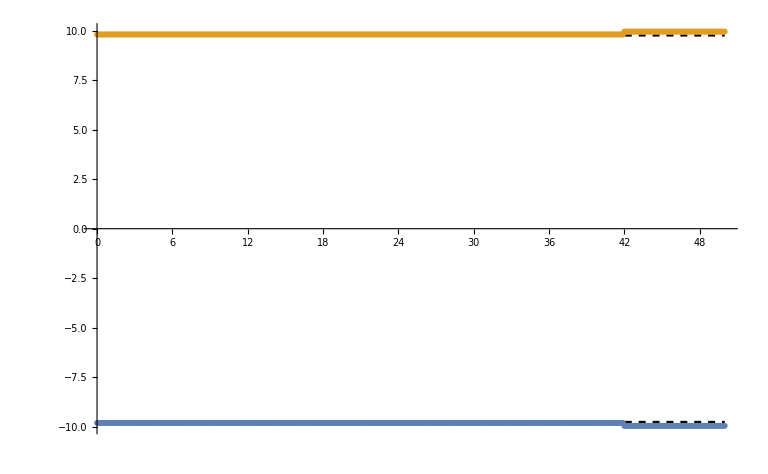

```mathematica
Show[xvstPlot@"C:/VortexData/Type2b_parallel_force",Plot[{-3,3}VortexSize@Type2bVortex,{t,0,50},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
RK4Extender["C:/VortexData/Type2b_parallel_force",20000];
```

#### Anti-parallel case

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type2bVortex,a,v1=1,α1=π/2.,v2=1,α2=-π/2.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=50000,seed,
checkpointInterval=100,checkpointDir="C:/VortexData/Type2b_antiparallel_force"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={18,18,3}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY,"; a = ",a];
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
Show[xvstPlot@checkpointDir,Plot[{-a,a},{t,0,dt numSteps},PlotStyle->Directive[Black,Dashed],PlotRange->All]]
]
```

```mathematica
Show[xvstPlot@"C:/VortexData/Type2b_antiparallel_force",Plot[{-3,3}VortexSize@Type2bVortex,{t,0,50},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
RK4Extender["C:/VortexData/Type2b_antiparallel_force",20000];
```

#### Orthogonal case

```mathematica
Block[{
lX,nX=401,lY,nY=401,state=Type2bVortex,a,v1=1,α1=0.,v2=1,α2=π/2.,
kerOrder=2,v,λ,q,ω,dt=.001,numSteps=20000,seed,
checkpointInterval=100,checkpointDir="C:/VortexData/Type2b_orthogonal_force"
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={18,18,3}VortexSize@state;
Print["lX = ",lX,"; lY = ",lY,"; a = ",a];
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
Show[xvstPlot@checkpointDir,Plot[{-a,a},{t,0,dt numSteps},PlotStyle->Directive[Black,Dashed],PlotRange->All]]
]
```

```mathematica
Show[xvstPlot@"C:/VortexData/Type2b_orthogonal_force",Plot[{-3,3}VortexSize@Type2bVortex,{t,0,50},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
RK4Extender["C:/VortexData/Type2b_orthogonal_force",30000];
```

```mathematica
αvstPlot@"C:/VortexData/Type2b_orthogonal_force"
```

## 2-vortex collisions

### Type I*

#### Parallel case

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,b ,α1=0.,α2=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={18,18,3,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_parallel_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,.3,.9,.1}]
]
```

#### Antiparallel case

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,b ,α1=π/2.,α2=-π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={18,18,3,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_antiparallel_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,0.3,0.9,0.1}]
]
```

#### Orthogonal case

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,b ,α1=0.,α2=π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={18,18,3,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_orthogonal_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,0.5,0.9,0.1}]
]
```

#### Orthogonal case with impact parameter

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,u=.5 ,b,α1=0.,α2=π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
Do[
{lX,lY,a,b}={18,18,3,bfrac}VortexSize@state;
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_orthogonal_u0.50_b"<>ToString@NumberForm[bfrac,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{bfrac,.25,1.,.25}]
]
```

#### Parallel case with impact parameter

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,u=.5,b,α1=0.,α2=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
Do[
{lX,lY,a,b}={18,18,3,bfrac}VortexSize@state;
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_parallel_u"<>ToString@NumberForm[u,{2,2}]<>"_b"<>ToString@NumberForm[bfrac,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{bfrac,1.,1.,.25}]
]
```

#### Make videos

```mathematica
Do[
MakeVideo[ϕ2,4,-27.,0.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_phi.mp4"];
If[!StringContainsQ[checkpointDir,"antiparallel"],MakeVideo[χ2,4,-6.,6.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi2.mp4"]];
If[!StringContainsQ[checkpointDir,"parallel"],MakeVideo[χ3,4,-6.,6.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi3.mp4"]];
,{checkpointDir,Select[FileNames@"C:\\VortexData\\Type1_*_b1.00",DirectoryQ]}]
```

### Type II

#### Parallel case

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,b ,α1=0.,α2=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={14,14,2,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_parallel_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,.3,.9,.1}]
]
```

#### Antiparallel case

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,b ,α1=π/2.,α2=-π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={14,14,2,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_antiparallel_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,0.3,0.9,0.1}]
]
```

#### Orthogonal case

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,b ,α1=0.,α2=π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={14,14,2,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_orthogonal_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,0.3,0.9,0.1}]
]
```

#### Parallel case with impact parameter

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,u=.5 ,b,α1=0.,α2=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
Do[
{lX,lY,a,b}={14,14,2,bfrac}VortexSize@state;
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_parallel_u0.50_b"<>ToString@NumberForm[bfrac,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{bfrac,.25,1.,.25}]
]
```

#### Anti-parallel case with impact parameter

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,u=.5 ,b,α1=-π/2.,α2=π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
Do[
{lX,lY,a,b}={14,14,2,bfrac}VortexSize@state;
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_antiparallel_u0.50_b"<>ToString@NumberForm[bfrac,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{bfrac,.25,1.,.25}]
]
```

#### Make videos

```mathematica
Do[
MakeVideo[ϕ2,10,-16.5,0.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_phi.mp4"];
If[!StringContainsQ[checkpointDir,"antiparallel"],MakeVideo[χ2,10,-3.,3.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi2.mp4"]];
If[!StringContainsQ[checkpointDir,"parallel"],MakeVideo[χ3,10,-3.,3.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi3.mp4"]];
,{checkpointDir,Select[FileNames@"C:\\VortexData\\Type2b_*_b*",DirectoryQ]}]
```

## Vortex / Anti-vortex scattering

### Type I*

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,b ,v1=1,α1=π/2.,v2=-1,α2=-π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={18,18,3,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_vvbar_antiparallel_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,0.3,0.9,0.1}]
]
```

```mathematica
Do[
(*MakeVideo[ϕ2,10,-27.,0.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_phi.mp4"];*)
If[!StringContainsQ[checkpointDir,"_antiparallel_"],MakeVideo[χ2,10,-5.,5.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi2.mp4"]];
If[!StringContainsQ[checkpointDir,"_parallel_"],MakeVideo[χ3,10,-5.,5.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi3.mp4"]];
,{checkpointDir,Select[FileNames@"C:\\VortexData\\Type1_vvbar_*",DirectoryQ]}]
```

### Type II

```mathematica
Block[{
v,λ,q,ω,
lX,nX=401,lY,nY=401,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,b ,v1=1,α1=π/2.,v2=-1,α2=-π/2.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a,b}={18,18,3,0}VortexSize@state;
Do[
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_vvbar_antiparallel_u"<>ToString@NumberForm[u,{2,2}]};
seed=BiVortexSeed[{lX,nX},{lY,nY}][state,a,u,b,α1,α2];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
,{u,0.3,0.9,0.1}]
]
```

## 3-vortex collisions

```mathematica
Table[
Block[{
v,λ,q,ω,
lX,nX=801,lY,nY=801,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,v1=1,α1=0.,v2=1,α2=0.,v3=1,α3=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={24,24,4}VortexSize@state;
checkpointDir=FileNameJoin@{"D:\\VortexData","Type1_3vortex_parallel_u"<>ToString@NumberForm[β,{2,2}]};
seed=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,β,{{v1,α1},{v2,α2},{v3,α3}}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
,{β,.3,.9,.2}]
```

```mathematica
Do[
Block[{
v,λ,q,ω,
lX,nX=801,lY,nY=801,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,v1=1,α1=0.,v2=1,α2=0.,v3=1,α3=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={24,24,4}VortexSize@state;
checkpointDir=FileNameJoin@{"D:\\VortexData","Type2b_3vortex_parallel_u"<>ToString@NumberForm[β,{2,2}]};
seed=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,β,{{v1,α1},{v2,α2},{v3,α3}}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
,{β,{.3,.5,.9}}]
```

```mathematica
MakeVideo[ϕ2,10,-17.,0.]["C:\\VortexData\\Type2b_3vortex_parallel_u0.70","Type2b_3vortex_parallel_u0.70.mp4"]
```

## 4-vortex collisions

```mathematica
Block[{
v,λ,q,ω,
lX,nX=801,lY,nY=801,kerOrder=2,state=Type2bVortex,dt=.001,numSteps=30000,a,β=.5,v1=1,α1=0.,v2=1,α2=0.,v3=1,α3=0.,v4=1,α4=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={24,24,4}VortexSize@state;
checkpointDir=FileNameJoin@{"C:\\VortexData","Type2b_4vortex_parallel_u"<>ToString@NumberForm[β,{2,2}]};
seed=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,β,{{v1,α1},{v2,α2},{v3,α3},{v4,α4}}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

```mathematica
Block[{
v,λ,q,ω,
lX,nX=801,lY,nY=801,kerOrder=2,state=Type1Vortex,dt=.001,numSteps=30000,a,β=.5,v1=1,α1=0.,v2=1,α2=0.,v3=1,α3=0.,v4=1,α4=0.,
checkpointInterval=100,checkpointDir,seed
},
{v,λ,q,ω}=VortexParameters@state;
{lX,lY,a}={24,24,4}VortexSize@state;
checkpointDir=FileNameJoin@{"C:\\VortexData","Type1_4vortex_parallel_u"<>ToString@NumberForm[β,{2,2}]};
seed=MultiVortexSeed[{lX,nX},{lY,nY}][state,a,β,{{v1,α1},{v2,α2},{v3,α3},{v4,α4}}];
RK4[{lX,nX},{lY,nY}][kerOrder,kerOrder][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

## [OLD] 6-vortex collisions

```mathematica
Block[{lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=.5,ω=1.,dt=.001,numSteps=15000,state=sampleStateRadial,a=5.,β=0.50,
checkpointInterval=100,checkpointDir=FileNameJoin@{"C:\\VortexData","6vvbar_parallel_u0.50"},seed},
seed=MultiVortexSeed[{lX,nX},{lY,nY}][v,λ,q,ω][state,a,β,Table[{1,0.},{i,6}]];
RK4[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

```mathematica
Block[{lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=0.5,ω=1.,dt=.001,numSteps=10000,state=sampleStateRadial,a=5.,β=0.75,
checkpointInterval=100,checkpointDir=FileNameJoin@{"C:\\VortexData","new_6vvbar_parallel_u0.75"},seed},
(*seed=MultiVortexSeed[{lX,nX},{lY,nY}][v,λ,q,ω][state,a,β,Table[{(-1)^i,0.},{i,6}]];*)
seed=Import@"C:\\VortexData\\6vvbar_parallel_u0.75\\20000.mat";
RK4[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps,seed][checkpointInterval,checkpointDir];
]
```

```mathematica
Block[{dir="C:\\VortexData\\new_6vvbar_parallel_u0.75",shift=20000,numSteps,checkpointInterval},
{numSteps,checkpointInterval}={"numSteps","checkpointInterval"}/.Import@FileNameJoin@{dir,"parameters.json"};
Do[
RenameFile[FileNameJoin@{dir,ToString@step<>".mat"},FileNameJoin@{dir,ToString[step+shift]<>".mat"}]
,{step,checkpointInterval,numSteps,checkpointInterval}]
]
```

```mathematica
Block[{
dirName="6vvbar_parallel_u0.50",
checkpointDir
},
checkpointDir=FileNameJoin@{"C:\\VortexData",dirName};
MakeVideo[ϕ2,4,0.,5.5][checkpointDir,"videos\\"<>dirName<>"_phi.mp4"]
]
```

```mathematica
Block[{
dirName="6vvbar_parallel_u0.50",
checkpointDir
},
checkpointDir=FileNameJoin@{"C:\\VortexData",dirName};
MakeVideo[χ2,4,-2.5,3.0][checkpointDir,"videos\\"<>dirName<>"_chi.mp4"]
]
```

# Critical velocity

## Binary search

Here we use binary search to find the critical velocities for vortex scattering to appear.

```mathematica
ClearAll@ScatteringQ;
ScatteringQ[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer][state_,a_Real,u1_Real,{v1_Integer,α1_Real},{v2_Integer,α2_Real}]:=
Block[{b=0.,checkpointDir=FileNameJoin@{$TemporaryDirectory,"NNRK4_"<>StringJoin@RandomChoice[Alphabet[],8]},seed,params,initial,final,ymax},
seed=BiVortexSeed[{lX,nX},{lY,nY}][v,λ,q,ω][state,a,u1,b,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps,seed][numSteps,checkpointDir];
params=FileNameJoin@{checkpointDir,"parameters.json"};
initial=FileNameJoin@{checkpointDir,"0.mat"};
final=FileNameJoin@{checkpointDir,ToString@numSteps<>".mat"};
ymax=Max[Last/@xyϕmin[{lX,nX},{lY,nY}]@final];
DeleteFile@{initial,final,params};
DeleteDirectory@checkpointDir;
ymax>lY/(nY-1)
]
```

```mathematica
ClearAll@CriticalVelocity;
CriticalVelocity[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer][state_,a_Real,{v1_Integer,α1_Real},{v2_Integer,α2_Real}][umin_Real,umax_Real,Δu_Real]/;umax-umin<Δu:=Mean@{umin,umax};
CriticalVelocity[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer][state_,a_Real,{v1_Integer,α1_Real},{v2_Integer,α2_Real}][umin_Real,umax_Real,Δu_Real]:=
Block[{umid=Mean@{umin,umax}},
PrintTemporary["Trying u = ",umid,"!"];
If[ScatteringQ[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps][state,a,umid,{v1,α1},{v2,α2}],
Print["u = ",umid," is scattering!"];
CriticalVelocity[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps][state,a,{v1,α1},{v2,α2}][umin,umid,Δu]
,
Print["u = ",umid," is NOT scattering!"];
CriticalVelocity[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps][state,a,{v1,α1},{v2,α2}][umid,umax,Δu]
]
]
```

## Data generation

### Parallel case

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=.5,ω=1.,dt=.001,numSteps=20000,state=sampleStateRadial,a=3.,umin=0.5,umax=0.55,Δu=.001,v1=1,α1=0.,v2=1,α2=0.
},
CriticalVelocity[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps][state,a,{v1,α1},{v2,α2}][umin,umax,Δu]
]
```

### Antiparallel case

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=.5,ω=1.,dt=.001,numSteps=20000,state=sampleStateRadial,a=3.,umin=0.75,umax=0.8,Δu=.001,v1=1 ,α1=-π/2.,v2=1,α2=π/2.
},
CriticalVelocity[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps][state,a,{v1,α1},{v2,α2}][umin,umax,Δu]
]
```

### Orthogonal case

```mathematica
Block[{
lX=20.,nX=401,lY=20.,nY=401,kerOrderX=2,kerOrderY=2,v=2.,λ=2.,q=1.,ω=1.,dt=.001,numSteps=15000,state=sampleStateRadial,a=3.,umin=0.52,umax=0.53,Δu=.001,v1=1,α1=0.,v2=1,α2=π/2.
},
CriticalVelocity[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps][state,a,{v1,α1},{v2,α2}][umin,umax,Δu]
]
```

# Phase diagram

## Abelian vs. Non-abelian

### Binary search in m_χ

```mathematica
ClearAll@NonAbelianQ;
NonAbelianQ[lR_Real,nR_Integer,ϵ_Real][v_Real,λ_Real,q_Real,ω_Real][χThreshold_Real]:=
Block[{ϕr,χr,Aθ,params},
{{ϕr,χr,Aθ},params}=GetStateRadial[lR,nR,ϵ][v,λ,q,ω];
χr[0]>χThreshold
]
```

```mathematica
ClearAll@NonAbelianBoundary;
NonAbelianBoundary[lR_Real,nR_Integer,ϵ_Real][mγ_Real,{mχmin_Real,mχmax_Real,Δmχ_Real},χThreshold_Real]/;mχmax-mχmin<Δmχ:=Mean@{mχmin,mχmax};
NonAbelianBoundary[lR_Real,nR_Integer,ϵ_Real][mγ_Real,{mχmin_Real,mχmax_Real,Δmχ_Real},χThreshold_Real]:=
Block[{mχmid=Mean@{mχmin,mχmax},mϕ=1.,curv,curλ,curq,curω},
{curv,curλ,curq,curω}={1.,λ,q,ω}/.FindParameters[mϕ,mχmid,mγ];
PrintTemporary["Trying mχ = ",mχmid," using v = ",curv,"; λ = ",curλ,"; q = ",curq,"; ω = ",curω];
If[NonAbelianQ[lR,nR,ϵ][curv,curλ,curq,curω][χThreshold],
Print["mχ = ",mχmid," is non-abelian!"];
NonAbelianBoundary[lR,nR,ϵ][mγ,{mχmid,mχmax,Δmχ},χThreshold]
,
Print["mχ = ",mχmid," is abelian!"];
NonAbelianBoundary[lR,nR,ϵ][mγ,{mχmin,mχmid,Δmχ},χThreshold]
]
]
```

### Data generation

```mathematica
NonAbelianBoundaryData=ParallelTable[
Block[{lR=√2 100.,nR=10001,ϵ=10.^-5,mϕ=1.,mχ,mχmin=NonAbelianBoundaryFunction@mγ-.01,mχmax=NonAbelianBoundaryFunction@mγ+.01,Δmχ=.001,χThreshold=.01},
Print["Computing boundary position for mγ = ",mγ];
mχ=NonAbelianBoundary[lR,nR,ϵ][mγ,{mχmin,mχmax,Δmχ},χThreshold];
Print@{mχ,mγ};
{mχ,mγ}
]
,{mγ,.01,2.,.01}];
```

```mathematica
NonAbelianBoundaryData={{0.35652343750000004,0.01},{0.3553515625,0.02},{0.35410156249999997,0.03},{0.3528515625,0.04},{0.3516015625,0.05},{0.3497265625,0.060000000000000005},{0.34792968750000003,0.06999999999999999},{0.3466796875,0.08},{0.3448046875,0.09},{0.3423828125,0.09999999999999999},{0.3405078125,0.10999999999999999},{0.33863281250000005,0.12},{0.33683593749999996,0.13},{0.33496093749999994,0.13999999999999999},{0.3324609375,0.15},{0.3306640625,0.15999999999999998},{0.3287890625,0.16999999999999998},{0.32691406250000005,0.18},{0.3244921875,0.19},{0.32261718749999996,0.2},{0.3207421875,0.21},{0.3188671875,0.22},{0.3170703125,0.23},{0.31519531250000005,0.24},{0.31332031250000003,0.25},{0.31089843749999996,0.26},{0.3090234375,0.27},{0.3071484375,0.28},{0.30535156250000006,0.29000000000000004},{0.30347656250000005,0.30000000000000004},{0.3016015625000001,0.31000000000000005},{0.2998046875,0.32},{0.29855468749999997,0.33},{0.2966796875,0.34},{0.2948046875,0.35000000000000003},{0.2930078125000001,0.36000000000000004},{0.29113281250000006,0.37},{0.2898828125000001,0.38},{0.28800781250000007,0.39},{0.2862109375,0.4},{0.2849609375,0.41},{0.28308593750000005,0.42},{0.2819140625000001,0.43},{0.28003906250000005,0.44},{0.2787890625000001,0.45},{0.2769140625000001,0.46},{0.27574218750000007,0.47000000000000003},{0.2738671875,0.48000000000000004},{0.2726171875,0.49},{0.27136718750000005,0.5},{0.26949218750000004,0.51},{0.26832031250000005,0.52},{0.2670703125000001,0.53},{0.2651953125,0.54},{0.26394531250000003,0.55},{0.26277343750000004,0.56},{0.2615234375,0.5700000000000001},{0.26027343750000004,0.5800000000000001},{0.25902343750000006,0.5900000000000001},{0.25714843750000005,0.6000000000000001},{0.2559765625,0.6100000000000001},{0.2547265625,0.6200000000000001},{0.2534765625,0.63},{0.25222656250000003,0.64},{0.2509765625,0.65},{0.2498046875,0.66},{0.24855468749999998,0.67},{0.2473046875,0.68},{0.24667968750000002,0.6900000000000001},{0.2454296875,0.7},{0.2442578125,0.71},{0.24300781250000003,0.72},{0.2417578125,0.73},{0.24050781250000003,0.74},{0.2398828125,0.75},{0.2387109375,0.76},{0.23746093750000002,0.77},{0.2362109375,0.78},{0.2355859375,0.79},{0.23433593750000004,0.8},{0.2330859375,0.81},{0.2325390625,0.8200000000000001},{0.23128906250000003,0.8300000000000001},{0.2300390625,0.8400000000000001},{0.22941406250000002,0.8500000000000001},{0.22816406250000004,0.8600000000000001},{0.2275390625,0.8700000000000001},{0.2263671875,0.8800000000000001},{0.22511718749999998,0.89},{0.2244921875,0.9},{0.22324218750000002,0.91},{0.22261718749999998,0.92},{0.2213671875,0.93},{0.22074218750000002,0.9400000000000001},{0.21957031250000003,0.95},{0.2189453125,0.96},{0.2183203125,0.97},{0.21707031250000003,0.98},{0.2164453125,0.99},{0.2151953125,1.},{0.21457031250000003,1.01},{0.21402343750000002,1.02},{0.2127734375,1.03},{0.2121484375,1.04},{0.21152343750000002,1.05},{0.2102734375,1.06},{0.2096484375,1.07},{0.20902343750000002,1.08},{0.20785156250000003,1.09},{0.20722656250000004,1.1},{0.2066015625,1.11},{0.20597656250000002,1.12},{0.20535156250000003,1.1300000000000001},{0.2041015625,1.1400000000000001},{0.2034765625,1.1500000000000001},{0.20285156250000003,1.1600000000000001},{0.20222656250000004,1.1700000000000002},{0.20167968750000004,1.1800000000000002},{0.2004296875,1.1900000000000002},{0.19980468750000002,1.2000000000000002},{0.19917968750000004,1.21},{0.19855468750000005,1.22},{0.1979296875,1.23},{0.19730468750000002,1.24},{0.19667968750000003,1.25},{0.19550781250000004,1.26},{0.19488281250000006,1.27},{0.19425781250000002,1.28},{0.19363281250000003,1.29},{0.19300781250000004,1.3},{0.19238281250000006,1.31},{0.1917578125,1.32},{0.19113281250000003,1.33},{0.19050781250000004,1.34},{0.18988281250000005,1.35},{0.1893359375,1.36},{0.1887109375,1.37},{0.18808593750000002,1.3800000000000001},{0.18746093750000004,1.3900000000000001},{0.1868359375,1.4000000000000001},{0.1862109375,1.4100000000000001},{0.18558593750000002,1.4200000000000002},{0.18496093750000003,1.4300000000000002},{0.1843359375,1.4400000000000002},{0.1837109375,1.45},{0.1831640625,1.46},{0.18253906250000002,1.47},{0.18191406250000003,1.48},{0.18128906250000004,1.49},{0.18128906250000004,1.5},{0.1806640625,1.51},{0.1800390625,1.52},{0.17941406250000003,1.53},{0.17878906250000004,1.54},{0.1781640625,1.55},{0.1775390625,1.56},{0.1769921875,1.57},{0.1769921875,1.58},{0.17636718750000002,1.59},{0.17574218749999998,1.6},{0.1751171875,1.61},{0.1744921875,1.62},{0.17386718750000002,1.6300000000000001},{0.17386718750000002,1.6400000000000001},{0.17324218749999998,1.6500000000000001},{0.1726171875,1.6600000000000001},{0.1719921875,1.6700000000000002},{0.17136718750000002,1.6800000000000002},{0.17082031250000002,1.69},{0.17082031250000002,1.7},{0.17019531250000003,1.71},{0.1695703125,1.72},{0.1689453125,1.73},{0.1689453125,1.74},{0.1683203125,1.75},{0.16769531250000003,1.76},{0.16707031249999998,1.77},{0.16707031249999998,1.78},{0.1664453125,1.79},{0.1658203125,1.8},{0.16519531250000002,1.81},{0.1652734375,1.82},{0.16464843750000002,1.83},{0.16402343750000004,1.84},{0.1633984375,1.85},{0.1633984375,1.86},{0.1627734375,1.87},{0.16214843750000002,1.8800000000000001},{0.16214843750000002,1.8900000000000001},{0.16152343750000003,1.9000000000000001},{0.1608984375,1.9100000000000001},{0.1608984375,1.9200000000000002},{0.1602734375,1.93},{0.15964843750000002,1.94},{0.15964843750000002,1.95},{0.15910156250000002,1.96},{0.15847656250000003,1.97},{0.15847656250000003,1.98},{0.15785156250000004,1.99},{0.1572265625,2.}};
```

```mathematica
NonAbelianBoundaryFunction=Interpolation[Reverse/@NonAbelianBoundaryData,InterpolationOrder->1];
```

### Plots

```mathematica
NonAbelianPhaseDiagram=
Block[{p1,p2,x,y,x0},
{p1,p2}=Sort[NonAbelianBoundaryData,Last@#1<Last@#2&]⟦;;2⟧;
{x,y}=p1+t(p2-p1);
x0=x/.First@Solve[y==0];
Show[
ListPlot[PrependTo[NonAbelianBoundaryData,{x0,0}],PlotRange->{{0,1},{0,2}},AspectRatio->GoldenRatio,Joined->True,AxesLabel->{MaTeX["\\frac{m_\\chi}{m_\\phi}",FontSize->MATEXSIZE],MaTeX["\\frac{m_\\gamma}{m_\\phi}",FontSize->MATEXSIZE]},ImageSize->512,Filling->Bottom,TicksStyle->14],
Plot[0,{x,0,Min[First/@NonAbelianBoundaryData]},PlotRange->{0,Max[Last/@NonAbelianBoundaryData]},Filling->Top,PlotStyle->Thickness@0]
]
]
```

## Vortex types

```mathematica
ClearAll@RightmostVortex;
RightmostVortex[{lX_Real,nX_Integer},{lY_Real,nY_Integer}][snapshotFile_String]:=Max[First/@xyϕmin[{lX,nX},{lY,nY}]@snapshotFile]
```

```mathematica
ClearAll@EstimateRadialParameters;
EstimateRadialParameters[mϕ_Real,mχ_Real,mγ_Real][dR_Real]:=
Block[{L=(Log@2)/Min[mϕ,mχ,mγ]},
{√2 Ceiling[20L,100.],Max[Ceiling[(18L)/dR,5000]+1,10001]}
]
```

```mathematica
ClearAll@RepulsiveQ;
RepulsiveQ[{lR_Real,nR_Integer,ϵ_Real},{nX_Integer,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][v_Real,λ_Real,q_Real,ω_Real][dt_Real,numSteps_Integer][{v1_Integer?SignQ,α1_Real},{v2_Integer?SignQ,α2_Real}]:=
Block[{checkpointDir=FileNameJoin@{$TemporaryDirectory,"NNRK4_"<>StringJoin@RandomChoice[Alphabet[],8]},state,size,lX,lY,a,seed,last=numSteps,xmax,xini},
state=GetStateRadial[lR,nR,ϵ][v,λ,q,ω];
{lX,lY,a}={18,18,3}VortexSize@state;
seed=StaticVortexSeed[{lX,nX},{lY,nY}][state,a,{v1,α1},{v2,α2}];
RK4[{lX,nX},{lY,nY}][kerOrderX,kerOrderY][v,λ,q,ω][dt,numSteps,seed][numSteps,checkpointDir];
xini=RightmostVortex[{lX,nX},{lY,nY}]@FileNameJoin@{checkpointDir,"0.mat"};
xmax:=RightmostVortex[{lX,nX},{lY,nY}]@FileNameJoin@{checkpointDir,ToString@last<>".mat"};
While[xmax==xini,
RK4Extender[checkpointDir,numSteps];
last+=numSteps;
];
DeleteFile/@FileNames@FileNameJoin@{checkpointDir,"*"};
DeleteDirectory@checkpointDir;
Print["Vortices started at |x| = ",a,", now at |x| = ",xmax];
xmax>a
]
```

```mathematica
Block[{dR=.02,lR,nR,ϵ=10.^-5,nX=401,nY=401,kerOrder=2,mϕ=1.,mχ=NonAbelianBoundaryFunction@.3-.01,mγ=.5,curv,curλ,curq,curω,dt=.001,numSteps=1000,v1=1,α1=0.,v2=1,α2=0.},
{lR,nR}=EstimateRadialParameters[mϕ,mχ,mγ]@dR;
{curv,curλ,curq,curω}={1.,λ,q,ω}/.FindParameters[mϕ,mχ,mγ];
{{mχ,mγ},RepulsiveQ[{lR,nR,ϵ},{nX,nY}][kerOrder,kerOrder][curv,curλ,curq,curω][dt,numSteps][{v1,α1},{v2,α2}]}
]
```

```mathematica
ClearAll@RepulsiveBoundary;
RepulsiveBoundary[{dR_Real,ϵ_Real},{nX_Integer,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][dt_Real,numSteps_Integer][{v1_Integer,α1_Real},{v2_Integer,α2_Real}][mγ_Real,mχmin_Real,mχmax_Real,Δmχ_Real]/;mχmax-mχmin<Δmχ:=MeanAround@{mχmin,mχmax};
RepulsiveBoundary[{dR_Real,ϵ_Real},{nX_Integer,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][dt_Real,numSteps_Integer][{v1_Integer,α1_Real},{v2_Integer,α2_Real}][mγ_Real,mχmin_Real,mχmax_Real,Δmχ_Real]:=
Block[{mχmid=Mean@{mχmin,mχmax},mϕ=1.,curv,curλ,curq,curω,lR,nR},
{curv,curλ,curq,curω}={1.,λ,q,ω}/.FindParameters[mϕ,mχmid,mγ];
{lR,nR}=EstimateRadialParameters[mϕ,mχmid,mγ]@dR;
PrintTemporary["Trying mχ = ",mχmid," using v = ",curv,"; λ = ",curλ,"; q = ",curq,"; ω = ",curω];
If[RepulsiveQ[{lR,nR,ϵ},{nX,nY}][kerOrderX,kerOrderY][curv,curλ,curq,curω][dt,numSteps][{v1,α1},{v2,α2}],
Print["mχ = ",mχmid," is repulsive!"];
RepulsiveBoundary[{dR,ϵ},{nX,nY}][kerOrderX,kerOrderY][dt,numSteps][{v1,α1},{v2,α2}][mγ,mχmin,mχmid,Δmχ]
,
Print["mχ = ",mχmid," is attractive!"];
RepulsiveBoundary[{dR,ϵ},{nX,nY}][kerOrderX,kerOrderY][dt,numSteps][{v1,α1},{v2,α2}][mγ,mχmid,mχmax,Δmχ]
]
]
```

```mathematica
ClearAll@RepulsiveBoundaryPoint;
RepulsiveBoundaryPoint[{dR_Real,ϵ_Real},{nX_Integer,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][dt_Real,numSteps_Integer][{v1_Integer,α1_Real},{v2_Integer,α2_Real}][mγmin_Real,mγmax_Real,Δmγ_Real]/;mγmax-mγmin<Δmγ:=MeanAround@{mγmin,mγmax};
RepulsiveBoundaryPoint[{dR_Real,ϵ_Real},{nX_Integer,nY_Integer}][kerOrderX_Integer?EvenQ,kerOrderY_Integer?EvenQ][dt_Real,numSteps_Integer][{v1_Integer,α1_Real},{v2_Integer,α2_Real}][mγmin_Real,mγmax_Real,Δmγ_Real]:=
Block[{mγmid=Mean@{mγmin,mγmax},mϕ=1.,mχ,curv,curλ,curq,curω,lR,nR},
mχ=NonAbelianBoundaryFunction@mγmid-.01;
{curv,curλ,curq,curω}={1.,λ,q,ω}/.FindParameters[mϕ,mχ,mγmid];
{lR,nR}=EstimateRadialParameters[mϕ,mχ,mγmid]@dR;
PrintTemporary["Trying mγ = ",mγmid," using v = ",curv,"; λ = ",curλ,"; q = ",curq,"; ω = ",curω];
If[RepulsiveQ[{lR,nR,ϵ},{nX,nY}][kerOrderX,kerOrderY][curv,curλ,curq,curω][dt,numSteps][{v1,α1},{v2,α2}],
Print["mγ = ",mγmid," is repulsive!"];
RepulsiveBoundaryPoint[{dR,ϵ},{nX,nY}][kerOrderX,kerOrderY][dt,numSteps][{v1,α1},{v2,α2}][mγmid,mγmax,Δmγ]
,
Print["mγ = ",mγmid," is attractive!"];
RepulsiveBoundaryPoint[{dR,ϵ},{nX,nY}][kerOrderX,kerOrderY][dt,numSteps][{v1,α1},{v2,α2}][mγmin,mγmid,Δmγ]
]
]
```

```mathematica
Block[{dR=.02,ϵ=10.^-5,nX=401,nY=401,kerOrder=2,dt=.001,numSteps=5000,v1=1,v2=1,α1=0.,α2=0.,mγmin=0.4,mγmax=0.5,Δmγ=.01},
RepulsiveBoundaryPoint[{dR,ϵ},{nX,nY}][kerOrder,kerOrder][dt,numSteps][{v1,α1},{v2,α2}][mγmin,mγmax,Δmγ]
]
```

### Parallel repulsion region

```mathematica
Block[{lR=√2 100.,nR=10001,ϵ=10.^-5,lX=20.,nX=401,lY=20.,nY=401,kerOrder=2,curv,curλ,curq,curω,dt=.001,numSteps=10000,a=3.,v1=1,α1=0.,v2=1,α2=π/2.,mϕ=1.,mχ},
Table[
mχ=NonAbelianBoundaryFunction@mγ-.005;
{curv,curλ,curq,curω}={1.,λ,q,ω}/.First@FindParameters[mϕ,mχ,mγ];
{{mχ,mγ},RepulsiveQ[{lR,nR,ϵ},{lX,nX},{lY,nY}][kerOrder,kerOrder][curv,curλ,curq,curω][dt,numSteps][a,{v1,α1},{v2,α2}]}
,{mγ,0.01,2.,.01}]
]
```

```mathematica
Table[
Block[{dR=.02,ϵ=10.^-5,nX=401,nY=401,kerOrder=2,dt=.001,numSteps=5000,v1=1,v2=1,α1=0.,α2=0.,mχmin=ParallelRepulsionBoundaryFunction[mγ]["Value"]-.01,mχmax=ParallelRepulsionBoundaryFunction[mγ]["Value"]+.01,Δmχ=.001,mχ},
mχ=RepulsiveBoundary[{dR,ϵ},{nX,nY}][kerOrder,kerOrder][dt,numSteps][{v1,α1},{v2,α2}][mγ,mχmin,mχmax,Δmχ];
Print@{mχ,mγ};
{mχ,mγ}
],{mγ,.2,.2,.02}]
```

#### Results

```mathematica
ParallelRepulsionBoundaryData={{0.03375,0.04},{0.050624999999999996,0.06},{0.07075000000000001,0.08},{0.0859375,0.1},{0.105938,0.12},{0.125938,0.14},{0.145938,0.16},{0.156563,0.18},{0.17031249999999998,0.2},{0.184375,0.22},{0.203125,0.24},{0.209375,0.26},{0.221875,0.28},{0.234375,0.3},{0.239403,0.32},{0.246825,0.34},{0.253796,0.36},{0.260828,0.38},{0.262993,0.4},{0.264243,0.42},{0.267619,0.44},{0.262852,0.46},{0.26918,0.48}};
```

```mathematica
ParallelRepulsionBoundaryData2={{0.171880.00031,0.2}};
```

```mathematica
ParallelRepulsionBoundaryFunction=Interpolation[Reverse/@ParallelRepulsionBoundaryData];
```

```mathematica
NonAbelianPhaseDiagramFull=Show[
ListPlot[Join[{{0,0}},ParallelRepulsionBoundaryData,Sort[Select[NonAbelianBoundaryData,Last@#<0.48&],Last@#1>Last@#2&]],Joined->True,Filling->Axis,FillingStyle->Directive[Orange,Opacity@.5],PlotStyle->Black],
NonAbelianPhaseDiagram,
ListPlot[{Around[First@#,0.01],Last@#}&/@ParallelRepulsionBoundaryData,PlotStyle->Black],
Plot[t,{t,0,mγ/.FindRoot[NonAbelianBoundaryFunction@mγ==mγ,{mγ,.3}]},PlotStyle->Directive[Black,Dashed]]
,PlotRange->{{0,.8},{0,1.5}},AspectRatio->GoldenRatio,AxesLabel->{MaTeX["\\frac{m_\\chi}{m_\\phi}",FontSize->MATEXSIZE],MaTeX["\\frac{m_\\gamma}{m_\\phi}",FontSize->MATEXSIZE]},TicksStyle->14,ImageSize->512,Ticks->{Table[{mχ,"",{.01,0}},{mχ,0.05,.8,.1}]~Join~Table[{mχ,mχ,{.015,0}},{mχ,0,.8,.1}],Table[{mχ,"",{.01,0}},{mχ,0.05,2,.1}]~Join~Table[{mχ,mχ,{.015,0}},{mχ,0,2,.1}]}]
```

```mathematica
Export["phase_diagram.pdf",NonAbelianPhaseDiagramFull]
```

# Video generation

```mathematica
Do[
MakeVideo[ϕ2,1,-16.,0.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>".mp4"];
If[StringContainsQ[checkpointDir,"antiparallel"],
MakeVideo[χ3,1,-2.5,2.5][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi.mp4"],
If[StringContainsQ[checkpointDir,"parallel"],
MakeVideo[χ2,1,-0.5,5.0][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi.mp4"]];];
,{checkpointDir,Select[FileNames@"D:\\VortexData\\Type2_3vortex*",DirectoryQ]}]
```

```mathematica
Do[
MakeVideo[ϕ2,1,-18.,0.][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>".mp4"];
If[StringContainsQ[checkpointDir,"antiparallel"],
MakeVideo[χ3,1,-2.5,2.5][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi.mp4"],
If[StringContainsQ[checkpointDir,"parallel"],
MakeVideo[χ2,1,-1.5,5.0][checkpointDir,"videos\\"<>FileNameTake@checkpointDir<>"_chi.mp4"]];];
,{checkpointDir,Select[FileNames@"D:\\VortexData\\Type2_parallel*",DirectoryQ]}]
```

```mathematica
MakeVideo[ϕ2,1,-18.,0.]["D:\\VortexData\\Type2_static","videos\\Type2_static.mp4"]
```

```mathematica
MakeVideo[χ2,1,-1.5,5.0]["D:\\VortexData\\Type2_static","videos\\Type2_static_chi.mp4"]
```

```mathematica
MakeVideo[ϕ2,1,-18.,0.]["D:\\VortexData\\Type2_4vortex_parallel_u0.50","videos\\Type2_4vortex_parallel_u0.50.mp4"]
```

```mathematica
MakeVideo[χ2,1,-1.5,5.0]["D:\\VortexData\\Type2_4vortex_parallel_u0.50","videos\\Type2_4vortex_parallel_u0.50_chi.mp4"]
```

# Plots

## Gauge condition checks

```mathematica
Block[{lX,nX,lY,nY,dir="C:\\VortexData\\Type1_antiparallel_u0.30",data,Dx,Dy,dt},
{lX,nX,lY,nY,dt}={"lX","nX","lY","nY","dt"}/.Import@FileNameJoin@{dir,"parameters.json"};
(*GaugeCondition[{lX,nX},{lY,nY}][data,4]*)
Dx=NNDer2D[{lX,nX},{lY,nY}][{1,2},{0,0},1];
Dy=NNDer2D[{lX,nX},{lY,nY}][{0,0},{1,2},1];
Table[
With[{snapshot=Import@file},
data=Flatten[Dy[{snapshot⟦7⟧}]+Dx[{snapshot⟦6⟧}]-{snapshot⟦16⟧}];
{dt GetStep@file,Mean@Abs@data}
]
,{file,FileNames@FileNameJoin@{dir,"*.mat"}}]
]
```

```mathematica
meanabs={{0.,0.0000893441200627377},{10.,0.03710739886735352},{1.,0.007325693802244984},{0.1,0.00022714573364082715},{10.1,0.03736246644098339},{10.200000000000001,0.037929600357292925},{10.3,0.03773105741373474},{10.4,0.03791749319837305},{10.5,0.03770862227185457},{10.6,0.03745328501880891},{10.700000000000001,0.037275658060690414},{10.8,0.03698848050425339},{10.9,0.03733840979807274},{11.,0.03745593599455775},{1.1,0.008267769588736207},{11.1,0.037275016394682635},{11.200000000000001,0.03774868160934081},{11.3,0.038546282538640356},{11.4,0.03969635945377087},{11.5,0.04041732258869456},{11.6,0.04054763572929609},{11.700000000000001,0.04153221706595003},{11.8,0.04253314851096361},{11.9,0.04352433577756642},{12.,0.04415807482719988},{1.2,0.009143721321532398},{12.1,0.04403151157336844},{12.200000000000001,0.04456134658118656},{12.3,0.045026516508671996},{12.4,0.04532857679138149},{12.5,0.04555076272832981},{12.6,0.04528840681847006},{12.700000000000001,0.04575785917749837},{12.8,0.04593210351035886},{12.9,0.0459436066258853},{13.,0.04654477595361034},{1.3,0.009928146774637783},{13.1,0.04699300637640768},{13.200000000000001,0.04773282732621929},{13.3,0.048296284347946423},{13.4,0.04902512579490923},{13.5,0.05042230895093521},{13.6,0.05098867288024122},{13.700000000000001,0.05161829633660565},{13.8,0.052172654689298645},{13.9,0.05283348022428744},{14.,0.054197643005753256},{1.4000000000000001,0.010583155403840765},{14.1,0.05466691793701558},{14.200000000000001,0.05490106092253716},{14.3,0.05516018332493751},{14.4,0.05523998676114403},{14.5,0.05613386494031006},{14.6,0.05624306724377541},{14.700000000000001,0.056233262358335395},{14.8,0.056685939662478826},{14.9,0.05681436215193358},{15.,0.05752410804833182},{1.5,0.011108974688909413},{15.1,0.05751594067683739},{15.200000000000001,0.057784654770251076},{15.3,0.05862583763543358},{15.4,0.05907466667150773},{15.5,0.05997813556849675},{15.6,0.060993479544444736},{15.700000000000001,0.06173817198147042},{15.8,0.0626901211326648},{15.9,0.06266284639998095},{16.,0.06362287296573906},{1.6,0.011464166853343347},{16.1,0.06506019796758439},{16.2,0.06579594770739544},{16.3,0.06668721327450615},{16.4,0.06644003457602829},{16.5,0.06697834283803562},{16.6,0.06792132224728399},{16.7,0.06830150043929546},{16.8,0.0691569912740223},{16.9,0.06932499503360455},{17.,0.0702085308766119},{1.7,0.011643314082863926},{17.1,0.07146698726369928},{17.2,0.07133824367663323},{17.3,0.07209418084882831},{17.400000000000002,0.07262991993783743},{17.5,0.07341483096373481},{17.6,0.0744780075594503},{17.7,0.0749907217519208},{17.8,0.07661014917275906},{17.900000000000002,0.07727911855987957},{18.,0.07741197370204474},{1.8,0.011643399878483672},{18.1,0.07817690341026853},{18.2,0.07884509316244762},{18.3,0.08044986404675628},{18.400000000000002,0.08134395045519952},{18.5,0.08109145537720595},{18.6,0.08170441788226138},{18.7,0.08210415426806723},{18.8,0.08304594213625913},{18.900000000000002,0.08355322184836196},{19.,0.08335656171339122},{1.9000000000000001,0.011437592708614079},{19.1,0.08442657431918331},{19.2,0.08517706950839808},{19.3,0.08620457962264526},{19.400000000000002,0.08654265856558091},{19.5,0.08636889947287164},{19.6,0.08773757423480728},{19.7,0.08863220551989545},{19.8,0.08935715066979565},{19.900000000000002,0.09063500692043579},{20.,0.09085420209021225},{2.,0.011066258034568186},{0.2,0.0005967395340283793},{20.1,0.09194746570670789},{20.2,0.09245648550097701},{20.3,0.0927489401788078},{20.400000000000002,0.09433854955791332},{20.5,0.09489091051723994},{20.6,0.09575383397740433},{20.7,0.09592459673517947},{20.8,0.09606538703984933},{20.900000000000002,0.09741089531622879},{21.,0.09749246529160635},{2.1,0.010510438638801432},{21.1,0.09837840973279617},{21.2,0.098728188932701},{21.3,0.09927950069027211},{21.400000000000002,0.10116299413852144},{21.5,0.10105253583741815},{21.6,0.10169507074092914},{21.7,0.10262950443594679},{21.8,0.10288865444643595},{21.900000000000002,0.10473846024493831},{22.,0.10506304919954795},{2.2,0.009790673398496317},{22.1,0.10631663352907848},{22.2,0.10759461109156498},{22.3,0.10695658996535985},{22.400000000000002,0.10758275196664514},{22.5,0.10836635983570753},{22.6,0.11006352753474823},{22.7,0.11157267340552508},{22.8,0.11023040158074675},{22.900000000000002,0.11024546550362066},{23.,0.11227890655114384},{2.3000000000000003,0.008954905055691452},{23.1,0.11356073147436667},{23.2,0.11334673245699686},{23.3,0.11147597260689608},{23.400000000000002,0.11417004786317289},{23.5,0.11664443272934633},{23.6,0.11571478757290948},{23.7,0.11520070944953512},{23.8,0.11706080072400979},{23.900000000000002,0.11866544166128755},{24.,0.1174634583969758},{2.4,0.007979474125694705},{24.1,0.11839563387479186},{24.2,0.12234855728434066},{24.3,0.12009765184762375},{24.400000000000002,0.11910504462597668},{24.5,0.12355400745445988},{24.6,0.12286611681700736},{24.7,0.12165665927359924},{24.8,0.12589055798382062},{24.900000000000002,0.12657443518800748},{25.,0.123821969505313},{2.5,0.006926347318776428},{25.1,0.12681303300284996},{25.2,0.12916760276997066},{25.3,0.12535295469745505},{25.400000000000002,0.12884060062951877},{25.5,0.13124702057031998},{25.6,0.1273296674868109},{25.7,0.13310625918799288},{25.8,0.13358712230780886},{25.900000000000002,0.12951339332024564},{26.,0.13545165879525214},{2.6,0.005962983707373388},{26.1,0.13473831804978684},{26.2,0.13302365800647467},{26.3,0.13917881976734411},{26.400000000000002,0.13561650720204563},{26.5,0.13682978562600065},{26.6,0.14111567887748547},{26.7,0.13700925055341615},{26.8,0.14164985420229922},{26.900000000000002,0.14203731827470106},{27.,0.1386443973340624},{2.7,0.005921822244762106},{27.1,0.14514061724682978},{27.2,0.14203591180790823},{27.3,0.14271576519811235},{27.400000000000002,0.14732815054464096},{27.5,0.142867139315925},{27.6,0.1479694182422738},{27.7,0.1469640220957391},{27.8,0.1455681520210916},{27.900000000000002,0.15131502794380122},{28.,0.14603595351017393},{2.8000000000000003,0.006731036360652468},{28.1,0.1523453132096447},{28.2,0.15101985352181066},{28.3,0.14982216914456664},{28.400000000000002,0.15628050015821376},{28.5,0.14962999556644085},{28.6,0.15798299786492523},{28.7,0.15379248818124291},{28.8,0.1566527073407791},{28.900000000000002,0.15921969059048582},{29.,0.15438029962532748},{2.9,0.007521672807298347},{29.1,0.1628121662032053},{29.2,0.15649733802606042},{29.3,0.162782115002517},{29.400000000000002,0.16145021197029347},{29.5,0.16013481164324364},{29.6,0.16587310836706426},{29.7,0.15909769716599645},{29.8,0.16723726471158093},{29.900000000000002,0.16224656777313323},{30.,0.16696704410930124},{3.,0.008670345070639204},{0.3,0.0011235207810188568},{3.1,0.00970183533737635},{3.2,0.010695015062827853},{3.3000000000000003,0.011666341292496196},{3.4,0.012665846966109357},{3.5,0.013463125410851045},{3.6,0.014136721205425673},{3.7,0.014625397085790241},{3.8000000000000003,0.014959310372337175},{3.9,0.015036541244218755},{4.,0.014913361016570658},{0.4,0.001775429358833017},{4.1,0.014683126369989452},{4.2,0.014282171345303145},{4.3,0.01375532859658247},{4.4,0.013027306993371205},{4.5,0.012155092194577664},{4.6000000000000005,0.011741367276341001},{4.7,0.011814583591517604},{4.8,0.012422008980480874},{4.9,0.013547957930809283},{5.,0.01469482798305369},{0.5,0.0025476202623946806},{5.1000000000000005,0.015781484185110946},{5.2,0.01661147184950027},{5.3,0.017766743534089358},{5.4,0.018797600319132694},{5.5,0.0196032754944524},{5.6000000000000005,0.020760568915491155},{5.7,0.021562848870844333},{5.8,0.022034745208661628},{5.9,0.022076557241218733},{6.,0.02226170446721947},{0.6,0.0034172590114148844},{6.1000000000000005,0.02250036995071964},{6.2,0.02235232863189646},{6.3,0.02187101270236766},{6.4,0.0211597277499942},{6.5,0.0202621104848924},{6.6000000000000005,0.020008205481527017},{6.7,0.019690722599977523},{6.8,0.019322183693671825},{6.9,0.019372092126401685},{7.,0.019800950732997823},{0.7000000000000001,0.004355026451552497},{7.1000000000000005,0.020935309635940876},{7.2,0.021860198363615295},{7.3,0.022502143903501342},{7.4,0.02345623233895446},{7.5,0.0245968526939211},{7.6000000000000005,0.025840114186279087},{7.7,0.026347466766383342},{7.8,0.027129391291531687},{7.9,0.02776124970581952},{8.,0.02798508835907264},{0.8,0.005337569155630606},{8.1,0.028181756756322607},{8.2,0.028320006173571586},{8.3,0.02849094691282081},{8.4,0.02848592280043658},{8.5,0.027736720713687758},{8.6,0.027381572563420695},{8.700000000000001,0.027568512581635573},{8.8,0.02775937557610778},{8.9,0.028326402714172434},{9.,0.028673766338975257},{0.9,0.006336229314056258},{9.1,0.029563117851865512},{9.200000000000001,0.030787941449398754},{9.3,0.031664834867051614},{9.4,0.03259465325649721},{9.5,0.033067965501068566},{9.6,0.034342736987512605},{9.700000000000001,0.035657402095654815},{9.8,0.03625914303537811},{9.9,0.03676980177099271}};
```

```mathematica
ListPlot@%
```

```mathematica
mean={{0.,-3.3658604393303763*^-21},{10.,5.411998050583519*^-8},{1.,6.235006669167922*^-11},{0.1,2.3599355999499896*^-11},{10.1,-1.6580497000151915*^-7},{10.200000000000001,-2.8700456027600403*^-7},{10.3,-2.011041397511327*^-7},{10.4,-5.0258052712026016*^-8},{10.5,-3.4914472765441075*^-9},{10.6,-1.3208403997615501*^-8},{10.700000000000001,3.5401889302035587*^-8},{10.8,9.45777229787701*^-8},{10.9,7.23259661105124*^-8},{11.,-9.878578215370796*^-9},{1.1,-4.99581902606701*^-10},{11.1,-9.423099773758149*^-8},{11.200000000000001,-1.483048293721086*^-7},{11.3,-1.0739321979435083*^-7},{11.4,4.385759230702087*^-8},{11.5,1.8219493239107513*^-7},{11.6,1.861183545978261*^-7},{11.700000000000001,5.443004232319205*^-8},{11.8,-1.3675669714178106*^-7},{11.9,-2.3301494645091501*^-7},{12.,-8.185691467529079*^-8},{1.2,-7.226689124523028*^-10},{12.1,1.759139046868955*^-7},{12.200000000000001,2.0250702980533092*^-7},{12.3,2.5497649497793145*^-8},{12.4,4.582973326338112*^-8},{12.5,2.920109871954259*^-7},{12.6,3.0618787942229696*^-7},{12.700000000000001,-3.677072296058712*^-8},{12.8,-2.7666024670332934*^-7},{12.9,-1.3286888185179384*^-7},{13.,8.380062333135539*^-8},{1.3,-5.923926802960874*^-10},{13.1,4.001220040515013*^-8},{13.200000000000001,-1.4378834225056636*^-7},{13.3,-1.9424559709217854*^-7},{13.4,-1.2576018286094402*^-7},{13.5,-1.1241072204906109*^-7},{13.6,-1.1326123762426851*^-7},{13.700000000000001,1.8348743764490303*^-8},{13.8,1.5601876685557137*^-7},{13.9,6.94802504874717*^-8},{14.,-7.703274922177663*^-8},{1.4000000000000001,-3.4661627078786313*^-10},{14.1,3.2224587071565856*^-8},{14.200000000000001,2.1857691406115982*^-7},{14.3,9.810479644291111*^-8},{14.4,-1.269119951822115*^-7},{14.5,-4.188825203173361*^-9},{14.6,2.588504930903605*^-7},{14.700000000000001,1.2712417752634365*^-7},{14.8,-2.748574944420422*^-7},{14.9,-3.9207064283535436*^-7},{15.,-1.4790500126705875*^-7},{1.5,-1.1873597838314785*^-10},{15.1,1.2293613920467578*^-7},{15.200000000000001,2.7747484547033993*^-7},{15.3,2.860991558213704*^-7},{15.4,3.618990840121542*^-8},{15.5,-3.239804354416169*^-7},{15.6,-3.6325751332237896*^-7},{15.700000000000001,-4.634263611813357*^-8},{15.8,1.464048876336677*^-7},{15.9,2.264204453847279*^-9},{16.,-1.3055143904551938*^-7},{1.6,1.0494502741559695*^-9},{16.1,-9.39008892773301*^-9},{16.2,1.5970332031088969*^-7},{16.3,1.7821276950213364*^-7},{16.4,1.1032130848947057*^-7},{16.5,1.2791211968138215*^-8},{16.6,-9.068502415782551*^-8},{16.7,-4.1597764236435076*^-8},{16.8,1.8202016789190283*^-7},{16.9,2.446264294596267*^-7},{17.,-2.326142842670729*^-8},{1.7,1.209170892979529*^-9},{17.1,-2.1434925418671974*^-7},{17.2,1.5444394753991605*^-8},{17.3,3.2656679223397184*^-7},{17.400000000000002,2.3300028229003096*^-7},{17.5,-1.259180572703503*^-7},{17.6,-2.56515132745883*^-7},{17.7,-3.41501222553374*^-8},{17.8,2.100765019130871*^-7},{17.900000000000002,1.5729499028576922*^-7},{18.,-1.2955592394150442*^-7},{1.8,7.761415844363491*^-10},{18.1,-2.925110734140139*^-7},{18.2,-1.5354353302253424*^-7},{18.3,4.236528543142602*^-8},{18.400000000000002,7.960962192080958*^-8},{18.5,1.0374327483938933*^-7},{18.6,1.809506622974363*^-7},{18.7,8.1279631133169*^-8},{18.8,-1.8972429166351723*^-7},{18.900000000000002,-3.201903386328235*^-7},{19.,-2.842198648827684*^-7},{1.9000000000000001,1.8126774527531112*^-9},{19.1,-2.6473559792637086*^-7},{19.2,-1.52463280500894*^-7},{19.3,9.272665259134033*^-8},{19.400000000000002,1.015502487992647*^-7},{19.5,-1.6730321281129454*^-7},{19.6,-1.9343648998161178*^-7},{19.7,1.1321459112311973*^-7},{19.8,2.5632853552300145*^-7},{19.900000000000002,1.334947335383866*^-7},{20.,5.401998295694946*^-8},{2.,2.4646707092011346*^-9},{0.2,-1.983591027448743*^-11},{20.1,-9.201955249255691*^-9},{20.2,-1.574371238518238*^-7},{20.3,-1.3131519725220764*^-7},{20.400000000000002,1.534242665830352*^-7},{20.5,3.856214813594923*^-7},{20.6,4.0379862152627425*^-7},{20.7,2.104419140295647*^-7},{20.8,-1.9334930150422034*^-7},{20.900000000000002,-4.2534141088156796*^-7},{21.,-1.2673385823858747*^-7},{2.1,4.3598333406965404*^-10},{21.1,1.669075013292026*^-7},{21.2,-1.1455608250914922*^-7},{21.3,-3.178732528857074*^-7},{21.400000000000002,2.1508481875396292*^-7},{21.5,7.231228965774121*^-7},{21.6,4.0269901125192474*^-7},{21.7,-2.057805665643918*^-7},{21.8,-3.9838547802848245*^-7},{21.900000000000002,-2.9819379931564197*^-7},{22.,-9.216034662592327*^-8},{2.2,-3.01930785743936*^-9},{22.1,2.0185224688099917*^-7},{22.2,2.843186777496158*^-7},{22.3,6.137683772636457*^-8},{22.400000000000002,-3.628161998210964*^-8},{22.5,1.0778693931762126*^-7},{22.6,1.250489765935721*^-7},{22.7,-6.354901584979972*^-8},{22.8,-2.539871111737446*^-7},{22.900000000000002,-3.3103568210063004*^-7},{23.,-1.0808406181235415*^-7},{2.3000000000000003,-4.4888695746504555*^-10},{23.1,3.604467391119068*^-7},{23.2,4.003748696860167*^-7},{23.3,-2.481192400862504*^-7},{23.400000000000002,-7.000926628690988*^-7},{23.5,-3.6102193212622094*^-7},{23.6,1.23091646631988*^-7},{23.7,2.255537304176146*^-7},{23.8,2.9428427338248763*^-7},{23.900000000000002,3.7116515502032573*^-7},{24.,-1.7885768511572468*^-8},{2.4,7.578845424608458*^-9},{24.1,-6.160387457566113*^-7},{24.2,-5.7557556950376*^-7},{24.3,6.817671131292964*^-8},{24.400000000000002,3.793914438005211*^-7},{24.5,3.787115775031621*^-8},{24.6,-2.1295149600877228*^-7},{24.7,1.2677885032125846*^-7},{24.8,4.781708876146707*^-7},{24.900000000000002,2.3390296211134115*^-7},{25.,-1.4277271816355247*^-7},{2.5,1.0794753592262573*^-8},{25.1,-2.5592879128657162*^-8},{25.2,1.8009576079641127*^-7},{25.3,-8.778650987261505*^-8},{25.400000000000002,-3.4286670429248657*^-7},{25.5,6.2799489614159354*^-9},{25.6,4.582640802675932*^-7},{25.7,3.146183276133782*^-7},{25.8,-1.4056448138372727*^-7},{25.900000000000002,-2.7116643340427357*^-7},{26.,-1.0630725612837358*^-7},{2.6,4.324165107458702*^-9},{26.1,-5.35025156517714*^-8},{26.2,-1.4246592035136488*^-7},{26.3,-5.981884577081202*^-8},{26.400000000000002,1.972543504556299*^-7},{26.5,1.8697966887454499*^-7},{26.6,-2.0456455204545467*^-7},{26.7,-3.860681447249671*^-7},{26.8,-1.4008728807049335*^-8},{26.900000000000002,3.7047767426109817*^-7},{27.,2.6145018646872637*^-7},{2.7,-7.597627147301087*^-9},{27.1,-8.051142624283213*^-8},{27.2,-2.5929806657694196*^-7},{27.3,-2.128847036970878*^-7},{27.400000000000002,-5.963557325127731*^-9},{27.5,8.999414992875182*^-8},{27.6,-1.95580831803452*^-7},{27.7,-4.09997827375133*^-7},{27.8,7.846803028604226*^-8},{27.900000000000002,7.368545180714623*^-7},{28.,5.559072269561234*^-7},{2.8000000000000003,-1.944807199763656*^-8},{28.1,-1.7215569517379216*^-7},{28.2,-3.8613350913363565*^-7},{28.3,-3.954821552376932*^-8},{28.400000000000002,9.480115550169757*^-8},{28.5,-1.8482434884102267*^-7},{28.6,-3.5420123089911404*^-7},{28.7,-3.282308003592337*^-8},{28.8,4.3977120058368753*^-7},{28.900000000000002,3.5880795476884854*^-7},{29.,-2.4106708429984764*^-7},{2.9,-2.7708650595411273*^-8},{29.1,-4.034637098095017*^-7},{29.2,1.6964601544925726*^-7},{29.3,4.712801980253928*^-7},{29.400000000000002,1.6500321119621432*^-8},{29.5,-2.5803421992266107*^-7},{29.6,1.6242368993818633*^-7},{29.7,4.386945165312505*^-7},{29.8,4.440103968913357*^-8},{29.900000000000002,-3.745513757508667*^-7},{30.,-2.744306143739888*^-7},{3.,-2.2243748887114854*^-8},{0.3,-1.0488871847693935*^-10},{3.1,-6.481715207400914*^-9},{3.2,2.952074058179076*^-9},{3.3000000000000003,-2.2254431618897018*^-10},{3.4,-2.6157115956828178*^-9},{3.5,7.256095549126623*^-9},{3.6,1.9394027117219993*^-8},{3.7,1.6702997235152496*^-8},{3.8000000000000003,3.776639414294897*^-9},{3.9,-9.322624847682563*^-9},{4.,-2.7114002450659447*^-8},{0.4,1.2566865887726938*^-10},{4.1,-5.1598314578077776*^-8},{4.2,-5.57438541495955*^-8},{4.3,-1.4622426344746144*^-8},{4.4,4.1510590590812954*^-8},{4.5,5.468939963046247*^-8},{4.6000000000000005,3.236805745616393*^-8},{4.7,3.7800717869479514*^-8},{4.8,8.135417002185485*^-8},{4.9,8.856338556827242*^-8},{5.,2.2131127088002633*^-8},{0.5,4.0239176148295594*^-11},{5.1000000000000005,-5.5235781071919694*^-8},{5.2,-7.251344356491985*^-8},{5.3,-3.4252303400862665*^-8},{5.4,1.0482387310318604*^-8},{5.5,3.708589218862723*^-8},{5.6000000000000005,4.245443473010892*^-8},{5.7,3.104131958185258*^-8},{5.8,2.9720268538432428*^-8},{5.9,5.977921947669889*^-8},{6.,7.242344203841587*^-8},{0.6,2.051962421712337*^-10},{6.1000000000000005,5.3561439606273846*^-9},{6.2,-9.436870391759835*^-8},{6.3,-1.1275196549385066*^-7},{6.4,-4.7144611560031465*^-8},{6.5,-6.935153929202711*^-9},{6.6000000000000005,-2.4460107237707657*^-8},{6.7,-2.0611870595467128*^-8},{6.8,1.761775307635713*^-8},{6.9,8.25800682870727*^-9},{7.,-6.34453621689576*^-8},{0.7000000000000001,3.185000928751906*^-10},{7.1000000000000005,-1.044150652352124*^-7},{7.2,-7.530165041699863*^-8},{7.3,-6.21742984915762*^-8},{7.4,-1.2520120018221772*^-7},{7.5,-1.62142502218871*^-7},{7.6000000000000005,-4.088111640468695*^-8},{7.7,1.5809994044118173*^-7},{7.8,2.1457197385074653*^-7},{7.9,9.497972116779264*^-8},{8.,-7.453702971259249*^-9},{0.8,-1.4735266269233302*^-10},{8.1,-3.114535066474618*^-10},{8.2,1.2855914583539303*^-8},{8.3,-1.177750126253852*^-9},{8.4,5.807597350747291*^-8},{8.5,1.7110242550209201*^-7},{8.6,1.880448377490329*^-7},{8.700000000000001,1.0214776326698907*^-7},{8.8,5.428319565317003*^-8},{8.9,6.558942865666973*^-8},{9.,1.5189629537705955*^-8},{0.9,-1.1026350445511746*^-10},{9.1,-1.2082892238057697*^-7},{9.200000000000001,-2.1983988190044018*^-7},{9.3,-1.9402400843774726*^-7},{9.4,-8.969495052371344*^-8},{9.5,1.475615429320507*^-9},{9.6,4.9370596089935566*^-8},{9.700000000000001,9.275209037791953*^-8},{9.8,1.5687405014403467*^-7},{9.9,1.7549509798113148*^-7}};
```

## Trajectory

### Curated data

```mathematica
xyData["D:\\VortexData\\Type1_antiparallel_u0.90",2,.05,10,5]={{0.,{{-7.028476442253471,0.},{7.028476442253474,0.}}},{0.1,{{-6.923573808786999,0.},{6.923573808787001,0.}}},{0.2,{{-6.81867117532053,0.},{6.818671175320532,0.}}},{0.3,{{-6.71376854185406,0.},{6.713768541854062,0.}}},{0.4,{{-6.608865908387591,0.},{6.6088659083875925,0.}}},{0.5,{{-6.503963274921121,0.},{6.503963274921123,0.}}},{0.6,{{-6.503963274921121,0.},{6.503963274921123,0.}}},{0.7000000000000001,{{-6.399060641454652,0.},{6.399060641454653,0.}}},{0.8,{{-6.294158007988182,0.},{6.294158007988184,0.}}},{0.9,{{-6.1892553745217125,0.},{6.189255374521714,0.}}},{1.,{{-6.084352741055243,0.},{6.084352741055245,0.}}},{1.1,{{-5.979450107588773,0.},{5.979450107588775,0.}}},{1.2,{{-5.874547474122302,0.},{5.874547474122306,0.}}},{1.3,{{-5.874547474122302,0.},{5.874547474122306,0.}}},{1.4000000000000001,{{-5.7696448406558325,0.},{5.769644840655836,0.}}},{1.5,{{-5.664742207189363,0.},{5.6647422071893665,0.}}},{1.6,{{-5.559839573722893,0.},{5.559839573722897,0.}}},{1.7,{{-5.454936940256424,0.},{5.454936940256427,0.}}},{1.8,{{-5.350034306789954,0.},{5.350034306789958,0.}}},{1.9000000000000001,{{-5.245131673323485,0.},{5.245131673323488,0.}}},{2.,{{-5.245131673323485,0.},{5.245131673323488,0.}}},{2.1,{{-5.140229039857015,0.},{5.140229039857019,0.}}},{2.2,{{-5.035326406390546,0.},{5.035326406390549,0.}}},{2.3000000000000003,{{-4.930423772924076,0.},{4.93042377292408,0.}}},{2.4,{{-4.8255211394576065,0.},{4.82552113945761,0.}}},{2.5,{{-4.720618505991137,0.},{4.720618505991137,0.}}},{2.6,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{2.7,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{2.8000000000000003,{{-4.510813239058198,0.},{4.510813239058198,0.}}},{2.9,{{-4.405910605591728,0.},{4.405910605591728,0.}}},{3.,{{-4.301007972125259,0.},{4.301007972125259,0.}}},{3.1,{{-4.196105338658786,0.},{4.196105338658789,0.}}},{3.2,{{-4.091202705192316,0.},{4.09120270519232,0.}}},{3.3000000000000003,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{3.4,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{3.5,{{-3.881397438259377,0.},{3.8813974382593806,0.}}},{3.6,{{-3.7764948047929074,0.},{3.776494804792911,0.}}},{3.7,{{-3.671592171326438,0.},{3.6715921713264414,0.}}},{3.8000000000000003,{{-3.5666895378599683,0.},{3.566689537859972,0.}}},{3.9,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{4.,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{4.1,{{-3.3568842709270292,0.},{3.356884270927033,0.}}},{4.2,{{-3.2519816374605597,0.},{3.2519816374605632,0.}}},{4.3,{{-3.14707900399409,0.},{3.1470790039940937,0.}}},{4.4,{{-3.0421763705276206,0.},{3.042176370527624,0.}}},{4.5,{{-2.937273737061151,0.},{2.9372737370611546,0.}}},{4.6000000000000005,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{4.7,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{4.8,{{-2.727468470128212,0.},{2.7274684701282155,0.}}},{4.9,{{-2.6225658366617424,0.},{2.622565836661746,0.}}},{5.,{{-2.517663203195273,0.},{2.517663203195273,0.}}},{5.1000000000000005,{{-2.4127605697288033,0.},{2.4127605697288033,0.}}},{5.2,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{5.3,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{5.4,{{-2.202955302795864,0.},{2.202955302795864,0.}}},{5.5,{{-2.0980526693293946,0.},{2.0980526693293946,0.}}},{5.6000000000000005,{{-1.993150035862925,0.},{1.993150035862925,0.}}},{5.7,{{-1.888247402396452,0.},{1.8882474023964555,0.}}},{5.8,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{5.9,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{6.,{{-1.6784421354635128,0.},{1.6784421354635164,0.}}},{6.1000000000000005,{{-1.5735395019970433,0.},{1.5735395019970468,0.}}},{6.2,{{-1.4686368685305737,0.},{1.4686368685305773,0.}}},{6.3,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{6.4,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{6.5,{{-1.2588316015976346,0.},{1.2588316015976382,0.}}},{6.6000000000000005,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{6.7,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{6.8,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{6.9,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{7.,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{7.1000000000000005,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{7.2,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{7.3,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{7.4,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{7.5,{{-0.5245131673323478,0.},{0.5245131673323513,0.}}},{7.6000000000000005,{{-0.5245131673323478,0.},{0.5245131673323513,0.}}},{7.7,{{-0.4196105338658782,0.},{0.41961053386588176,0.}}},{7.8,{{-0.31470790039940866,0.},{0.3147079003994122,0.}}},{7.9,{{-0.31470790039940866,0.},{0.3147079003994122,0.}}},{8.,{{-0.2098052669329391,0.},{0.2098052669329391,0.}}},{8.1,{{0.,0.},{0.10490263346646955,0.}}},{8.2,{{0.,-0.2098052669329391},{0.,0.2098052669329391}}},{8.3,{{0.,-0.31470790039940866},{0.,0.3147079003994122}}},{8.4,{{0.,-0.4196105338658782},{0.,0.3147079003994122}}},{8.5,{{0.,-0.4196105338658782},{0.,0.41961053386588176}}},{8.6,{{0.,-0.4196105338658782},{0.,0.41961053386588176}}},{8.700000000000001,{{0.,-0.5245131673323478},{0.,0.5245131673323513}}},{8.8,{{0.,-0.5245131673323478},{0.,0.5245131673323513}}},{8.9,{{0.,-0.6294158007988173},{0.,0.6294158007988209}}},{9.,{{0.,-0.6294158007988173},{0.,0.6294158007988209}}},{9.1,{{0.,-0.7343184342652869},{0.,0.7343184342652904}}},{9.200000000000001,{{0.,-0.7343184342652869},{0.,0.7343184342652904}}},{9.3,{{0.,-0.8392210677317564},{0.,0.83922106773176}}},{9.4,{{0.,-0.8392210677317564},{0.,0.83922106773176}}},{9.5,{{0.,-0.944123701198226},{0.,0.9441237011982295}}},{9.6,{{0.,-0.944123701198226},{0.,0.9441237011982295}}},{9.700000000000001,{{0.,-0.944123701198226},{0.,0.9441237011982295}}},{9.8,{{0.,-1.0490263346646955},{0.,1.049026334664699}}},{9.9,{{0.,-1.0490263346646955},{0.,1.049026334664699}}},{10.,{{0.,-1.153928968131165},{0.,1.049026334664699}}},{10.1,{{0.,-1.153928968131165},{0.,1.1539289681311686}}},{10.200000000000001,{{0.,-1.153928968131165},{0.,1.1539289681311686}}},{10.3,{{0.,-1.2588316015976346},{0.,1.2588316015976382}}},{10.4,{{0.,-1.2588316015976346},{0.,1.2588316015976382}}},{10.5,{{0.,-1.3637342350641042},{0.,1.2588316015976382}}},{10.6,{{0.,-1.3637342350641042},{0.,1.3637342350641077}}},{10.700000000000001,{{0.,-1.4686368685305737},{0.,1.3637342350641077}}},{10.8,{{0.,-1.4686368685305737},{0.,1.4686368685305773}}},{10.9,{{0.,-1.5735395019970433},{0.,1.4686368685305773}}},{11.,{{0.,-1.5735395019970433},{0.,1.5735395019970468}}},{11.1,{{0.,-1.6784421354635128},{0.,1.5735395019970468}}},{11.200000000000001,{{0.,-1.6784421354635128},{0.,1.6784421354635164}}},{11.3,{{0.,-1.7833447689299824},{0.,1.6784421354635164}}},{11.4,{{0.,-1.7833447689299824},{0.,1.783344768929986}}},{11.5,{{0.,-1.888247402396452},{0.,1.783344768929986}}},{11.6,{{0.,-1.888247402396452},{0.,1.8882474023964555}}},{11.700000000000001,{{0.,-1.993150035862925},{0.,1.8882474023964555}}},{11.8,{{0.,-1.993150035862925},{0.,1.993150035862925}}},{11.9,{{0.,-1.993150035862925},{0.,1.993150035862925}}},{12.,{{0.,-2.0980526693293946},{0.,2.0980526693293946}}},{12.1,{{0.,-2.0980526693293946},{0.,2.0980526693293946}}},{12.200000000000001,{{0.,-2.202955302795864},{0.,2.202955302795864}}},{12.3,{{0.,-2.202955302795864},{0.,2.202955302795864}}},{12.4,{{0.,-2.3078579362623337},{0.,2.202955302795864}}},{12.5,{{0.,-2.3078579362623337},{0.,2.3078579362623337}}},{12.6,{{0.,-2.4127605697288033},{0.,2.3078579362623337}}},{12.700000000000001,{{0.,-2.4127605697288033},{0.,2.4127605697288033}}},{12.8,{{0.,-2.4127605697288033},{0.,2.4127605697288033}}},{12.9,{{0.,-2.517663203195273},{0.,2.517663203195273}}},{13.,{{0.,-2.517663203195273},{0.,2.517663203195273}}},{13.1,{{0.,-2.6225658366617424},{0.,2.517663203195273}}},{13.200000000000001,{{0.,-2.6225658366617424},{0.,2.622565836661746}}},{13.3,{{0.,-2.727468470128212},{0.,2.622565836661746}}},{13.4,{{0.,-2.727468470128212},{0.,2.7274684701282155}}},{13.5,{{0.,-2.727468470128212},{0.,2.7274684701282155}}},{13.6,{{0.,-2.8323711035946815},{0.,2.832371103594685}}},{13.700000000000001,{{0.,-2.8323711035946815},{0.,2.832371103594685}}},{13.8,{{0.,-2.937273737061151},{0.,2.832371103594685}}},{13.9,{{0.,-2.937273737061151},{0.,2.9372737370611546}}},{14.,{{0.,-3.0421763705276206},{0.,2.9372737370611546}}},{14.1,{{0.,-3.0421763705276206},{0.,3.042176370527624}}},{14.200000000000001,{{0.,-3.0421763705276206},{0.,3.042176370527624}}},{14.3,{{0.,-3.14707900399409},{0.,3.1470790039940937}}},{14.4,{{0.,-3.14707900399409},{0.,3.1470790039940937}}},{14.5,{{0.,-3.2519816374605597},{0.,3.1470790039940937}}},{14.6,{{0.,-3.2519816374605597},{0.,3.2519816374605632}}},{14.700000000000001,{{0.,-3.3568842709270292},{0.,3.2519816374605632}}},{14.8,{{0.,-3.3568842709270292},{0.,3.356884270927033}}},{14.9,{{0.,-3.461786904393499},{0.,3.356884270927033}}},{15.,{{0.,-3.461786904393499},{0.,3.4617869043935023}}},{15.1,{{0.,-3.461786904393499},{0.,3.4617869043935023}}},{15.200000000000001,{{0.,-3.5666895378599683},{0.,3.566689537859972}}},{15.3,{{0.,-3.5666895378599683},{0.,3.566689537859972}}},{15.4,{{0.,-3.671592171326438},{0.,3.6715921713264414}}},{15.5,{{0.,-3.671592171326438},{0.,3.6715921713264414}}},{15.6,{{0.,-3.7764948047929074},{0.,3.6715921713264414}}},{15.700000000000001,{{0.,-3.7764948047929074},{0.,3.776494804792911}}},{15.8,{{0.,-3.881397438259377},{0.,3.776494804792911}}},{15.9,{{0.,-3.881397438259377},{0.,3.8813974382593806}}},{16.,{{0.,-3.9863000717258465},{0.,3.8813974382593806}}},{16.1,{{0.,-3.9863000717258465},{0.,3.98630007172585}}},{16.2,{{0.,-3.9863000717258465},{0.,3.98630007172585}}},{16.3,{{0.,-4.091202705192316},{0.,4.09120270519232}}},{16.4,{{0.,-4.091202705192316},{0.,4.09120270519232}}},{16.5,{{0.,-4.196105338658786},{0.,4.196105338658789}}},{16.6,{{0.,-4.196105338658786},{0.,4.196105338658789}}},{16.7,{{0.,-4.301007972125259},{0.,4.196105338658789}}},{16.8,{{0.,-4.301007972125259},{0.,4.301007972125259}}},{16.9,{{0.,-4.405910605591728},{0.,4.301007972125259}}},{17.,{{0.,-4.405910605591728},{0.,4.405910605591728}}},{17.1,{{0.,-4.510813239058198},{0.,4.405910605591728}}},{17.2,{{0.,-4.510813239058198},{0.,4.510813239058198}}},{17.3,{{0.,-4.510813239058198},{0.,4.510813239058198}}},{17.400000000000002,{{0.,-4.615715872524667},{0.,4.615715872524667}}},{17.5,{{0.,-4.615715872524667},{0.,4.615715872524667}}},{17.6,{{0.,-4.720618505991137},{0.,4.615715872524667}}},{17.7,{{0.,-4.720618505991137},{0.,4.720618505991137}}},{17.8,{{0.,-4.8255211394576065},{0.,4.720618505991137}}},{17.900000000000002,{{0.,-4.8255211394576065},{0.,4.82552113945761}}},{18.,{{0.,-4.930423772924076},{0.,4.82552113945761}}},{18.1,{{0.,-4.930423772924076},{0.,4.93042377292408}}},{18.2,{{0.,-4.930423772924076},{0.,4.93042377292408}}},{18.3,{{0.,-5.035326406390546},{0.,4.93042377292408}}},{18.400000000000002,{{0.,-5.035326406390546},{0.,5.035326406390549}}},{18.5,{{0.,-5.140229039857015},{0.,5.035326406390549}}},{18.6,{{0.,-5.140229039857015},{0.,5.140229039857019}}},{18.7,{{0.,-5.245131673323485},{0.,5.140229039857019}}},{18.8,{{0.,-5.245131673323485},{0.,5.245131673323488}}},{18.900000000000002,{{0.,-5.245131673323485},{0.,5.245131673323488}}},{19.,{{0.,-5.350034306789954},{0.,5.350034306789958}}},{19.1,{{0.,-5.350034306789954},{0.,5.350034306789958}}},{19.2,{{0.,-5.454936940256424},{0.,5.350034306789958}}},{19.3,{{0.,-5.454936940256424},{0.,5.454936940256427}}},{19.400000000000002,{{0.,-5.559839573722893},{0.,5.454936940256427}}},{19.5,{{0.,-5.559839573722893},{0.,5.559839573722897}}},{19.6,{{0.,-5.664742207189363},{0.,5.559839573722897}}},{19.7,{{0.,-5.664742207189363},{0.,5.6647422071893665}}},{19.8,{{0.,-5.7696448406558325},{0.,5.6647422071893665}}},{19.900000000000002,{{0.,-5.7696448406558325},{0.,5.769644840655836}}},{20.,{{0.,-5.7696448406558325},{0.,5.769644840655836}}},{20.1,{{0.,-5.874547474122302},{0.,5.874547474122306}}},{20.2,{{0.,-5.874547474122302},{0.,5.874547474122306}}},{20.3,{{0.,-5.979450107588773},{0.,5.874547474122306}}},{20.400000000000002,{{0.,-5.979450107588773},{0.,5.979450107588775}}},{20.5,{{0.,-6.084352741055243},{0.,5.979450107588775}}},{20.6,{{0.,-6.084352741055243},{0.,6.084352741055245}}},{20.7,{{0.,-6.1892553745217125},{0.,6.084352741055245}}},{20.8,{{0.,-6.1892553745217125},{0.,6.189255374521714}}},{20.900000000000002,{{0.,-6.294158007988182},{0.,6.189255374521714}}},{21.,{{0.,-6.294158007988182},{0.,6.294158007988184}}},{21.1,{{0.,-6.294158007988182},{0.,6.294158007988184}}},{21.2,{{0.,-6.399060641454652},{0.,6.294158007988184}}},{21.3,{{0.,-6.399060641454652},{0.,6.399060641454653}}},{21.400000000000002,{{0.,-6.503963274921121},{0.,6.399060641454653}}},{21.5,{{0.,-6.503963274921121},{0.,6.503963274921123}}},{21.6,{{0.,-6.608865908387591},{0.,6.503963274921123}}},{21.7,{{0.,-6.608865908387591},{0.,6.6088659083875925}}},{21.8,{{0.,6.6088659083875925},{0.,-6.71376854185406}}},{21.900000000000002,{{0.,-6.71376854185406},{0.,6.713768541854062}}},{22.,{{0.,6.713768541854062},{0.10490263346646955,-6.71376854185406}}},{22.1,{{0.10490263346646955,-6.81867117532053},{0.,6.713768541854062}}},{22.2,{{0.,6.818671175320532},{0.10490263346646955,-6.81867117532053}}},{22.3,{{0.10490263346646955,-6.923573808786999},{0.10490263346646955,6.818671175320532}}},{22.400000000000002,{{0.10490263346646955,-6.923573808786999},{0.10490263346646955,6.923573808787001}}},{22.5,{{0.10490263346646955,-7.028476442253471},{0.10490263346646955,6.923573808787001}}},{22.6,{{0.10490263346646955,-7.028476442253471},{0.10490263346646955,7.028476442253474}}},{22.7,{{0.10490263346646955,7.028476442253474},{0.10490263346646955,-7.13337907571994}}},{22.8,{{0.10490263346646955,-7.13337907571994},{0.10490263346646955,7.133379075719944}}},{22.900000000000002,{{0.10490263346646955,-7.13337907571994},{0.10490263346646955,7.133379075719944}}},{23.,{{0.10490263346646955,-7.23828170918641},{0.10490263346646955,7.133379075719944}}},{23.1,{{0.10490263346646955,-7.23828170918641},{0.10490263346646955,7.238281709186413}}},{23.2,{{0.10490263346646955,-7.343184342652879},{0.10490263346646955,7.238281709186413}}},{23.3,{{0.10490263346646955,-7.343184342652879},{0.10490263346646955,7.343184342652883}}},{23.400000000000002,{{0.10490263346646955,-7.448086976119349},{0.10490263346646955,7.343184342652883}}},{23.5,{{0.10490263346646955,-7.448086976119349},{0.10490263346646955,7.448086976119352}}},{23.6,{{0.10490263346646955,-7.448086976119349},{0.10490263346646955,7.448086976119352}}},{23.7,{{0.10490263346646955,-7.552989609585818},{0.10490263346646955,7.448086976119352}}},{23.8,{{0.10490263346646955,-7.552989609585818},{0.10490263346646955,7.552989609585822}}},{23.900000000000002,{{0.10490263346646955,-7.657892243052288},{0.10490263346646955,7.552989609585822}}},{24.,{{0.10490263346646955,-7.657892243052288},{0.10490263346646955,7.6578922430522915}}},{24.1,{{0.10490263346646955,-7.7627948765187575},{0.10490263346646955,7.6578922430522915}}},{24.2,{{0.10490263346646955,-7.7627948765187575},{0.10490263346646955,7.762794876518761}}},{24.3,{{0.10490263346646955,-7.867697509985227},{0.10490263346646955,7.762794876518761}}},{24.400000000000002,{{0.10490263346646955,-7.867697509985227},{0.10490263346646955,7.867697509985231}}},{24.5,{{0.10490263346646955,-7.972600143451697},{0.10490263346646955,7.867697509985231}}},{24.6,{{0.10490263346646955,-7.972600143451697},{0.10490263346646955,7.9726001434517}}},{24.7,{{0.10490263346646955,-7.972600143451697},{0.10490263346646955,7.9726001434517}}},{24.8,{{0.10490263346646955,-8.077502776918166},{0.10490263346646955,7.9726001434517}}},{24.900000000000002,{{0.10490263346646955,-8.077502776918166},{0.10490263346646955,8.07750277691817}}},{25.,{{0.10490263346646955,-8.182405410384638},{0.10490263346646955,8.07750277691817}}},{25.1,{{0.10490263346646955,-8.182405410384638},{0.10490263346646955,8.18240541038464}}},{25.2,{{0.10490263346646955,-8.287308043851107},{0.10490263346646955,8.18240541038464}}},{25.3,{{0.10490263346646955,-8.287308043851107},{0.10490263346646955,8.287308043851109}}},{25.400000000000002,{{0.10490263346646955,-8.392210677317577},{0.10490263346646955,8.287308043851109}}},{25.5,{{0.10490263346646955,-8.392210677317577},{0.10490263346646955,8.392210677317578}}},{25.6,{{0.10490263346646955,8.392210677317578},{0.10490263346646955,-8.392210677317577}}},{25.7,{{0.10490263346646955,-8.497113310784046},{0.10490263346646955,8.392210677317578}}},{25.8,{{0.10490263346646955,8.497113310784048},{0.2098052669329391,-8.497113310784046}}},{25.900000000000002,{{0.2098052669329391,-8.602015944250516},{0.10490263346646955,8.497113310784048}}},{26.,{{0.10490263346646955,8.602015944250518},{0.2098052669329391,-8.602015944250516}}},{26.1,{{0.10490263346646955,8.602015944250518},{0.2098052669329391,-8.706918577716985}}},{26.2,{{0.10490263346646955,8.706918577716987},{0.2098052669329391,-8.706918577716985}}},{26.3,{{0.10490263346646955,8.706918577716987},{0.2098052669329391,-8.811821211183455}}},{26.400000000000002,{{0.10490263346646955,8.811821211183457},{0.2098052669329391,-8.811821211183455}}},{26.5,{{0.10490263346646955,8.811821211183457},{0.2098052669329391,-8.916723844649924}}},{26.6,{{0.10490263346646955,8.916723844649926},{0.2098052669329391,-8.916723844649924}}},{26.7,{{0.10490263346646955,8.916723844649926},{0.10490263346646955,-9.021626478116394}}},{26.8,{{0.2098052669329391,-9.021626478116394},{0.2098052669329391,9.021626478116396}}},{26.900000000000002,{{0.2098052669329391,9.021626478116396},{0.2098052669329391,-9.126529111582864}}},{27.,{{0.2098052669329391,-9.126529111582864},{0.2098052669329391,9.126529111582865}}},{27.1,{{0.2098052669329391,-9.126529111582864},{0.2098052669329391,9.126529111582865}}},{27.2,{{0.2098052669329391,-9.231431745049335},{0.2098052669329391,9.126529111582865}}},{27.3,{{0.2098052669329391,-9.231431745049335},{0.2098052669329391,9.231431745049338}}},{27.400000000000002,{{0.2098052669329391,-9.336334378515804},{0.2098052669329391,9.231431745049338}}},{27.5,{{0.2098052669329391,-9.336334378515804},{0.2098052669329391,9.336334378515808}}},{27.6,{{0.2098052669329391,-9.441237011982274},{0.2098052669329391,9.336334378515808}}},{27.7,{{0.2098052669329391,-9.441237011982274},{0.2098052669329391,9.441237011982277}}},{27.8,{{0.2098052669329391,-9.441237011982274},{0.2098052669329391,9.441237011982277}}},{27.900000000000002,{{0.2098052669329391,-9.546139645448743},{0.2098052669329391,9.441237011982277}}},{28.,{{0.2098052669329391,-9.546139645448743},{0.2098052669329391,9.546139645448747}}},{28.1,{{0.2098052669329391,-9.651042278915213},{0.2098052669329391,9.546139645448747}}},{28.2,{{0.2098052669329391,-9.651042278915213},{0.2098052669329391,9.651042278915217}}},{28.3,{{0.2098052669329391,-9.755944912381683},{0.2098052669329391,9.651042278915217}}},{28.400000000000002,{{0.2098052669329391,-9.755944912381683},{0.2098052669329391,9.755944912381686}}},{28.5,{{0.2098052669329391,-9.860847545848152},{0.2098052669329391,9.755944912381686}}},{28.6,{{0.2098052669329391,-9.860847545848152},{0.2098052669329391,9.755944912381686}}},{28.7,{{0.2098052669329391,-9.860847545848152},{0.2098052669329391,9.860847545848156}}},{28.8,{{0.2098052669329391,-9.965750179314622},{0.2098052669329391,9.860847545848156}}},{28.900000000000002,{{0.2098052669329391,-9.965750179314622},{0.2098052669329391,9.965750179314625}}},{29.,{{0.2098052669329391,-10.070652812781091},{0.2098052669329391,9.965750179314625}}},{29.1,{{0.2098052669329391,-10.070652812781091},{0.2098052669329391,10.070652812781095}}},{29.2,{{0.2098052669329391,-10.17555544624756},{0.2098052669329391,10.070652812781095}}},{29.3,{{0.2098052669329391,-10.17555544624756},{0.2098052669329391,10.175555446247564}}},{29.400000000000002,{{0.2098052669329391,-10.17555544624756},{0.2098052669329391,10.175555446247564}}},{29.5,{{0.2098052669329391,-10.28045807971403},{0.2098052669329391,10.175555446247564}}},{29.6,{{0.2098052669329391,-10.28045807971403},{0.2098052669329391,10.280458079714034}}},{29.7,{{0.2098052669329391,-10.385360713180502},{0.2098052669329391,10.280458079714034}}},{29.8,{{0.2098052669329391,-10.385360713180502},{0.2098052669329391,10.385360713180503}}},{29.900000000000002,{{0.2098052669329391,-10.490263346646971},{0.2098052669329391,10.385360713180503}}},{30.,{{0.2098052669329391,-10.490263346646971},{0.2098052669329391,10.490263346646973}}}};
```

```mathematica
xyData["C:\\VortexData\\Type1_vvbar_antiparallel_u0.70",2,.1]={{0.,{{-7.028476442253471,0.},{7.028476442253474,0.}}},{0.1,{{-6.923573808786999,0.},{6.923573808787001,0.}}},{0.2,{{-6.81867117532053,0.},{6.818671175320532,0.}}},{0.3,{{-6.81867117532053,0.},{6.818671175320532,0.}}},{0.4,{{-6.71376854185406,0.},{6.713768541854062,0.}}},{0.5,{{-6.608865908387591,0.},{6.6088659083875925,0.}}},{0.6,{{-6.608865908387591,0.},{6.6088659083875925,0.}}},{0.7000000000000001,{{-6.503963274921121,0.},{6.503963274921123,0.}}},{0.8,{{-6.399060641454652,0.},{6.399060641454653,0.}}},{0.9,{{-6.399060641454652,0.},{6.399060641454653,0.}}},{1.,{{-6.294158007988182,0.},{6.294158007988184,0.}}},{1.1,{{-6.1892553745217125,0.},{6.189255374521714,0.}}},{1.2,{{-6.1892553745217125,0.},{6.189255374521714,0.}}},{1.3,{{-6.084352741055243,0.},{6.084352741055245,0.}}},{1.4000000000000001,{{-5.979450107588773,0.},{5.979450107588775,0.}}},{1.5,{{-5.979450107588773,0.},{5.979450107588775,0.}}},{1.6,{{-5.874547474122302,0.},{5.874547474122306,0.}}},{1.7,{{-5.7696448406558325,0.},{5.769644840655836,0.}}},{1.8,{{-5.7696448406558325,0.},{5.769644840655836,0.}}},{1.9000000000000001,{{-5.664742207189363,0.},{5.6647422071893665,0.}}},{2.,{{-5.559839573722893,0.},{5.559839573722897,0.}}},{2.1,{{-5.559839573722893,0.},{5.559839573722897,0.}}},{2.2,{{-5.454936940256424,0.},{5.454936940256427,0.}}},{2.3000000000000003,{{-5.350034306789954,0.},{5.350034306789958,0.}}},{2.4,{{-5.350034306789954,0.},{5.350034306789958,0.}}},{2.5,{{-5.245131673323485,0.},{5.245131673323488,0.}}},{2.6,{{-5.140229039857015,0.},{5.140229039857019,0.}}},{2.7,{{-5.140229039857015,0.},{5.140229039857019,0.}}},{2.8000000000000003,{{-5.035326406390546,0.},{5.035326406390549,0.}}},{2.9,{{-4.930423772924076,0.},{4.93042377292408,0.}}},{3.,{{-4.930423772924076,0.},{4.93042377292408,0.}}},{3.1,{{-4.8255211394576065,0.},{4.82552113945761,0.}}},{3.2,{{-4.720618505991137,0.},{4.720618505991137,0.}}},{3.3000000000000003,{{-4.720618505991137,0.},{4.720618505991137,0.}}},{3.4,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{3.5,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{3.6,{{-4.510813239058198,0.},{4.510813239058198,0.}}},{3.7,{{-4.405910605591728,0.},{4.405910605591728,0.}}},{3.8000000000000003,{{-4.405910605591728,0.},{4.405910605591728,0.}}},{3.9,{{-4.301007972125259,0.},{4.301007972125259,0.}}},{4.,{{-4.196105338658786,0.},{4.196105338658789,0.}}},{4.1,{{-4.196105338658786,0.},{4.196105338658789,0.}}},{4.2,{{-4.091202705192316,0.},{4.09120270519232,0.}}},{4.3,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{4.4,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{4.5,{{-3.881397438259377,0.},{3.8813974382593806,0.}}},{4.6000000000000005,{{-3.7764948047929074,0.},{3.776494804792911,0.}}},{4.7,{{-3.7764948047929074,0.},{3.776494804792911,0.}}},{4.8,{{-3.671592171326438,0.},{3.6715921713264414,0.}}},{4.9,{{-3.5666895378599683,0.},{3.566689537859972,0.}}},{5.,{{-3.5666895378599683,0.},{3.566689537859972,0.}}},{5.1000000000000005,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{5.2,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{5.3,{{-3.3568842709270292,0.},{3.356884270927033,0.}}},{5.4,{{-3.2519816374605597,0.},{3.2519816374605632,0.}}},{5.5,{{-3.2519816374605597,0.},{3.2519816374605632,0.}}},{5.6000000000000005,{{-3.14707900399409,0.},{3.1470790039940937,0.}}},{5.7,{{-3.0421763705276206,0.},{3.042176370527624,0.}}},{5.8,{{-3.0421763705276206,0.},{3.042176370527624,0.}}},{5.9,{{-2.937273737061151,0.},{2.9372737370611546,0.}}},{6.,{{-2.937273737061151,0.},{2.9372737370611546,0.}}},{6.1000000000000005,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{6.2,{{-2.727468470128212,0.},{2.7274684701282155,0.}}},{6.3,{{-2.727468470128212,0.},{2.7274684701282155,0.}}},{6.4,{{-2.6225658366617424,0.},{2.622565836661746,0.}}},{6.5,{{-2.6225658366617424,0.},{2.622565836661746,0.}}},{6.6000000000000005,{{-2.517663203195273,0.},{2.517663203195273,0.}}},{6.7,{{-2.4127605697288033,0.},{2.4127605697288033,0.}}},{6.8,{{-2.4127605697288033,0.},{2.4127605697288033,0.}}},{6.9,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{7.,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{7.1000000000000005,{{-2.202955302795864,0.},{2.202955302795864,0.}}},{7.2,{{-2.202955302795864,0.},{2.202955302795864,0.}}},{7.3,{{-2.0980526693293946,0.},{2.0980526693293946,0.}}},{7.4,{{-2.0980526693293946,0.},{2.0980526693293946,0.}}},{7.5,{{-1.993150035862925,0.},{1.993150035862925,0.}}},{7.6000000000000005,{{-1.993150035862925,0.},{1.993150035862925,0.}}},{7.7,{{-1.888247402396452,0.},{1.8882474023964555,0.}}},{7.8,{{-1.888247402396452,0.},{1.8882474023964555,0.}}},{7.9,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{8.,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{8.1,{{-1.6784421354635128,0.},{1.6784421354635164,0.}}},{8.2,{{-1.6784421354635128,0.},{1.6784421354635164,0.}}},{8.3,{{-1.5735395019970433,0.},{1.5735395019970468,0.}}},{8.4,{{-1.5735395019970433,0.},{1.5735395019970468,0.}}},{8.5,{{-1.4686368685305737,0.},{1.4686368685305773,0.}}},{8.6,{{-1.4686368685305737,0.},{1.4686368685305773,0.}}},{8.700000000000001,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{8.8,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{8.9,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{9.,{{-1.2588316015976346,0.},{1.2588316015976382,0.}}},{9.1,{{-1.2588316015976346,0.},{1.2588316015976382,0.}}},{9.200000000000001,{{-1.2588316015976346,0.},{1.2588316015976382,0.}}},{9.3,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{9.4,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{9.5,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{9.6,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{9.700000000000001,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{9.8,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{9.9,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{10.,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{10.1,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{10.200000000000001,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{10.3,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{10.4,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{10.5,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{10.6,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{10.700000000000001,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{10.8,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{10.9,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{11.,{{-0.5245131673323478,0.},{0.5245131673323513,0.}}},{11.1,{{0.5245131673323513,-0.10490263346646955},{0.5245131673323513,0.}}},{11.200000000000001,{{-0.4196105338658782,-0.10490263346646955},{0.41961053386588176,0.}}},{11.3,{{-0.31470790039940866,0.},{-0.31470790039940866,0.10490263346646955}}},{11.4,{{-0.2098052669329391,0.},{0.2098052669329391,-0.10490263346646955}}},{11.5,{{0.,0.},{0.10490263346646955,0.}}}};
```

```mathematica
xyData["C:\\VortexData\\Type1_vvbar_antiparallel_u0.80",2,.1]={{0.,{{-7.028476442253471,0.},{7.028476442253474,0.}}},{0.1,{{-6.923573808786999,0.},{6.923573808787001,0.}}},{0.2,{{-6.81867117532053,0.},{6.818671175320532,0.}}},{0.3,{{-6.71376854185406,0.},{6.713768541854062,0.}}},{0.4,{{-6.71376854185406,0.},{6.713768541854062,0.}}},{0.5,{{-6.608865908387591,0.},{6.6088659083875925,0.}}},{0.6,{{-6.503963274921121,0.},{6.503963274921123,0.}}},{0.7000000000000001,{{-6.399060641454652,0.},{6.399060641454653,0.}}},{0.8,{{-6.399060641454652,0.},{6.399060641454653,0.}}},{0.9,{{-6.294158007988182,0.},{6.294158007988184,0.}}},{1.,{{-6.1892553745217125,0.},{6.189255374521714,0.}}},{1.1,{{-6.084352741055243,0.},{6.084352741055245,0.}}},{1.2,{{-6.084352741055243,0.},{6.084352741055245,0.}}},{1.3,{{-5.979450107588773,0.},{5.979450107588775,0.}}},{1.4000000000000001,{{-5.874547474122302,0.},{5.874547474122306,0.}}},{1.5,{{-5.7696448406558325,0.},{5.769644840655836,0.}}},{1.6,{{-5.7696448406558325,0.},{5.769644840655836,0.}}},{1.7,{{-5.664742207189363,0.},{5.6647422071893665,0.}}},{1.8,{{-5.559839573722893,0.},{5.559839573722897,0.}}},{1.9000000000000001,{{-5.454936940256424,0.},{5.454936940256427,0.}}},{2.,{{-5.350034306789954,0.},{5.350034306789958,0.}}},{2.1,{{-5.350034306789954,0.},{5.350034306789958,0.}}},{2.2,{{-5.245131673323485,0.},{5.245131673323488,0.}}},{2.3000000000000003,{{-5.140229039857015,0.},{5.140229039857019,0.}}},{2.4,{{-5.035326406390546,0.},{5.035326406390549,0.}}},{2.5,{{-5.035326406390546,0.},{5.035326406390549,0.}}},{2.6,{{-4.930423772924076,0.},{4.93042377292408,0.}}},{2.7,{{-4.8255211394576065,0.},{4.82552113945761,0.}}},{2.8000000000000003,{{-4.720618505991137,0.},{4.720618505991137,0.}}},{2.9,{{-4.720618505991137,0.},{4.720618505991137,0.}}},{3.,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{3.1,{{-4.510813239058198,0.},{4.510813239058198,0.}}},{3.2,{{-4.405910605591728,0.},{4.405910605591728,0.}}},{3.3000000000000003,{{-4.405910605591728,0.},{4.405910605591728,0.}}},{3.4,{{-4.301007972125259,0.},{4.301007972125259,0.}}},{3.5,{{-4.196105338658786,0.},{4.196105338658789,0.}}},{3.6,{{-4.091202705192316,0.},{4.09120270519232,0.}}},{3.7,{{-4.091202705192316,0.},{4.09120270519232,0.}}},{3.8000000000000003,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{3.9,{{-3.881397438259377,0.},{3.8813974382593806,0.}}},{4.,{{-3.7764948047929074,0.},{3.776494804792911,0.}}},{4.1,{{-3.7764948047929074,0.},{3.776494804792911,0.}}},{4.2,{{-3.671592171326438,0.},{3.6715921713264414,0.}}},{4.3,{{-3.5666895378599683,0.},{3.566689537859972,0.}}},{4.4,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{4.5,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{4.6000000000000005,{{-3.3568842709270292,0.},{3.356884270927033,0.}}},{4.7,{{-3.2519816374605597,0.},{3.2519816374605632,0.}}},{4.8,{{-3.14707900399409,0.},{3.1470790039940937,0.}}},{4.9,{{-3.14707900399409,0.},{3.1470790039940937,0.}}},{5.,{{-3.0421763705276206,0.},{3.042176370527624,0.}}},{5.1000000000000005,{{-2.937273737061151,0.},{2.9372737370611546,0.}}},{5.2,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{5.3,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{5.4,{{-2.727468470128212,0.},{2.7274684701282155,0.}}},{5.5,{{-2.6225658366617424,0.},{2.622565836661746,0.}}},{5.6000000000000005,{{-2.6225658366617424,0.},{2.622565836661746,0.}}},{5.7,{{-2.517663203195273,0.},{2.517663203195273,0.}}},{5.8,{{-2.4127605697288033,0.},{2.4127605697288033,0.}}},{5.9,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{6.,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{6.1000000000000005,{{-2.202955302795864,0.},{2.202955302795864,0.}}},{6.2,{{-2.0980526693293946,0.},{2.0980526693293946,0.}}},{6.3,{{-2.0980526693293946,0.},{2.0980526693293946,0.}}},{6.4,{{-1.993150035862925,0.},{1.993150035862925,0.}}},{6.5,{{-1.888247402396452,0.},{1.8882474023964555,0.}}},{6.6000000000000005,{{-1.888247402396452,0.},{1.8882474023964555,0.}}},{6.7,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{6.8,{{-1.6784421354635128,0.},{1.6784421354635164,0.}}},{6.9,{{-1.6784421354635128,0.},{1.6784421354635164,0.}}},{7.,{{-1.5735395019970433,0.},{1.5735395019970468,0.}}},{7.1000000000000005,{{-1.4686368685305737,0.},{1.4686368685305773,0.}}},{7.2,{{-1.4686368685305737,0.},{1.4686368685305773,0.}}},{7.3,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{7.4,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{7.5,{{-1.2588316015976346,0.},{1.2588316015976382,0.}}},{7.6000000000000005,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{7.7,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{7.8,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{7.9,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{8.,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{8.1,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{8.2,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{8.3,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{8.4,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{8.5,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{8.6,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{8.700000000000001,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{8.8,{{-0.5245131673323478,0.},{0.5245131673323513,0.}}},{8.9,{{-0.4196105338658782,0.},{0.41961053386588176,0.}}},{9.,{{-0.31470790039940866,0.},{0.3147079003994122,0.}}},{9.1,{{-0.31470790039940866,0.},{-0.2098052669329391,0.}}},{9.200000000000001,{{-0.10490263346646955,0.},{0.,0.}}}};
```

```mathematica
xyData["C:\\VortexData\\Type1_vvbar_antiparallel_u0.90",2,.1]={{0.,{{-7.028476442253471,0.},{7.028476442253474,0.}}},{0.1,{{-6.923573808786999,0.},{6.923573808787001,0.}}},{0.2,{{-6.81867117532053,0.},{6.818671175320532,0.}}},{0.3,{{-6.71376854185406,0.},{6.713768541854062,0.}}},{0.4,{{-6.608865908387591,0.},{6.6088659083875925,0.}}},{0.5,{{-6.503963274921121,0.},{6.503963274921123,0.}}},{0.6,{{-6.503963274921121,0.},{6.503963274921123,0.}}},{0.7000000000000001,{{-6.399060641454652,0.},{6.399060641454653,0.}}},{0.8,{{-6.294158007988182,0.},{6.294158007988184,0.}}},{0.9,{{-6.1892553745217125,0.},{6.189255374521714,0.}}},{1.,{{-6.084352741055243,0.},{6.084352741055245,0.}}},{1.1,{{-5.979450107588773,0.},{5.979450107588775,0.}}},{1.2,{{-5.874547474122302,0.},{5.874547474122306,0.}}},{1.3,{{-5.874547474122302,0.},{5.874547474122306,0.}}},{1.4000000000000001,{{-5.7696448406558325,0.},{5.769644840655836,0.}}},{1.5,{{-5.664742207189363,0.},{5.6647422071893665,0.}}},{1.6,{{-5.559839573722893,0.},{5.559839573722897,0.}}},{1.7,{{-5.454936940256424,0.},{5.454936940256427,0.}}},{1.8,{{-5.350034306789954,0.},{5.350034306789958,0.}}},{1.9000000000000001,{{-5.245131673323485,0.},{5.245131673323488,0.}}},{2.,{{-5.245131673323485,0.},{5.245131673323488,0.}}},{2.1,{{-5.140229039857015,0.},{5.140229039857019,0.}}},{2.2,{{-5.035326406390546,0.},{5.035326406390549,0.}}},{2.3000000000000003,{{-4.930423772924076,0.},{4.93042377292408,0.}}},{2.4,{{-4.8255211394576065,0.},{4.82552113945761,0.}}},{2.5,{{-4.720618505991137,0.},{4.720618505991137,0.}}},{2.6,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{2.7,{{-4.615715872524667,0.},{4.615715872524667,0.}}},{2.8000000000000003,{{-4.510813239058198,0.},{4.510813239058198,0.}}},{2.9,{{-4.405910605591728,0.},{4.405910605591728,0.}}},{3.,{{-4.301007972125259,0.},{4.301007972125259,0.}}},{3.1,{{-4.196105338658786,0.},{4.196105338658789,0.}}},{3.2,{{-4.091202705192316,0.},{4.09120270519232,0.}}},{3.3000000000000003,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{3.4,{{-3.9863000717258465,0.},{3.98630007172585,0.}}},{3.5,{{-3.881397438259377,0.},{3.8813974382593806,0.}}},{3.6,{{-3.7764948047929074,0.},{3.776494804792911,0.}}},{3.7,{{-3.671592171326438,0.},{3.6715921713264414,0.}}},{3.8000000000000003,{{-3.5666895378599683,0.},{3.566689537859972,0.}}},{3.9,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{4.,{{-3.461786904393499,0.},{3.4617869043935023,0.}}},{4.1,{{-3.3568842709270292,0.},{3.356884270927033,0.}}},{4.2,{{-3.2519816374605597,0.},{3.2519816374605632,0.}}},{4.3,{{-3.14707900399409,0.},{3.1470790039940937,0.}}},{4.4,{{-3.0421763705276206,0.},{3.042176370527624,0.}}},{4.5,{{-2.937273737061151,0.},{2.9372737370611546,0.}}},{4.6000000000000005,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{4.7,{{-2.8323711035946815,0.},{2.832371103594685,0.}}},{4.8,{{-2.727468470128212,0.},{2.7274684701282155,0.}}},{4.9,{{-2.6225658366617424,0.},{2.622565836661746,0.}}},{5.,{{-2.517663203195273,0.},{2.517663203195273,0.}}},{5.1000000000000005,{{-2.4127605697288033,0.},{2.4127605697288033,0.}}},{5.2,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{5.3,{{-2.3078579362623337,0.},{2.3078579362623337,0.}}},{5.4,{{-2.202955302795864,0.},{2.202955302795864,0.}}},{5.5,{{-2.0980526693293946,0.},{2.0980526693293946,0.}}},{5.6000000000000005,{{-1.993150035862925,0.},{1.993150035862925,0.}}},{5.7,{{-1.888247402396452,0.},{1.8882474023964555,0.}}},{5.8,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{5.9,{{-1.7833447689299824,0.},{1.783344768929986,0.}}},{6.,{{-1.6784421354635128,0.},{1.6784421354635164,0.}}},{6.1000000000000005,{{-1.5735395019970433,0.},{1.5735395019970468,0.}}},{6.2,{{-1.4686368685305737,0.},{1.4686368685305773,0.}}},{6.3,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{6.4,{{-1.3637342350641042,0.},{1.3637342350641077,0.}}},{6.5,{{-1.2588316015976346,0.},{1.2588316015976382,0.}}},{6.6000000000000005,{{-1.153928968131165,0.},{1.1539289681311686,0.}}},{6.7,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{6.8,{{-1.0490263346646955,0.},{1.049026334664699,0.}}},{6.9,{{-0.944123701198226,0.},{0.9441237011982295,0.}}},{7.,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{7.1000000000000005,{{-0.8392210677317564,0.},{0.83922106773176,0.}}},{7.2,{{-0.7343184342652869,0.},{0.7343184342652904,0.}}},{7.3,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{7.4,{{-0.6294158007988173,0.},{0.6294158007988209,0.}}},{7.5,{{-0.5245131673323478,0.},{0.5245131673323513,0.}}},{7.6000000000000005,{{-0.4196105338658782,0.},{0.41961053386588176,0.}}},{7.7,{{-0.31470790039940866,0.},{0.3147079003994122,0.}}},{7.8,{{-0.31470790039940866,0.},{-0.2098052669329391,0.}}},{7.9,{{-0.10490263346646955,0.},{0.,0.}}},{8.,{{-0.10490263346646955,0.},{0.,0.}}}};
```

```mathematica
First/@Select[Table[{First@point,point⟦2,1⟧.point⟦2,2⟧},{point,xyData@"C:\\VortexData\\Type1_vvbar_antiparallel_u0.90"}],Last@#>0&]
```

```mathematica
Block[{dir="C:\\VortexData\\Type1_vvbar_antiparallel_u0.90",file="26900.mat",lX,nX,lY,nY},
{lX,nX,lY,nY}={"lX","nX","lY","nY"}/.Import@FileNameJoin@{dir,"parameters.json"};
xyϕmin2[{lX,nX},{lY,nY}][FileNameJoin@{dir,file},2,3]//SortBy[#,Last@#&]&
]
```

```mathematica
xyData["D:\\VortexData\\Type2b_3vortex_parallel_u0.70",3,.1]={{0.,{{-6.541853386492285,-11.228554320098706},{-6.541853386492285,11.22855432009871},{12.986067170201117,0.}}},{0.1,{{-6.444213783708818,-11.228554320098706},{-6.444213783708818,11.22855432009871},{12.88842756741765,0.}}},{0.2,{{-6.444213783708818,-11.130914717315239},{-6.444213783708818,11.130914717315243},{12.88842756741765,0.}}},{0.3,{{-6.3465741809253515,-11.130914717315239},{-6.3465741809253515,11.130914717315243},{12.790787964634184,0.}}},{0.4,{{-6.3465741809253515,-11.033275114531769},{-6.3465741809253515,11.033275114531776},{12.693148361850717,0.}}},{0.5,{{-6.3465741809253515,-10.935635511748302},{-6.3465741809253515,10.935635511748309},{12.693148361850717,0.}}},{0.6,{{-6.248934578141885,-10.935635511748302},{-6.248934578141885,10.935635511748309},{12.59550875906725,0.}}},{0.7000000000000001,{{-6.248934578141885,-10.837995908964835},{-6.248934578141885,10.837995908964842},{12.497869156283784,0.}}},{0.8,{{-6.248934578141885,-10.740356306181368},{-6.248934578141885,10.740356306181376},{12.497869156283784,0.}}},{0.9,{{-6.151294975358418,-10.740356306181368},{-6.151294975358418,10.740356306181376},{12.400229553500317,0.}}},{1.,{{-6.151294975358418,-10.642716703397902},{-6.151294975358418,10.642716703397909},{12.30258995071685,0.}}},{1.1,{{-6.151294975358418,-10.642716703397902},{-6.151294975358418,10.642716703397909},{12.204950347933384,0.}}},{1.2,{{-6.053655372574951,-10.545077100614435},{-6.053655372574951,10.545077100614442},{12.204950347933384,0.}}},{1.3,{{-6.053655372574951,-10.447437497830968},{-6.053655372574951,10.447437497830975},{12.10731074514991,0.}}},{1.4000000000000001,{{-6.053655372574951,-10.447437497830968},{-6.053655372574951,10.447437497830975},{12.009671142366443,0.}}},{1.5,{{-5.956015769791485,-10.349797895047502},{-5.956015769791485,10.349797895047509},{12.009671142366443,0.}}},{1.6,{{-5.956015769791485,-10.349797895047502},{-5.956015769791485,10.349797895047509},{11.912031539582976,0.}}},{1.7,{{-5.956015769791485,-10.252158292264035},{-5.956015769791485,10.252158292264042},{11.81439193679951,0.}}},{1.8,{{-5.858376167008018,-10.154518689480568},{-5.858376167008018,10.154518689480575},{11.716752334016043,0.}}},{1.9000000000000001,{{-5.858376167008018,-10.154518689480568},{-5.858376167008018,10.154518689480575},{11.716752334016043,0.}}},{2.,{{-5.760736564224551,-10.056879086697101},{-5.760736564224551,10.056879086697109},{11.619112731232576,0.}}},{2.1,{{-5.760736564224551,-10.056879086697101},{-5.760736564224551,10.056879086697109},{11.52147312844911,0.}}},{2.2,{{-5.760736564224551,-9.959239483913635},{-5.760736564224551,9.959239483913642},{11.52147312844911,0.}}},{2.3000000000000003,{{-5.663096961441084,-9.861599881130164},{-5.663096961441084,9.861599881130175},{11.423833525665643,0.}}},{2.4,{{-5.663096961441084,-9.861599881130164},{-5.663096961441084,9.861599881130175},{11.326193922882176,0.}}},{2.5,{{-5.663096961441084,-9.763960278346698},{-5.663096961441084,9.763960278346708},{11.22855432009871,0.}}},{2.6,{{-5.565457358657618,-9.666320675563231},{-5.565457358657618,9.666320675563234},{11.22855432009871,0.}}},{2.7,{{-5.565457358657618,-9.666320675563231},{-5.565457358657618,9.666320675563234},{11.130914717315243,0.}}},{2.8000000000000003,{{-5.565457358657618,-9.568681072779764},{-5.565457358657618,9.568681072779768},{11.033275114531776,0.}}},{2.9,{{-5.467817755874151,-9.568681072779764},{-5.467817755874151,9.568681072779768},{11.033275114531776,0.}}},{3.,{{-5.467817755874151,-9.471041469996297},{-5.467817755874151,9.471041469996301},{10.935635511748309,0.}}},{3.1,{{-5.467817755874151,-9.37340186721283},{-5.467817755874151,9.373401867212834},{10.837995908964842,0.}}},{3.2,{{-5.370178153090684,-9.37340186721283},{-5.370178153090684,9.373401867212834},{10.740356306181376,0.}}},{3.3000000000000003,{{-5.370178153090684,-9.275762264429364},{-5.370178153090684,9.275762264429368},{10.740356306181376,0.}}},{3.4,{{-5.370178153090684,-9.178122661645897},{-5.370178153090684,9.1781226616459},{10.642716703397909,0.}}},{3.5,{{-5.2725385503072175,-9.178122661645897},{-5.2725385503072175,9.1781226616459},{10.545077100614442,0.}}},{3.6,{{-5.2725385503072175,-9.08048305886243},{-5.2725385503072175,9.080483058862434},{10.545077100614442,0.}}},{3.7,{{-5.174898947523751,-9.08048305886243},{-5.174898947523751,9.080483058862434},{10.447437497830975,0.}}},{3.8000000000000003,{{-5.174898947523751,-8.982843456078964},{-5.174898947523751,8.982843456078967},{10.349797895047509,0.}}},{3.9,{{-5.174898947523751,-8.885203853295497},{-5.174898947523751,8.8852038532955},{10.252158292264042,0.}}},{4.,{{-5.077259344740284,-8.885203853295497},{-5.077259344740284,8.8852038532955},{10.252158292264042,0.}}},{4.1,{{-5.077259344740284,-8.78756425051203},{-5.077259344740284,8.787564250512034},{10.154518689480575,0.}}},{4.2,{{-5.077259344740284,-8.68992464772856},{-5.077259344740284,8.689924647728567},{10.056879086697109,0.}}},{4.3,{{-4.979619741956817,-8.68992464772856},{-4.979619741956817,8.689924647728567},{10.056879086697109,0.}}},{4.4,{{-4.979619741956817,-8.592285044945093},{-4.979619741956817,8.5922850449451},{9.959239483913642,0.}}},{4.5,{{-4.881980139173351,-8.592285044945093},{-4.881980139173351,8.5922850449451},{9.861599881130175,0.}}},{4.6000000000000005,{{-4.881980139173351,-8.494645442161627},{-4.881980139173351,8.494645442161634},{9.763960278346708,0.}}},{4.7,{{-4.881980139173351,-8.39700583937816},{-4.881980139173351,8.397005839378167},{9.763960278346708,0.}}},{4.8,{{-4.784340536389884,-8.39700583937816},{-4.784340536389884,8.397005839378167},{9.666320675563234,0.}}},{4.9,{{-4.784340536389884,-8.299366236594693},{-4.784340536389884,8.2993662365947},{9.568681072779768,0.}}},{5.,{{-4.784340536389884,-8.201726633811226},{-4.784340536389884,8.201726633811234},{9.568681072779768,0.}}},{5.1000000000000005,{{-4.686700933606417,-8.201726633811226},{-4.686700933606417,8.201726633811234},{9.471041469996301,0.}}},{5.2,{{-4.686700933606417,-8.10408703102776},{-4.686700933606417,8.104087031027767},{9.373401867212834,0.}}},{5.3,{{-4.58906133082295,-8.10408703102776},{-4.58906133082295,8.104087031027767},{9.275762264429368,0.}}},{5.4,{{-4.58906133082295,-8.006447428244293},{-4.58906133082295,8.0064474282443},{9.275762264429368,0.}}},{5.5,{{-4.58906133082295,-7.908807825460826},{-4.58906133082295,7.908807825460833},{9.1781226616459,0.}}},{5.6000000000000005,{{-4.491421728039477,-7.908807825460826},{-4.491421728039477,7.908807825460833},{9.080483058862434,0.}}},{5.7,{{-4.491421728039477,-7.8111682226773596},{-4.491421728039477,7.811168222677367},{9.080483058862434,0.}}},{5.8,{{-4.491421728039477,-7.713528619893893},{-4.491421728039477,7.7135286198939},{8.982843456078967,0.}}},{5.9,{{-4.39378212525601,-7.713528619893893},{-4.39378212525601,7.7135286198939},{8.8852038532955,0.}}},{6.,{{-4.39378212525601,-7.615889017110426},{-4.39378212525601,7.615889017110433},{8.787564250512034,0.}}},{6.1000000000000005,{{-4.39378212525601,-7.615889017110426},{-4.39378212525601,7.615889017110433},{8.787564250512034,0.}}},{6.2,{{-4.296142522472543,-7.518249414326959},{-4.296142522472543,7.5182494143269665},{8.689924647728567,0.}}},{6.3,{{-4.296142522472543,-7.420609811543489},{-4.296142522472543,7.4206098115435},{8.5922850449451,0.}}},{6.4,{{-4.296142522472543,-7.420609811543489},{-4.296142522472543,7.4206098115435},{8.494645442161634,0.}}},{6.5,{{-4.198502919689076,-7.322970208760022},{-4.198502919689076,7.322970208760026},{8.494645442161634,0.}}},{6.6000000000000005,{{-4.198502919689076,-7.322970208760022},{-4.198502919689076,7.322970208760026},{8.397005839378167,0.}}},{6.7,{{-4.198502919689076,-7.225330605976556},{-4.198502919689076,7.225330605976559},{8.2993662365947,0.}}},{6.8,{{-4.10086331690561,-7.127691003193089},{-4.10086331690561,7.1276910031930925},{8.2993662365947,0.}}},{6.9,{{-4.10086331690561,-7.127691003193089},{-4.10086331690561,7.1276910031930925},{8.201726633811234,0.}}},{7.,{{-4.10086331690561,-7.030051400409626},{-4.10086331690561,7.030051400409626},{8.104087031027767,0.}}},{7.1000000000000005,{{-4.003223714122143,-7.030051400409626},{-4.003223714122143,7.030051400409626},{8.0064474282443,0.}}},{7.2,{{-4.003223714122143,-6.932411797626159},{-4.003223714122143,6.932411797626159},{8.0064474282443,0.}}},{7.3,{{-3.9055841113386762,-6.834772194842685},{-3.9055841113386762,6.834772194842692},{7.908807825460833,0.}}},{7.4,{{-3.9055841113386762,-6.834772194842685},{-3.9055841113386762,6.834772194842692},{7.811168222677367,0.}}},{7.5,{{-3.9055841113386762,-6.737132592059218},{-3.9055841113386762,6.7371325920592255},{7.811168222677367,0.}}},{7.6000000000000005,{{-3.8079445085552095,-6.639492989275752},{-3.8079445085552095,6.639492989275759},{7.7135286198939,0.}}},{7.7,{{-3.8079445085552095,-6.639492989275752},{-3.8079445085552095,6.639492989275759},{7.615889017110433,0.}}},{7.8,{{-3.8079445085552095,-6.541853386492285},{-3.8079445085552095,6.541853386492292},{7.5182494143269665,0.}}},{7.9,{{-3.7103049057717428,-6.541853386492285},{-3.7103049057717428,6.541853386492292},{7.5182494143269665,0.}}},{8.,{{-3.7103049057717428,-6.444213783708818},{-3.7103049057717428,6.444213783708825},{7.4206098115435,0.}}},{8.1,{{-3.7103049057717428,-6.3465741809253515},{-3.7103049057717428,6.346574180925359},{7.322970208760026,0.}}},{8.2,{{-3.612665302988276,-6.3465741809253515},{-3.612665302988276,6.346574180925359},{7.322970208760026,0.}}},{8.3,{{-3.612665302988276,-6.248934578141885},{-3.612665302988276,6.248934578141892},{7.225330605976559,0.}}},{8.4,{{-3.612665302988276,-6.151294975358418},{-3.612665302988276,6.151294975358425},{7.1276910031930925,0.}}},{8.5,{{-3.5150257002048093,-6.151294975358418},{-3.5150257002048093,6.151294975358425},{7.030051400409626,0.}}},{8.6,{{-3.5150257002048093,-6.053655372574951},{-3.5150257002048093,6.0536553725749584},{7.030051400409626,0.}}},{8.700000000000001,{{-3.4173860974213426,-6.053655372574951},{-3.4173860974213426,6.0536553725749584},{6.932411797626159,0.}}},{8.8,{{-3.4173860974213426,-5.956015769791485},{-3.4173860974213426,5.956015769791492},{6.834772194842692,0.}}},{8.9,{{-3.4173860974213426,-5.858376167008018},{-3.4173860974213426,5.858376167008025},{6.834772194842692,0.}}},{9.,{{-3.319746494637876,-5.858376167008018},{-3.319746494637876,5.858376167008025},{6.7371325920592255,0.}}},{9.1,{{-3.319746494637876,-5.760736564224551},{-3.319746494637876,5.760736564224558},{6.639492989275759,0.}}},{9.200000000000001,{{-3.319746494637876,-5.663096961441084},{-3.319746494637876,5.6630969614410915},{6.541853386492292,0.}}},{9.3,{{-3.222106891854409,-5.663096961441084},{-3.222106891854409,5.6630969614410915},{6.541853386492292,0.}}},{9.4,{{-3.222106891854409,-5.565457358657618},{-3.222106891854409,5.565457358657625},{6.444213783708825,0.}}},{9.5,{{-3.1244672890709424,-5.565457358657618},{-3.1244672890709424,5.565457358657625},{6.346574180925359,0.}}},{9.6,{{-3.1244672890709424,-5.467817755874151},{-3.1244672890709424,5.467817755874158},{6.346574180925359,0.}}},{9.700000000000001,{{-3.1244672890709424,-5.370178153090684},{-3.1244672890709424,5.370178153090691},{6.248934578141892,0.}}},{9.8,{{-3.0268276862874757,-5.370178153090684},{-3.0268276862874757,5.370178153090691},{6.151294975358425,0.}}},{9.9,{{-3.0268276862874757,-5.2725385503072175},{-3.0268276862874757,5.272538550307225},{6.0536553725749584,0.}}},{10.,{{-3.0268276862874757,-5.174898947523751},{-3.0268276862874757,5.174898947523758},{6.0536553725749584,0.}}},{10.1,{{-2.929188083504009,-5.174898947523751},{-2.929188083504009,5.174898947523758},{5.956015769791492,0.}}},{10.200000000000001,{{-2.929188083504009,-5.077259344740284},{-2.929188083504009,5.077259344740291},{5.858376167008025,0.}}},{10.3,{{-2.929188083504009,-5.077259344740284},{-2.929188083504009,5.077259344740291},{5.858376167008025,0.}}},{10.4,{{-2.831548480720542,-4.979619741956817},{-2.831548480720542,4.979619741956817},{5.760736564224558,0.}}},{10.5,{{-2.831548480720542,-4.881980139173351},{-2.831548480720542,4.881980139173351},{5.6630969614410915,0.}}},{10.6,{{-2.7339088779370755,-4.881980139173351},{-2.7339088779370755,4.881980139173351},{5.565457358657625,0.}}},{10.700000000000001,{{-2.7339088779370755,-4.784340536389884},{-2.7339088779370755,4.784340536389884},{5.565457358657625,0.}}},{10.8,{{-2.7339088779370755,-4.784340536389884},{-2.7339088779370755,4.784340536389884},{5.467817755874158,0.}}},{10.9,{{-2.6362692751536088,-4.686700933606417},{-2.6362692751536088,4.686700933606417},{5.370178153090691,0.}}},{11.,{{-2.6362692751536088,-4.58906133082295},{-2.6362692751536088,4.58906133082295},{5.370178153090691,0.}}},{11.1,{{-2.6362692751536088,-4.58906133082295},{-2.6362692751536088,4.58906133082295},{5.272538550307225,0.}}},{11.200000000000001,{{-2.538629672370142,-4.491421728039477},{-2.538629672370142,4.491421728039484},{5.174898947523758,0.}}},{11.3,{{-2.538629672370142,-4.491421728039477},{-2.538629672370142,4.491421728039484},{5.077259344740291,0.}}},{11.4,{{-2.538629672370142,-4.39378212525601},{-2.538629672370142,4.393782125256017},{5.077259344740291,0.}}},{11.5,{{-2.4409900695866753,-4.296142522472543},{-2.4409900695866753,4.29614252247255},{4.979619741956817,0.}}},{11.6,{{-2.4409900695866753,-4.296142522472543},{-2.4409900695866753,4.29614252247255},{4.881980139173351,0.}}},{11.700000000000001,{{-2.4409900695866753,-4.198502919689076},{-2.4409900695866753,4.1985029196890835},{4.881980139173351,0.}}},{11.8,{{-2.3433504668032086,-4.10086331690561},{-2.3433504668032086,4.100863316905617},{4.784340536389884,0.}}},{11.9,{{-2.3433504668032086,-4.10086331690561},{-2.3433504668032086,4.100863316905617},{4.686700933606417,0.}}},{12.,{{-2.3433504668032086,-4.003223714122143},{-2.3433504668032086,4.00322371412215},{4.58906133082295,0.}}},{12.1,{{-2.245710864019742,-4.003223714122143},{-2.245710864019742,4.00322371412215},{4.58906133082295,0.}}},{12.200000000000001,{{-2.245710864019742,-3.9055841113386762},{-2.245710864019742,3.9055841113386833},{4.491421728039484,0.}}},{12.3,{{-2.245710864019742,-3.8079445085552095},{-2.245710864019742,3.8079445085552166},{4.393782125256017,0.}}},{12.4,{{-2.148071261236268,-3.8079445085552095},{-2.148071261236268,3.8079445085552166},{4.393782125256017,0.}}},{12.5,{{-2.148071261236268,-3.7103049057717428},{-2.148071261236268,3.71030490577175},{4.29614252247255,0.}}},{12.6,{{-2.0504316584528013,-3.7103049057717428},{-2.0504316584528013,3.71030490577175},{4.1985029196890835,0.}}},{12.700000000000001,{{-2.0504316584528013,-3.612665302988276},{-2.0504316584528013,3.612665302988283},{4.1985029196890835,0.}}},{12.8,{{-2.0504316584528013,-3.5150257002048093},{-2.0504316584528013,3.5150257002048164},{4.100863316905617,0.}}},{12.9,{{-1.9527920556693346,-3.5150257002048093},{-1.9527920556693346,3.5150257002048164},{4.00322371412215,0.}}},{13.,{{-1.9527920556693346,-3.4173860974213426},{-1.9527920556693346,3.4173860974213497},{3.9055841113386833,0.}}},{13.1,{{-1.9527920556693346,-3.319746494637876},{-1.9527920556693346,3.319746494637883},{3.9055841113386833,0.}}},{13.200000000000001,{{-1.8551524528858678,-3.319746494637876},{-1.8551524528858678,3.319746494637883},{3.8079445085552166,0.}}},{13.3,{{-1.8551524528858678,-3.222106891854409},{-1.8551524528858678,3.2221068918544162},{3.71030490577175,-0.09763960278346673}}},{13.4,{{-1.757512850102401,-3.222106891854409},{-1.757512850102401,3.2221068918544162},{3.71030490577175,-0.09763960278346673}}},{13.5,{{-1.757512850102401,-3.1244672890709424},{-1.757512850102401,3.1244672890709495},{3.612665302988283,-0.09763960278346673}}},{13.6,{{-1.757512850102401,-3.0268276862874757},{-1.757512850102401,3.0268276862874828},{3.5150257002048164,-0.09763960278346673}}},{13.700000000000001,{{-1.6598732473189344,-3.0268276862874757},{-1.6598732473189344,3.0268276862874828},{3.4173860974213497,-0.09763960278346673}}},{13.8,{{-1.6598732473189344,-2.929188083504009},{-1.6598732473189344,2.929188083504016},{3.4173860974213497,-0.09763960278346673}}},{13.9,{{-1.6598732473189344,-2.929188083504009},{-1.6598732473189344,2.929188083504016},{3.319746494637883,-0.09763960278346673}}},{14.,{{-1.5622336445354676,-2.831548480720542},{-1.5622336445354676,2.8315484807205493},{3.2221068918544162,-0.09763960278346673}}},{14.1,{{-1.5622336445354676,-2.7339088779370755},{-1.5622336445354676,2.7339088779370826},{3.2221068918544162,-0.09763960278346673}}},{14.200000000000001,{{-1.5622336445354676,-2.7339088779370755},{-1.5622336445354676,2.7339088779370826},{3.1244672890709495,-0.09763960278346673}}},{14.3,{{-1.5622336445354676,-2.6362692751536088},{-1.5622336445354676,2.636269275153616},{3.0268276862874828,-0.09763960278346673}}},{14.4,{{-1.464594041752001,-2.6362692751536088},{-1.464594041752001,2.636269275153616},{3.0268276862874828,-0.09763960278346673}}},{14.5,{{-1.464594041752001,-2.538629672370142},{-1.464594041752001,2.538629672370142},{2.929188083504016,-0.09763960278346673}}},{14.6,{{-1.3669544389685342,-2.538629672370142},{-1.3669544389685342,2.538629672370142},{2.8315484807205493,-0.09763960278346673}}},{14.700000000000001,{{-1.3669544389685342,-2.4409900695866753},{-1.3669544389685342,2.4409900695866753},{2.8315484807205493,-0.09763960278346673}}},{14.8,{{-1.3669544389685342,-2.3433504668032086},{-1.3669544389685342,2.3433504668032086},{2.7339088779370826,-0.09763960278346673}}},{14.9,{{-1.2693148361850675,-2.3433504668032086},{-1.2693148361850675,2.3433504668032086},{2.636269275153616,-0.09763960278346673}}},{15.,{{-1.2693148361850675,-2.245710864019742},{-1.2693148361850675,2.245710864019742},{2.636269275153616,-0.09763960278346673}}},{15.1,{{-1.2693148361850675,-2.245710864019742},{-1.2693148361850675,2.245710864019742},{2.538629672370142,-0.09763960278346673}}},{15.200000000000001,{{-1.1716752334016007,-2.148071261236268},{-1.1716752334016007,2.148071261236275},{2.4409900695866753,-0.09763960278346673}}},{15.3,{{-1.1716752334016007,-2.0504316584528013},{-1.1716752334016007,2.148071261236275},{2.4409900695866753,-0.09763960278346673}}},{15.4,{{-1.1716752334016007,-2.0504316584528013},{-1.1716752334016007,2.0504316584528084},{2.3433504668032086,-0.09763960278346673}}},{15.5,{{-1.1716752334016007,-1.9527920556693346},{-1.1716752334016007,1.9527920556693417},{2.245710864019742,-0.09763960278346673}}},{15.6,{{-1.074035630618134,-1.9527920556693346},{-1.074035630618134,1.9527920556693417},{2.245710864019742,-0.09763960278346673}}},{15.700000000000001,{{-1.074035630618134,-1.8551524528858678},{-1.074035630618134,1.855152452885875},{2.148071261236275,-0.09763960278346673}}},{15.8,{{-0.9763960278346673,-1.8551524528858678},{-0.9763960278346673,1.855152452885875},{2.148071261236275,-0.09763960278346673}}},{15.9,{{-0.9763960278346673,-1.757512850102401},{-0.9763960278346673,1.7575128501024082},{2.0504316584528084,-0.09763960278346673}}},{16.,{{-0.9763960278346673,-1.757512850102401},{-0.9763960278346673,1.7575128501024082},{1.9527920556693417,-0.09763960278346673}}},{16.1,{{-0.9763960278346673,-1.6598732473189344},{-0.9763960278346673,1.6598732473189415},{1.9527920556693417,-0.09763960278346673}}},{16.2,{{-0.8787564250512006,-1.6598732473189344},{-0.8787564250512006,1.6598732473189415},{1.855152452885875,-0.09763960278346673}}},{16.3,{{-0.8787564250512006,-1.5622336445354676},{-0.8787564250512006,1.5622336445354748},{1.855152452885875,-0.09763960278346673}}},{16.4,{{-0.8787564250512006,-1.5622336445354676},{-0.8787564250512006,1.5622336445354748},{1.7575128501024082,-0.09763960278346673}}},{16.5,{{-0.8787564250512006,-1.464594041752001},{-0.7811168222677338,1.464594041752008},{1.6598732473189415,-0.09763960278346673}}},{16.6,{{-0.7811168222677338,-1.464594041752001},{-0.7811168222677338,1.464594041752008},{1.6598732473189415,-0.09763960278346673}}},{16.7,{{-0.7811168222677338,-1.3669544389685342},{-0.7811168222677338,1.3669544389685413},{1.5622336445354748,-0.09763960278346673}}},{16.8,{{-0.7811168222677338,-1.3669544389685342},{-0.7811168222677338,1.3669544389685413},{1.5622336445354748,-0.09763960278346673}}},{16.9,{{-0.7811168222677338,-1.2693148361850675},{-0.6834772194842671,1.3669544389685413},{1.464594041752008,-0.09763960278346673}}},{17.,{{-0.6834772194842671,-1.2693148361850675},{-0.6834772194842671,1.2693148361850746},{1.464594041752008,-0.09763960278346673}}},{17.1,{{-0.6834772194842671,-1.2693148361850675},{-0.6834772194842671,1.2693148361850746},{1.464594041752008,-0.09763960278346673}}},{17.2,{{-0.6834772194842671,-1.1716752334016007},{-0.6834772194842671,1.1716752334016078},{1.3669544389685413,-0.09763960278346673}}},{17.3,{{-0.6834772194842671,-1.1716752334016007},{-0.5858376167008004,1.1716752334016078},{1.3669544389685413,-0.09763960278346673}}},{17.400000000000002,{{-0.5858376167008004,-1.1716752334016007},{-0.5858376167008004,1.1716752334016078},{1.2693148361850746,-0.09763960278346673}}},{17.5,{{-0.5858376167008004,-1.074035630618134},{-0.5858376167008004,1.0740356306181411},{1.2693148361850746,-0.09763960278346673}}},{17.6,{{-0.5858376167008004,-1.074035630618134},{-0.5858376167008004,1.0740356306181411},{1.1716752334016078,-0.09763960278346673}}},{17.7,{{-0.5858376167008004,-1.074035630618134},{-0.5858376167008004,1.0740356306181411},{1.1716752334016078,-0.09763960278346673}}},{17.8,{{-0.5858376167008004,-0.9763960278346673},{-0.48819801391733364,1.0740356306181411},{1.1716752334016078,-0.09763960278346673}}},{17.900000000000002,{{-0.5858376167008004,-0.9763960278346673},{-0.48819801391733364,0.9763960278346744},{1.0740356306181411,-0.09763960278346673}}},{18.,{{-0.48819801391733364,-0.8787564250512006},{-0.48819801391733364,0.9763960278346744},{1.0740356306181411,-0.09763960278346673}}},{18.1,{{-0.48819801391733364,-0.8787564250512006},{-0.5858376167008004,0.7811168222677409},{0.9763960278346744,-0.19527920556693346}}},{18.7,{{0.2929188083504073,0.8787564250512077},{-1.2693148361850675,-0.09763960278346673},{-0.8787564250512006,-0.09763960278346673}}},{18.8,{{0.390558411133874,0.8787564250512077},{-1.3669544389685342,-0.09763960278346673},{-0.9763960278346673,-0.09763960278346673}}},{18.900000000000002,{{0.390558411133874,0.9763960278346744},{0.6834772194842742,-0.8787564250512006},{1.0740356306181411,-0.7811168222677338}}},{19.,{{-1.074035630618134,-0.09763960278346673},{0.390558411133874,-1.074035630618134},{0.6834772194842742,-0.9763960278346673}}},{19.1,{{-1.1716752334016007,-0.09763960278346673},{0.48819801391734075,1.0740356306181411},{0.6834772194842742,-1.074035630618134}}},{19.2,{{-1.1716752334016007,-0.09763960278346673},{0.5858376167008075,1.0740356306181411},{0.7811168222677409,-1.074035630618134}}},{19.3,{{-1.2693148361850675,-0.09763960278346673},{0.5858376167008075,1.1716752334016078},{0.7811168222677409,-1.1716752334016007}}},{19.400000000000002,{{-1.2693148361850675,-0.09763960278346673},{0.5858376167008075,1.1716752334016078},{0.7811168222677409,-1.1716752334016007}}},{19.5,{{-1.3669544389685342,-0.09763960278346673},{0.5858376167008075,1.2693148361850746},{0.7811168222677409,-1.2693148361850675}}},{19.6,{{-1.3669544389685342,-0.09763960278346673},{0.6834772194842742,1.2693148361850746},{0.7811168222677409,-1.2693148361850675}}},{19.7,{{-1.464594041752001,-0.09763960278346673},{0.6834772194842742,1.2693148361850746},{0.8787564250512077,-1.2693148361850675}}},{19.8,{{-1.464594041752001,-0.09763960278346673},{0.6834772194842742,1.3669544389685413},{0.8787564250512077,-1.3669544389685342}}},{19.900000000000002,{{-1.5622336445354676,-0.09763960278346673},{0.6834772194842742,1.3669544389685413},{0.8787564250512077,-1.3669544389685342}}},{20.,{{-1.5622336445354676,-0.09763960278346673},{0.6834772194842742,1.464594041752008},{0.8787564250512077,-1.464594041752001}}},{20.1,{{-1.6598732473189344,-0.09763960278346673},{0.7811168222677409,1.464594041752008},{0.9763960278346744,-1.464594041752001}}},{20.2,{{-1.6598732473189344,-0.09763960278346673},{0.7811168222677409,1.464594041752008},{0.9763960278346744,-1.464594041752001}}},{20.3,{{-1.757512850102401,-0.09763960278346673},{0.7811168222677409,1.5622336445354748},{0.9763960278346744,-1.5622336445354676}}},{20.400000000000002,{{-1.757512850102401,-0.09763960278346673},{0.8787564250512077,1.5622336445354748},{0.9763960278346744,-1.5622336445354676}}},{20.5,{{-1.8551524528858678,-0.09763960278346673},{0.8787564250512077,1.6598732473189415},{1.0740356306181411,-1.6598732473189344}}},{20.6,{{-1.8551524528858678,-0.09763960278346673},{0.8787564250512077,1.6598732473189415},{1.0740356306181411,-1.6598732473189344}}},{20.7,{{-1.9527920556693346,-0.09763960278346673},{0.8787564250512077,1.7575128501024082},{1.0740356306181411,-1.757512850102401}}},{20.8,{{-1.9527920556693346,-0.09763960278346673},{0.9763960278346744,1.7575128501024082},{1.0740356306181411,-1.757512850102401}}},{20.900000000000002,{{-2.0504316584528013,-0.09763960278346673},{0.9763960278346744,1.855152452885875},{1.1716752334016078,-1.757512850102401}}},{21.,{{-2.0504316584528013,-0.09763960278346673},{0.9763960278346744,1.855152452885875},{1.1716752334016078,-1.8551524528858678}}},{21.1,{{-2.148071261236268,-0.09763960278346673},{0.9763960278346744,1.9527920556693417},{1.1716752334016078,-1.8551524528858678}}},{21.2,{{-2.245710864019742,-0.09763960278346673},{1.0740356306181411,1.9527920556693417},{1.2693148361850746,-1.9527920556693346}}},{21.3,{{-2.245710864019742,-0.09763960278346673},{1.0740356306181411,2.0504316584528084},{1.2693148361850746,-1.9527920556693346}}},{21.400000000000002,{{-2.3433504668032086,-0.09763960278346673},{1.0740356306181411,2.0504316584528084},{1.2693148361850746,-2.0504316584528013}}},{21.5,{{-2.3433504668032086,-0.09763960278346673},{1.0740356306181411,2.148071261236275},{1.3669544389685413,-2.0504316584528013}}},{21.6,{{-2.4409900695866753,-0.09763960278346673},{1.1716752334016078,2.148071261236275},{1.3669544389685413,-2.148071261236268}}},{21.7,{{-2.4409900695866753,-0.09763960278346673},{1.1716752334016078,2.245710864019742},{1.3669544389685413,-2.148071261236268}}},{21.8,{{-2.538629672370142,-0.09763960278346673},{1.1716752334016078,2.245710864019742},{1.3669544389685413,-2.245710864019742}}},{21.900000000000002,{{-2.6362692751536088,-0.09763960278346673},{1.2693148361850746,2.3433504668032086},{1.464594041752008,-2.245710864019742}}},{22.,{{-2.6362692751536088,-0.09763960278346673},{1.2693148361850746,2.3433504668032086},{1.464594041752008,-2.3433504668032086}}},{22.1,{{-2.7339088779370755,-0.09763960278346673},{1.2693148361850746,2.4409900695866753},{1.464594041752008,-2.4409900695866753}}},{22.2,{{-2.831548480720542,-0.09763960278346673},{1.3669544389685413,2.4409900695866753},{1.5622336445354748,-2.4409900695866753}}},{22.3,{{-2.831548480720542,-0.09763960278346673},{1.3669544389685413,2.538629672370142},{1.5622336445354748,-2.538629672370142}}},{22.400000000000002,{{-2.929188083504009,-0.09763960278346673},{1.3669544389685413,2.538629672370142},{1.5622336445354748,-2.538629672370142}}},{22.5,{{-2.929188083504009,-0.09763960278346673},{1.3669544389685413,2.636269275153616},{1.6598732473189415,-2.6362692751536088}}},{22.6,{{-3.0268276862874757,-0.09763960278346673},{1.464594041752008,2.7339088779370826},{1.6598732473189415,-2.6362692751536088}}},{22.7,{{-3.1244672890709424,-0.09763960278346673},{1.464594041752008,2.7339088779370826},{1.6598732473189415,-2.7339088779370755}}},{22.8,{{-3.1244672890709424,-0.09763960278346673},{1.464594041752008,2.8315484807205493},{1.7575128501024082,-2.7339088779370755}}},{22.900000000000002,{{-3.222106891854409,-0.09763960278346673},{1.5622336445354748,2.8315484807205493},{1.7575128501024082,-2.831548480720542}}},{23.,{{-3.319746494637876,-0.09763960278346673},{1.5622336445354748,2.929188083504016},{1.7575128501024082,-2.831548480720542}}},{23.1,{{-3.319746494637876,-0.09763960278346673},{1.5622336445354748,2.929188083504016},{1.855152452885875,-2.929188083504009}}},{23.2,{{-3.4173860974213426,-0.09763960278346673},{1.6598732473189415,3.0268276862874828},{1.855152452885875,-3.0268276862874757}}},{23.3,{{-3.5150257002048093,-0.09763960278346673},{1.6598732473189415,3.1244672890709495},{1.855152452885875,-3.0268276862874757}}},{23.400000000000002,{{-3.5150257002048093,-0.09763960278346673},{1.6598732473189415,3.1244672890709495},{1.9527920556693417,-3.1244672890709424}}},{23.5,{{-3.612665302988276,-0.09763960278346673},{1.6598732473189415,3.2221068918544162},{1.9527920556693417,-3.1244672890709424}}},{23.6,{{-3.7103049057717428,-0.09763960278346673},{1.7575128501024082,3.2221068918544162},{1.9527920556693417,-3.222106891854409}}},{23.7,{{-3.7103049057717428,-0.09763960278346673},{1.7575128501024082,3.319746494637883},{2.0504316584528084,-3.222106891854409}}},{23.8,{{-3.8079445085552095,-0.09763960278346673},{1.855152452885875,3.319746494637883},{2.0504316584528084,-3.319746494637876}}},{23.900000000000002,{{-3.9055841113386762,-0.09763960278346673},{1.855152452885875,3.4173860974213497},{2.0504316584528084,-3.4173860974213426}}},{24.,{{-3.9055841113386762,-0.09763960278346673},{1.855152452885875,3.5150257002048164},{2.148071261236275,-3.4173860974213426}}},{24.1,{{-4.003223714122143,-0.09763960278346673},{1.9527920556693417,3.5150257002048164},{2.148071261236275,-3.5150257002048093}}},{24.2,{{-4.10086331690561,-0.09763960278346673},{1.9527920556693417,3.612665302988283},{2.245710864019742,-3.5150257002048093}}},{24.3,{{-4.10086331690561,-0.19527920556693346},{1.9527920556693417,3.612665302988283},{2.245710864019742,-3.612665302988276}}},{24.400000000000002,{{-4.198502919689076,-0.19527920556693346},{1.9527920556693417,3.71030490577175},{2.245710864019742,-3.612665302988276}}},{24.5,{{-4.296142522472543,-0.19527920556693346},{2.0504316584528084,3.8079445085552166},{2.3433504668032086,-3.7103049057717428}}},{24.6,{{-4.296142522472543,-0.19527920556693346},{2.0504316584528084,3.8079445085552166},{2.3433504668032086,-3.8079445085552095}}},{24.7,{{-4.39378212525601,-0.19527920556693346},{2.0504316584528084,3.9055841113386833},{2.3433504668032086,-3.8079445085552095}}},{24.8,{{-4.491421728039477,-0.19527920556693346},{2.148071261236275,3.9055841113386833},{2.4409900695866753,-3.9055841113386762}}},{24.900000000000002,{{-4.491421728039477,-0.19527920556693346},{2.148071261236275,4.00322371412215},{2.4409900695866753,-3.9055841113386762}}},{25.,{{-4.58906133082295,-0.19527920556693346},{2.148071261236275,4.100863316905617},{2.4409900695866753,-4.003223714122143}}},{25.1,{{-4.686700933606417,-0.19527920556693346},{2.245710864019742,4.100863316905617},{2.538629672370142,-4.003223714122143}}},{25.2,{{-4.686700933606417,-0.19527920556693346},{2.245710864019742,4.1985029196890835},{2.538629672370142,-4.10086331690561}}},{25.3,{{-4.784340536389884,-0.19527920556693346},{2.245710864019742,4.1985029196890835},{2.538629672370142,-4.198502919689076}}},{25.400000000000002,{{-4.881980139173351,-0.19527920556693346},{2.3433504668032086,4.29614252247255},{2.636269275153616,-4.198502919689076}}},{25.5,{{-4.881980139173351,-0.19527920556693346},{2.3433504668032086,4.393782125256017},{2.636269275153616,-4.296142522472543}}},{25.6,{{-4.979619741956817,-0.19527920556693346},{2.3433504668032086,4.393782125256017},{2.7339088779370826,-4.296142522472543}}},{25.7,{{-5.077259344740284,-0.19527920556693346},{2.4409900695866753,4.491421728039484},{2.7339088779370826,-4.39378212525601}}},{25.8,{{-5.077259344740284,-0.19527920556693346},{2.4409900695866753,4.491421728039484},{2.7339088779370826,-4.491421728039477}}},{25.900000000000002,{{-5.174898947523751,-0.19527920556693346},{2.4409900695866753,4.58906133082295},{2.8315484807205493,-4.491421728039477}}},{26.,{{-5.2725385503072175,-0.19527920556693346},{2.538629672370142,4.58906133082295},{2.8315484807205493,-4.58906133082295}}},{26.1,{{-5.2725385503072175,-0.19527920556693346},{2.538629672370142,4.686700933606417},{2.8315484807205493,-4.58906133082295}}},{26.2,{{-5.370178153090684,-0.19527920556693346},{2.538629672370142,4.784340536389884},{2.929188083504016,-4.686700933606417}}},{26.3,{{-5.467817755874151,-0.19527920556693346},{2.636269275153616,4.784340536389884},{2.929188083504016,-4.686700933606417}}},{26.400000000000002,{{-5.467817755874151,-0.19527920556693346},{2.636269275153616,4.881980139173351},{2.929188083504016,-4.784340536389884}}},{26.5,{{-5.565457358657618,-0.19527920556693346},{2.636269275153616,4.979619741956817},{3.0268276862874828,-4.784340536389884}}},{26.6,{{-5.663096961441084,-0.19527920556693346},{2.7339088779370826,4.979619741956817},{3.0268276862874828,-4.881980139173351}}},{26.7,{{-5.663096961441084,-0.19527920556693346},{2.7339088779370826,5.077259344740291},{3.0268276862874828,-4.979619741956817}}},{26.8,{{-5.760736564224551,-0.19527920556693346},{2.7339088779370826,5.077259344740291},{3.1244672890709495,-4.979619741956817}}},{26.900000000000002,{{-5.858376167008018,-0.19527920556693346},{2.7339088779370826,5.174898947523758},{3.1244672890709495,-5.077259344740284}}},{27.,{{-5.858376167008018,-0.19527920556693346},{2.8315484807205493,5.174898947523758},{3.1244672890709495,-5.077259344740284}}},{27.1,{{-5.956015769791485,-0.19527920556693346},{2.8315484807205493,5.272538550307225},{3.2221068918544162,-5.174898947523751}}},{27.2,{{-6.053655372574951,-0.19527920556693346},{2.8315484807205493,5.370178153090691},{3.2221068918544162,-5.2725385503072175}}},{27.3,{{-6.053655372574951,-0.19527920556693346},{2.929188083504016,5.370178153090691},{3.2221068918544162,-5.2725385503072175}}},{27.400000000000002,{{-6.151294975358418,-0.19527920556693346},{2.929188083504016,5.467817755874158},{3.319746494637883,-5.370178153090684}}},{27.5,{{-6.248934578141885,-0.19527920556693346},{2.929188083504016,5.467817755874158},{3.319746494637883,-5.370178153090684}}},{27.6,{{-6.248934578141885,-0.19527920556693346},{3.0268276862874828,5.565457358657625},{3.319746494637883,-5.467817755874151}}},{27.7,{{-6.3465741809253515,-0.19527920556693346},{3.0268276862874828,5.565457358657625},{3.4173860974213497,-5.467817755874151}}},{27.8,{{-6.444213783708818,-0.19527920556693346},{3.0268276862874828,5.6630969614410915},{3.4173860974213497,-5.565457358657618}}},{27.900000000000002,{{-6.444213783708818,-0.19527920556693346},{3.1244672890709495,5.6630969614410915},{3.5150257002048164,-5.565457358657618}}},{28.,{{-6.541853386492285,-0.19527920556693346},{3.1244672890709495,5.760736564224558},{3.5150257002048164,-5.663096961441084}}},{28.1,{{-6.639492989275752,-0.19527920556693346},{3.1244672890709495,5.858376167008025},{3.5150257002048164,-5.760736564224551}}},{28.2,{{-6.639492989275752,-0.19527920556693346},{3.2221068918544162,5.858376167008025},{3.5150257002048164,-5.760736564224551}}},{28.3,{{-6.737132592059218,-0.19527920556693346},{3.2221068918544162,5.956015769791492},{3.612665302988283,-5.858376167008018}}},{28.400000000000002,{{-6.737132592059218,-0.19527920556693346},{3.2221068918544162,5.956015769791492},{3.612665302988283,-5.858376167008018}}},{28.5,{{-6.834772194842685,-0.19527920556693346},{3.2221068918544162,6.0536553725749584},{3.612665302988283,-5.956015769791485}}},{28.6,{{-6.932411797626159,-0.19527920556693346},{3.319746494637883,6.0536553725749584},{3.71030490577175,-5.956015769791485}}},{28.7,{{-6.932411797626159,-0.19527920556693346},{3.319746494637883,6.151294975358425},{3.71030490577175,-6.053655372574951}}},{28.8,{{-7.030051400409626,-0.19527920556693346},{3.319746494637883,6.248934578141892},{3.8079445085552166,-6.053655372574951}}},{28.900000000000002,{{-7.127691003193089,-0.19527920556693346},{3.4173860974213497,6.248934578141892},{3.8079445085552166,-6.151294975358418}}},{29.,{{-7.127691003193089,-0.19527920556693346},{3.4173860974213497,6.346574180925359},{3.8079445085552166,-6.151294975358418}}},{29.1,{{-7.225330605976556,-0.19527920556693346},{3.4173860974213497,6.346574180925359},{3.8079445085552166,-6.248934578141885}}},{29.2,{{-7.225330605976556,-0.19527920556693346},{3.4173860974213497,6.444213783708825},{3.9055841113386833,-6.248934578141885}}},{29.3,{{-7.322970208760022,-0.19527920556693346},{3.5150257002048164,6.444213783708825},{3.9055841113386833,-6.3465741809253515}}},{29.400000000000002,{{-7.420609811543489,-0.19527920556693346},{3.5150257002048164,6.541853386492292},{3.9055841113386833,-6.444213783708818}}},{29.5,{{-7.420609811543489,-0.19527920556693346},{3.5150257002048164,6.541853386492292},{4.00322371412215,-6.444213783708818}}},{29.6,{{-7.518249414326959,-0.19527920556693346},{3.612665302988283,6.639492989275759},{4.00322371412215,-6.444213783708818}}},{29.7,{{-7.518249414326959,-0.19527920556693346},{3.612665302988283,6.639492989275759},{4.00322371412215,-6.541853386492285}}},{29.8,{{-7.615889017110426,-0.19527920556693346},{3.612665302988283,6.7371325920592255},{4.100863316905617,-6.541853386492285}}},{29.900000000000002,{{-7.713528619893893,-0.19527920556693346},{3.71030490577175,6.7371325920592255},{4.100863316905617,-6.639492989275752}}},{30.,{{-7.713528619893893,-0.2929188083504002},{3.71030490577175,6.834772194842692},{4.100863316905617,-6.737132592059218}}}};
```

```mathematica
Select[Table[{First@point,Min[Norm/@Last@point]},{point,xyData["D:\\VortexData\\Type2b_3vortex_parallel_u0.70",3,.1]}],Last@#<.25VortexSize@Type2bVortex&]
```

### Plots

```mathematica
INGRID=True;
Type1ParallelX=Show[Table[xvstPlot["D:\\VortexData\\Type1_parallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Type1ParallelY=Show[Table[yvstPlot["D:\\VortexData\\Type1_parallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Export["XYvsT_type1_para_01.pdf",Grid@{{Type1ParallelX,Type1ParallelY}}]
INGRID=False;
```

```mathematica
INGRID=True;
Type1AntiParallelX=Show[Table[xvstPlot["D:\\VortexData\\Type1_antiparallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Type1AntiParallelY=Show[Table[yvstPlot["D:\\VortexData\\Type1_antiparallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.8,.9,.1}],PlotRange->All];
Export["XYvsT_type1_apara_01.pdf",Grid@{{Type1AntiParallelX,Type1AntiParallelY}}]
INGRID=False;
```

```mathematica
INGRID=True;
Type1OrthogonalX=Show[Table[xvstPlot["D:\\VortexData\\Type1_orthogonal_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Type1OrthogonalY=Show[Table[yvstPlot["D:\\VortexData\\Type1_orthogonal_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Export["XYvsT_type1_ortho_01.pdf",Grid@{{Type1OrthogonalX,Type1OrthogonalY}}]
INGRID=False;
```

```mathematica
INGRID=True;
Type2ParallelX=Show[Table[xvstPlot["D:\\VortexData\\Type2b_parallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Type2ParallelY=Show[Table[yvstPlot["D:\\VortexData\\Type2b_parallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Export["XYvsT_type2_para_01.pdf",Grid@{{Type2ParallelX,Type2ParallelY}}]
INGRID=False;
```

```mathematica
INGRID=True;
Type2AntiParallelX=Show[Table[xvstPlot["D:\\VortexData\\Type2b_antiparallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Type2AntiParallelY=Show[Table[yvstPlot["D:\\VortexData\\Type2b_antiparallel_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->All];
Export["XYvsT_type2_apara_01.pdf",Grid[{{Type2AntiParallelX,Type2AntiParallelY}},Spacings->{5, 0}]]
INGRID=False;
```

```mathematica
INGRID=True;
Type2OrthogonalX=Show[Table[xvstPlot["D:\\VortexData\\Type2b_orthogonal_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->{{0,30},{-8,8}}];
Type2OrthogonalY=Show[Table[yvstPlot["D:\\VortexData\\Type2b_orthogonal_u"<>ToString@NumberForm[u,{2,2}],10,5],{u,.3,.9,.1}],PlotRange->{{0,30},{-14,14}}];
Export["XYvsT_type2_ortho_01.pdf",Grid[{{Type2OrthogonalX,Type2OrthogonalY}},Spacings->{5, 0}]]
INGRID=False;
```

```mathematica
MakeVideo[ϕ2,4,-30.,0.]["C:\\VortexData\\Type1_vvbar_antiparallel_u0.70","Type1_vvbar_antiparallel_u0.70.mp4"]
```

```mathematica
Type1VVbAntiParallelX=
Show[{
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.30",2,.1,10,5],
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.40",2,.1,10,5],
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.50",2,.1,10,5],
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.60",2,.1,10,5],
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.70",2,.1,10,5],
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.80",2,.1,10,4],
xvstPlot["C:\\VortexData\\Type1_vvbar_antiparallel_u0.90",2,.1,10,5]
},PlotRange->All];
Export["XYvsT_type1_vvbar_apara_01.pdf",Type1VVbAntiParallelX]
```

```mathematica
Show[
xyPlot["D:/VortexData/Type2b_antiparallel_u0.50_b0.25",10,10],
xyPlot["D:/VortexData/Type2b_antiparallel_u0.50_b0.50",10,10],
xyPlot["D:/VortexData/Type2b_antiparallel_u0.50_b0.75",10,10],
xyPlot["D:/VortexData/Type2b_antiparallel_u0.50_b1.00",10,10]
]
```

```mathematica
INGRID=True;
Type1ParallelB=
Show[
xyPlot["D:/VortexData/Type1_parallel_u0.50_b0.25",10,10],
xyPlot["D:/VortexData/Type1_parallel_u0.50_b0.50",10,10],
xyPlot["D:/VortexData/Type1_parallel_u0.50_b0.75",10,10],
xyPlot["D:/VortexData/Type1_parallel_u0.50_b1.00",10,10]
];
INGRID=False;
Export["type1_para_b.pdf",Type1ParallelB]
```

```mathematica
INGRID=True;
Type2ParallelB=
Show[
xyPlot["D:/VortexData/Type2b_parallel_u0.50_b0.25",10,10],
xyPlot["D:/VortexData/Type2b_parallel_u0.50_b0.50",10,10],
xyPlot["D:/VortexData/Type2b_parallel_u0.50_b0.75",10,10],
xyPlot["D:/VortexData/Type2b_parallel_u0.50_b1.00",10,10]
];
INGRID=False;
Export["type2_para_b.pdf",Type2ParallelB]
```

```mathematica
INGRID=True;
Type1OrthogonalBEvolution=
Show[
xyPlot["D:/VortexData/Type1_orthogonal_u0.50_b0.25",10,10],
xyPlot["D:/VortexData/Type1_orthogonal_u0.50_b0.50",10,10],
xyPlot["D:/VortexData/Type1_orthogonal_u0.50_b0.75",10,10],
xyPlot["D:/VortexData/Type1_orthogonal_u0.50_b1.00",10,10]
];
INGRID=False;
Export["type1_ortho_b.pdf",Type1OrthogonalBEvolution]
```

```mathematica
INGRID=True;
Type2ParallelSlow3Vortex=Show[xyPlot["D:\\VortexData\\Type2b_3vortex_parallel_u0.50",3,.1,10,10],ParametricPlot[4VortexSize@Type2bVortex{Cos@θ,Sin@θ},{θ,0,2π},PlotStyle->{Black,Dashed}],PlotRange->{{-13,13},{-13,13}},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.05]}},AspectRatio->1];
Type2ParallelFast3Vortex=Show[xyPlot["D:\\VortexData\\Type2b_3vortex_parallel_u0.70",3,.1,10,10],ParametricPlot[{.25{Cos@θ,Sin@θ},4{Cos@θ,Sin@θ}}VortexSize@Type2bVortex,{θ,0,2π},PlotStyle->Directive[Black,Dashed]],PlotRange->{{-13,13},{-13,13}},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.05]}},AspectRatio->1];
INGRID=False;
Export["XY_type2_3vortex_slow.pdf",Type2ParallelSlow3Vortex]
Export["XY_type2_3vortex_fast.pdf",Type2ParallelFast3Vortex]
```

```mathematica
Show[xyPlot["D:\\VortexData\\Type2b_4vortex_parallel_u0.50",4,.1,10,10],ParametricPlot[4VortexSize@Type2bVortex{Cos@θ,Sin@θ},{θ,0,2π},PlotStyle->{Black,Dashed}],PlotRange->{{-13,13},{-13,13}},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.05]}},AspectRatio->1]
```

## 3D plots

```mathematica
Block[{dir="D:\\VortexData\\Type2b_parallel_u0.50",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ2,MagneticField},{{-16.,0.},{-.5,3.25},{0.,6.}},{"-|\\phi|^2","\\chi_2","B_z"},1];
Export["3D_type2_para_u5_01.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_parallel_u0.50",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ2,MagneticField,ElectricField},{{-16.,0.},{-.5,3.25},{0.,6.},{0.,4.}},{"-|\\phi|^2","\\chi_2","B_z","|E|^2"},1];
Export["3D_type2_para_u5_01_E.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_parallel_u0.60",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ2,MagneticField},{{-16.,0.},{-.5,3.25},{-.5,6.}},{"-|\\phi|^2","\\chi_2","B_z"},1];
Export["3D_type2_para_u6_01.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_parallel_u0.60",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ2,MagneticField,ElectricField},{{-16.,0.},{-.5,3.25},{-.5,6.},{0.,7.}},{"-|\\phi|^2","\\chi_2","B_z","|E|^2"},1];
Export["3D_type2_para_u6_01_E.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_antiparallel_u0.50",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{χ3},{{-3.,3.}},{"\\chi_3"},1];
Export["3D_type2_apara_u5_01.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_antiparallel_u0.80",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ3,MagneticField},{{-17.,0.},{-2.5,2.5},{-.5,8.}},{"-|\\phi|^2","\\chi_3","B_z"},1];
Export["3D_type2_apara_u8_01.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_antiparallel_u0.80",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ3,MagneticField,ElectricField},{{-17.,0.},{-2.5,2.5},{-.5,8.},{0.,22.5}},{"-|\\phi|^2","\\chi_3","B_z","|E|^2"},1];
Export["3D_type2_apara_u8_01_E.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_antiparallel_u0.70",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{χ3},{{-3.,3.}},{"\\chi_3"},1];
Export["3D_type2_apara_u7_01.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_orthogonal_u0.50",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{χ2,χ3,S3},{{Automatic,Automatic,{-1.,3.}},{Automatic,Automatic,{-1.,3.}},{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}},{"\\chi_2","\\chi_3","\\vec{\\chi}_i"},1];
Export["3D_type2_ortho_u5_01.pdf",plot]
]
```

```mathematica
Block[{dir="D:\\VortexData\\Type2b_orthogonal_u0.60",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{χ2,χ3,S3},{{Automatic,Automatic,{-1.,3.}},{Automatic,Automatic,{-1.,3.}},{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}},{"\\chi_2","\\chi_3","\\vec{\\chi}_i"},1];
Export["3D_type2_ortho_u6_01.pdf",plot]
]
```

```mathematica
Block[{dir="C:\\VortexData\\Type1_vvbar_antiparallel_u0.70",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ3,MagneticField,ElectricField},{{Automatic,Automatic,{-30.,0.}},{Automatic,Automatic,{-5.,5.}},{Automatic,Automatic,{-8.,8.}},{Automatic,Automatic,{0.,16.}}},{"-|\\phi|^2","\\chi_3","B_z","|E|^2"},1];
Export["3D_type1_vvbar_apara_u7_01.pdf",plot]
]
```

```mathematica
Block[{dir="C:\\VortexData\\Type1_vvbar_antiparallel_u0.90",files={"5000.mat","10000.mat","15000.mat","20000.mat","25000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ3,MagneticField,ElectricField},{{Automatic,Automatic,{-26.5,0.}},{Automatic,Automatic,{-5.,5.}},{Automatic,Automatic,{-.5,12.}},{Automatic,Automatic,{0.,75.}}},{"-|\\phi|^2","\\chi_3","B_z","|E|^2"},1];
Export["3D_type1_vvbar_apara_u9_01.pdf",plot]
]
```

```mathematica
RK4Extender["D:\\VortexData\\Type1_4vortex_parallel_u0.50",10000]
```

```mathematica
Block[{dir="D:\\VortexData\\Type1_4vortex_parallel_u0.50",files={"0.mat","10000.mat","20000.mat","30000.mat","40000.mat"},plot},
plot=GridPlot[dir,files][{ϕ2,χ2},{{Automatic,Automatic,{-26.5,0.}},{Automatic,Automatic,{-5.,5.}}},{"-|\\phi|^2","\\chi_2"},1];
Export["3D_type1_4vortex_para_u5_01.pdf",plot]
]
```

## χ vs t

```mathematica
Show[χvstPlot[{20.,401},{20.,401}]["C:/NewVortexData/parallel_u0.65",.001,2],PlotRange->{0,2},AxesOrigin->{0,0}]
```

```mathematica
Show[χvstPlot[{20.,401},{20.,401}]["C:/NewVortexData/parallel_u0.85",.001,2],PlotRange->{0,2},AxesOrigin->{0,0}]
```

## Magnetic field

```mathematica
Block[{lX=20.,nX=401,lY=20.,nY=401,range={-.5,5.},filelist,shape={2,3},dt=.001},
filelist={
"C:/NewVortexData/parallel_u0.65/0.mat",
"C:/NewVortexData/parallel_u0.65/2000.mat",
"C:/NewVortexData/parallel_u0.65/4000.mat",
"C:/NewVortexData/parallel_u0.65/6000.mat",
"C:/NewVortexData/parallel_u0.65/8000.mat",
"C:/NewVortexData/parallel_u0.65/10000.mat"
};
GridPlot[filelist,dt,shape][MagneticField[{lX,nX},{lY,nY}],range,10,FIXEDCOLORING@@range]
]
```

## Electric field

```mathematica
Block[{lX=20.,nX=401,lY=20.,nY=401,range={0.,15.},filelist,shape={2,3},dt=.001},
filelist={
"C:/NewVortexData/parallel_u0.65/0.mat",
"C:/NewVortexData/parallel_u0.65/2000.mat",
"C:/NewVortexData/parallel_u0.65/4000.mat",
"C:/NewVortexData/parallel_u0.65/6000.mat",
"C:/NewVortexData/parallel_u0.65/8000.mat",
"C:/NewVortexData/parallel_u0.65/10000.mat"
};
GridPlot[filelist,dt,shape][ElectricField[{lX,nX},{lY,nY}],range,10,FIXEDCOLORING@@range]
]
```

## Individual plots

```mathematica
Import@"D:\\VortexData\\Type1_4vortex_parallel_u0.50\\parameters.json"
```

```mathematica
χ2[{55.948071182117175,801},{55.948071182117175,801}][Import@"D:\\VortexData\\Type1_4vortex_parallel_u0.50\\35000.mat",1]
```

```mathematica
Directory[]
```

```mathematica
Export["ringdown.png",%925]
```

## α vs t

### Type II

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.30"}],datal,datac,datar},
datal=Select[data,First@#≤23.75&];
datar=Select[data,First@#≥39.1&];
datac=Complement[data,datal,datar];
Type2Orthogonalα[.3]=({First@#,-Last@#}&/@datal)~Join~datac~Join~({First@#,2π-Last@#}&/@datar);
ListPlot@Type2Orthogonalα@.3
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.40"}],datal,datac,datar},
datal=Select[data,First@#≤16.8&];
datar=Select[data,First@#≥25.3&];
datac=Complement[data,datal,datar];
Type2Orthogonalα[.4]=({First@#,-Last@#}&/@datal)~Join~datac~Join~({First@#,2π-Last@#}&/@datar);
ListPlot@Type2Orthogonalα@.4
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.50"}],datal,datar},
datal=Select[data,First@#≤13.1&];
datar=Complement[data,datal];
Type2Orthogonalα[.5]=({First@#,-Last@#}&/@datal)~Join~datar;
ListPlot@Type2Orthogonalα@.5
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.60"}],datal,datar},
datal=Select[data,10.9≤First@#&];
datar=Complement[data,datal];
Type2Orthogonalα[.6]=datal~Join~({First@#,-Last@#}&/@datar);
ListPlot@Type2Orthogonalα@.6
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.70"}],datal,datar},
Type2Orthogonalα[.7]={First@#,-Last@#}&/@data;
ListPlot@Type2Orthogonalα@.7
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.80"}],datal,datar},
Type2Orthogonalα[.8]={First@#,-Last@#}&/@data;
ListPlot@Type2Orthogonalα@.8
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type2b_orthogonal_u0.90"}],datal,datar},
Type2Orthogonalα[.9]={First@#,-Last@#}&/@data;
ListPlot@Type2Orthogonalα@.9
]
```

```mathematica
INGRID=True;
Type2OrthogonalEvolution=Block[{skip=4},
Show[
ListPlot[Table[Type2Orthogonalα[u]⟦;;;;skip⟧,{u,.3,.9,.1}],PlotLegends->PointLegend[Table[MaTeX["u = "<>ToString@u,FontSize->MATEXSIZE],{u,.3,.9,.1}],LegendMarkers->{Automatic,10}],PlotMarkers->Automatic],
ListPlot[Table[Sort@Type2Orthogonalα@u,{u,.3,.9,.1}],Joined->True]
,PlotRange->{{0,30},Automatic},ImageSize->768,AxesLabel->{MaTeX["t",FontSize->MATEXSIZE],MaTeX["\\alpha_1-\\alpha_2",FontSize->MATEXSIZE]},TicksStyle->Directive[Black,20]
]
]
INGRID=False;
```

```mathematica
Export["rel_ori_type2.pdf",Type2OrthogonalEvolution]
```

```mathematica
figures=Table[
Block[{t,χ1,χ2},
{t,{χ1,χ2}}=point;
Show[axes,Graphics3D@{Red,Arrow@{{0,0,0},χ1/(Norm@χ1)},Blue,Arrow@{{0,0,0},χ2/(Norm@χ2)},Yellow,Opacity[.3],Sphere@{0,0,0}},ImageSize->512]
]
,{point,χData["D:\\VortexData\\Type2b_orthogonal_u0.30"]}];
```

```mathematica
ListAnimate@figures
```

```mathematica
Do[Export["tmp/"<>IntegerString[i,10,3]<>".png",figures⟦i⟧],{i,Length@figures}]
```

```mathematica
Run["ffmpeg -y -framerate 25 -i tmp\\%03d.png alpha_u0.30.mp4"];
```

### Type 1

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.30"}],datal,datac,datar},
datal=Select[data,First@#≤13.8&];
datac=Complement[data,datal];
Type1Orthogonalα[.3]=({First@#,-Last@#}&/@datal)~Join~datac;
ListPlot@Type1Orthogonalα@.3
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.40"}],datal,datac,datar},
datal=Select[data,First@#≤12.2&];
datac=Complement[data,datal];
Type1Orthogonalα[.4]=({First@#,-Last@#}&/@datal)~Join~datac;
ListPlot@Type1Orthogonalα@.4
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.50"}],datal,datac,datar},
datal=Select[data,First@#≤10.9&];
datac=Complement[data,datal];
Type1Orthogonalα[.5]=({First@#,-Last@#}&/@datal)~Join~datac;
ListPlot@Type1Orthogonalα@.5
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.60"}],datal,datac,datar},
Type1Orthogonalα[.6]={First@#,-Last@#}&/@data;
ListPlot@Type1Orthogonalα@.6
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.70"}],datal,datac,datar},
Type1Orthogonalα[.7]={First@#,-Last@#}&/@data;
ListPlot@Type1Orthogonalα@.7
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.80"}],datal,datac,datar},
Type1Orthogonalα[.8]={First@#,-Last@#}&/@data;
ListPlot@Type1Orthogonalα@.8
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.90"}],datal,datac,datar},
Type1Orthogonalα[.9]={First@#,-Last@#}&/@data;
ListPlot@Type1Orthogonalα@.9
]
```

```mathematica
INGRID=True;
Type1OrthogonalEvolution=Block[{skip=4},
Show[
ListPlot[Table[Type1Orthogonalα[u]⟦;;;;skip⟧,{u,.3,.9,.1}],PlotLegends->PointLegend[Table[MaTeX["u = "<>ToString@u,FontSize->MATEXSIZE],{u,.3,.9,.1}],LegendMarkers->{Automatic,10}],PlotMarkers->Automatic],
ListPlot[Table[Sort@Type1Orthogonalα@u,{u,.3,.9,.1}],Joined->True]
,PlotRange->{{0,30},Automatic},ImageSize->768,AxesLabel->{MaTeX["t",FontSize->MATEXSIZE],MaTeX["\\alpha_1-\\alpha_2",FontSize->MATEXSIZE]},TicksStyle->Directive[Black,20]
]
]
INGRID=False;
```

```mathematica
Export["rel_ori_type1.pdf",Type1OrthogonalEvolution]
```

### Impact parameter

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.50_b0.25"}],datal,datac,datar},
datal=Select[data,First@#≤11||12.2≤First@#≤19.2&];
datac=Complement[data,datal];
Type1Orthogonalαb[.25]=({First@#,-Last@#}&/@datal)~Join~datac//Sort;
ListPlot[Type1Orthogonalαb@.25,PlotRange->All,Joined->False]
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.50_b0.50"}],datal,datac,datar},
datal=Select[data,First@#≤11||12.1≤First@#≤19.2&];
datac=Complement[data,datal];
Type1Orthogonalαb[.50]=({First@#,-Last@#}&/@datal)~Join~datac//Sort;
ListPlot[Type1Orthogonalαb@.50,PlotRange->All]
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.50_b0.75"}],datal,datac,datar},
datal=Select[data,First@#≤11.2||12.2≤First@#≤19&];
datac=Complement[data,datal];
Type1Orthogonalαb[.75]=({First@#,-Last@#}&/@datal)~Join~datac//Sort;
ListPlot[Type1Orthogonalαb@.75,PlotRange->All]
]
```

```mathematica
Block[{data=Table[{First@χpoint,VectorAngle@@Last@χpoint},{χpoint,χData@"D:\\VortexData\\Type1_orthogonal_u0.50_b1.00"}],datal,datac,datar},
datal=Select[data,First@#≤11.5||12.5≤First@#≤18.9&];
datac=Complement[data,datal];
Type1Orthogonalαb[1.]=({First@#,-Last@#}&/@datal)~Join~datac//Sort;
ListPlot[Type1Orthogonalαb@1.,PlotRange->All]
]
```

```mathematica
INGRID=True;
Type1OrthogonalBEvolutionAlpha=Block[{skip=4},
Show[
ListPlot[Table[Type1Orthogonalαb[b]⟦;;;;skip⟧,{b,.25,1.,.25}],PlotLegends->PointLegend[Table[MaTeX["b = "<>ToString@b,FontSize->MATEXSIZE],{b,.25,1.,.25}],LegendMarkers->{Automatic,10}],PlotMarkers->Automatic],
ListPlot[Table[Sort@Type1Orthogonalαb@b,{b,.25,1.,.25}],Joined->True]
,PlotRange->{{0,30},Automatic},ImageSize->768,AxesLabel->{MaTeX["t",FontSize->MATEXSIZE],MaTeX["\\alpha_1-\\alpha_2",FontSize->MATEXSIZE]},TicksStyle->Directive[Black,20]
]
];
INGRID=False;
Export["type1_ortho_b_alpha.pdf",Type1OrthogonalBEvolutionAlpha]
```